```mathematica
(* ########## LOAD THIS PACKAGE ########## *)

Off[General::spell1]
Clear[Fo]

re=2.81794*10^-15;
hplanck=4.1356692*10^-15;
c=2.99792458*10^8;
Na=6.02*10^23;
ϵo=8.854*10^-12;
e=1.602*10^-19;
me=9.109*10^-31; 

arcsec[rad_]:=N[rad*(180*3600)/Pi];	
rad[arcsec_]:=N[arcsec*Pi/(180*3600)];
λ[EkeV_]:=(hplanck*c)/(EkeV*1000);
ν[EkeV_]:=c/λ[EkeV];
fase[x_]:=ArcTan[Im[x]/Re[x]];
fase[x_]:=Arg[x];
modulo[x_]:=Abs[x];
intensita[x_]:=(Abs[x])^2;

costantim=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\costanti materiali.txt","Table"];
MatrixForm[costantim]
Subscript[unitcell, 18]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\unit cell quartz.txt","Table"];
Subscript[unitcell, 4]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\unit cell C.txt","Table"];
Subscript[unitcell, 7]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\unit cell Si.txt","Table"];
Subscript[unitcell, 9]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\unit cell Cu.txt","Table"];
Subscript[unitcell, 10]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\unit cell Ge.txt","Table"];

ρ[material_]:=costantim[[material,5]];
ρe[material_]:=costantim[[material,5]]*Na*(costantim[[material,3]]/costantim[[material,4]])*10^6;
Subscript[a, 1][material_]:=Subscript[unitcell, material][[2,2;;]]*10^-10; 
Subscript[a, 2][material_]:=Subscript[unitcell, material][[3,2;;]]*10^-10; 
Subscript[a, 3][material_]:=Subscript[unitcell, material][[4,2;;]]*10^-10; 
V[material_]:=(Subscript[a, 1][material]×Subscript[a, 2][material]).Subscript[a, 3][material];
Subscript[b, 1][material_]:=2*Pi*(Subscript[a, 2][material]×Subscript[a, 3][material])/V[material];
Subscript[b, 2][material_]:=2*Pi*(Subscript[a, 3][material]×Subscript[a, 1][material])/V[material];
Subscript[b, 3][material_]:=2*Pi*(Subscript[a, 1][material]×Subscript[a, 2][material])/V[material];
K[h_,k_,l_,material_]:=h*Subscript[b, 1][material]+k*Subscript[b, 2][material]+l*Subscript[b, 3][material];
d[h_,k_,l_,material_]:= (2*Pi)/Norm[K[h,k,l,material]]; 

Subscript[ffa, 1][material_]:=costantim[[material,7]];
Subscript[ffa, 2][material_]:=costantim[[material,8]];
Subscript[ffa, 3][material_]:=costantim[[material,9]];
Subscript[ffa, 4][material_]:=costantim[[material,10]];
Subscript[ffb, 1][material_]:=costantim[[material,11]]; 
Subscript[ffb, 2][material_]:=costantim[[material,12]]; 
Subscript[ffb, 3][material_]:=costantim[[material,13]]; 
Subscript[ffb, 4][material_]:=costantim[[material,14]]; 
ffc[material_]:=costantim[[material,15]];

EkeVnow=(hplanck*c)/(1.5405980*10^-10)*10^-3;
EkeVnow=17.479;
αnow=-38*Pi/180;

({{hSica, kSica, lSica}})=({{2, 2, 0}});    (*campione*)
({{hSimo, kSimo, lSimo}})=({{4, 2, 2}});    (*campione*)

(*################################################################*)

Subscript[fimmaginario, 4]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f2_C.txt","Table"];Subscript[firigamax, 4]= Dimensions[Subscript[fimmaginario, 4]][[1]];
Subscript[fimmaginario, 5]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f2_O.txt","Table"];Subscript[firigamax, 5]=Dimensions[Subscript[fimmaginario, 5]][[1]];
Subscript[fimmaginario, 7]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f2_Si.txt","Table"]; Subscript[firigamax, 7]=Dimensions[Subscript[fimmaginario, 7]][[1]];
Subscript[fimmaginario, 9]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f2_Cu.txt","Table"]; Subscript[firigamax, 9]=Dimensions[Subscript[fimmaginario, 9]][[1]];
Subscript[fimmaginario, 10]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f2_Ge.txt","Table"];Subscript[firigamax, 10]=Dimensions[Subscript[fimmaginario, 10]][[1]];

Subscript[freale, 4]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f1_C.txt","Table"];Subscript[frrigamax, 4]=Dimensions[Subscript[fimmaginario, 4]][[1]];
Subscript[freale, 5]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f1_O.txt","Table"];Subscript[frrigamax, 5]=Dimensions[Subscript[fimmaginario, 5]][[1]];
Subscript[freale, 7]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f1_Si.txt","Table"];Subscript[frrigamax, 7]=Dimensions[Subscript[fimmaginario, 7]][[1]];
Subscript[freale, 9]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f1_Cu.txt","Table"];Subscript[frrigamax, 9]=Dimensions[Subscript[fimmaginario, 9]][[1]];
Subscript[freale, 10]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\f1_Ge.txt","Table"];Subscript[frrigamax, 10]=Dimensions[Subscript[fimmaginario, 10]][[1]];

(*Do[
If[costantim[[material,16]]==1,
Subscript[logfreale, material]=Table[{Log[10,Subscript[freale, material][[i,1]]],Log[10,Subscript[freale, material][[i,2]]]},{i,1,Subscript[frrigamax, material]}];
Subscript[logfunotemporaneo, material]=Interpolation[Subscript[logfreale, material]];
logfuno[EkeV_,material_]:=Subscript[logfunotemporaneo, material][EkeV];
funoint[EkeV_,material_]:=10^logfuno[Log[10,EkeV],material];
Subscript[logfrealefit, material]=Fit[Table[{Log[10,Subscript[freale, material][[i,1]]],Log[10,Subscript[freale, material][[i,2]]]},{i,Subscript[frrigamax, material]-1,Subscript[frrigamax, material]}],{1,x},x];
logfunofit[EkeV_,material_]:=Subscript[logfrealefit, material]/.x->EkeV;
funofit[EkeV_,material_]:=10^(Subscript[logfrealefit, material]/.x->Log[10,EkeV]);
funo[EkeV_,material_]:=Piecewise[{{funoint[EkeV,material],EkeV≤432},{funofit[EkeV,material],EkeV>432}}]
,0]
,{material,1,20,1}]*)

Do[
If[costantim[[material,16]]==1,
Subscript[logfimmaginario, material]=Table[{Log[10,Subscript[fimmaginario, material][[i,1]]],Log[10,Subscript[fimmaginario, material][[i,2]]]},{i,1,Subscript[firigamax, material]}];
Subscript[logfduetemporaneo, material]=Interpolation[Subscript[logfimmaginario, material]];
logfdue[EkeV_,material_]:=Subscript[logfduetemporaneo, material][EkeV];
fdueint[EkeV_,material_]:=10^logfdue[Log[10,EkeV],material];
Subscript[logfimmaginariofit, material]=Fit[Table[{Log[10,Subscript[fimmaginario, material][[i,1]]],Log[10,Subscript[fimmaginario, material][[i,2]]]},{i,Subscript[firigamax, material]-1,Subscript[firigamax, material]}],{1,x},x];
logfduefit[EkeV_,material_]:=Subscript[logfimmaginariofit, material]/.x->EkeV;
fduefit[EkeV_,material_]:=10^(Subscript[logfimmaginariofit, material]/.x->Log[10,EkeV]);
fdue[EkeV_,material_]:=Piecewise[{{fdueint[EkeV,material],EkeV≤432},{fduefit[EkeV,material],EkeV>432}}]
,0]
,{material,1,20,1}];

Subscript[coordinate, 4]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\coordinate C.txt","Table"];
Subscript[coordinate, 7]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\coordinate Si.txt","Table"];
Subscript[coordinate, 9]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\coordinate Cu.txt","Table"];
Subscript[coordinate, 10]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\coordinate Ge.txt","Table"];
Subscript[coordinate, 18]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\coordinate quartz.txt","Table"];

(* The dependence on i is useful only if the unit cell of the crystal is composed of atoms of different species *)
ffactor[EkeV_,h_,k_,l_,material_]:=ffc[material]+∑_(j=1)^4 Subscript[ffa, j][material]*Exp[-(Subscript[ffb, j][material]/(4*(d[h,k,l,material]*10^10)^2))]+I*fdue[EkeV,material]; 
ffactorreal[EkeV_,h_,k_,l_,material_]:=ffc[material]+∑_(j=1)^4 Subscript[ffa, j][material]*Exp[-(Subscript[ffb, j][material]/(4*(d[h,k,l,material]*10^10)^2))]; 

geometrico[h_,k_,l_,material_]:=Sum[
Exp[2*Pi*I*(h*Subscript[coordinate, material][[i,3]]+k*Subscript[coordinate, material][[i,4]]+l*Subscript[coordinate, material][[i,5]])]
,{i,2,Dimensions[Subscript[coordinate, material]][[1]]}];

Fc[EkeV_,h_,k_,l_,material_]:=ffactor[EkeV,h,k,l,material]*geometrico[h,k,l,material]


(*
ffactor[EkeV_,h_,k_,l_,material_,i_]:=ffc[Subscript[coordinate, material][[i,2]]]+∑_(j=1)^4 Subscript[ffa, j][Subscript[coordinate, material][[i,2]]]*Exp[-(Subscript[ffb, j][Subscript[coordinate, material][[i,2]]]/(4*(d[h,k,l,material]*10^10)^2))]+I*fdue[EkeV,Subscript[coordinate, material][[i,2]]]; 
geometrico[h_,k_,l_,material_,i_]:=Exp[2*Pi*I*(h*Subscript[coordinate, material][[i,3]]+k*Subscript[coordinate, material][[i,4]]+l*Subscript[coordinate, material][[i,5]])];
Fc[EkeV_,h_,k_,l_,material_]:=Sum[
ffactor[EkeV,h,k,l,material,i]*geometrico[h,k,l,material,i]
,{i,2,Dimensions[Subscript[coordinate, material]][[1]]}]; (*fattore di struttura complesso*)
*)
F[EkeV_,h_,k_,l_,material_]:=Abs[Fc[EkeV,h,k,l,material]];
χh[EkeV_,h_,k_,l_,material_]:=-((Fc[EkeV,h,k,l,material]*re*(λ[EkeV])^2)/(Pi*V[material]));
beta[EkeV_,h_,k_,l_,material_]:=ArcTan[Im[√(χh[EkeV,h,k,l,material]*χh[EkeV,-h,-k,-l,material])]/Re[√(χh[EkeV,h,k,l,material]*χh[EkeV,-h,-k,-l,material])]];

θBragg[EkeV_,h_,k_,l_,material_]:=ArcSin[1/(2*d[h,k,l,material])*(hplanck*c)/(EkeV*1000)];
Cpol[i_,ϕ_, EkeV_,h_,k_,l_,material_]:=If[i==0,√(1/2(1+(Cos[2*θBragg[EkeV,h,k,l,material]])^2)),√((Cos[ϕ])^2+(Sin[ϕ])^2*(Cos[2*θBragg[EkeV,h,k,l,material]])^2)]; (*fattore di polarizzazione*)

γ[EkeV_,β_,h_,k_,l_,material_]:=Cos[β-θBragg[EkeV,h,k,l,material]]/Cos[β+θBragg[EkeV,h,k,l,material]];
γh[EkeV_,β_,h_,k_,l_,material_]:=Cos[β-θBragg[EkeV,h,k,l,material]];
γo[EkeV_,β_,h_,k_,l_,material_]:=Cos[β+θBragg[EkeV,h,k,l,material]];
b[EkeV_,α_,h_,k_,l_,material_]:=Sin[θBragg[EkeV,h,k,l,material]-α]/Sin[θBragg[EkeV,h,k,l,material]+α];

Λo[EkeV_,β_,h_,k_,l_,material_]:=(Pi*V[material]*√(γo[EkeV,β,h,k,l,material]*Abs[γh[EkeV,β,h,k,l,material]]))/(Cpol[0,0, EkeV,h,k,l,material]*re*λ[EkeV]*√(Fc[EkeV,h,k,l,material]*Fc[EkeV,-h,-k,-l,material]));
ΛL[EkeV_,β_,h_,k_,l_,material_]:=Λo[EkeV,β,h,k,l,material];
ΛB[EkeV_,β_,h_,k_,l_,material_]:=(Pi*V[material]*√((λ[EkeV]/(2*d[h,k,l,material]))^2-(Cos[β])^2))/(Cpol[0,0, EkeV,h,k,l,material]*re*λ[EkeV]*√(Fc[EkeV,h,k,l,material]*Fc[EkeV,-h,-k,-l,material]));

wp[material_]:=√((ρe[material]*e^2)/(me*ϵo));
νp[material_]:=wp[material]/(2*Pi);
Subscript[assorbimento, 4]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\assorbimento vs energia molti materiali\\06.dat","Table"];
Subscript[assorbimento, 7]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\assorbimento vs energia molti materiali\\14.dat","Table"];
Subscript[assorbimento, 9]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\assorbimento vs energia molti materiali\\29.dat","Table"];
Subscript[assorbimento, 10]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\assorbimento vs energia molti materiali\\32.dat","Table"];
Subscript[assorb, 18]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\assorbimento vs energia molti materiali\\SiO2.txt","Table"];
Subscript[assorbimento, 18]=Table[{Subscript[assorb, 18][[i,1]]/1000,Subscript[assorb, 18][[i,2]]},{i,1,Dimensions[Subscript[assorb, 18]][[1]]}];
μdata[material_]:=Table[{Subscript[assorbimento, material][[i,1]]*1000,(Subscript[assorbimento, material][[i,2]]*ρ[material])*10^2},{i,1,Dimensions[Subscript[assorbimento, material]][[1]]}];
μo[EkeV_,material_]:=Interpolation[μdata[material],EkeV];
abs[EkeV_,material_]:=Interpolation[μdata[material],EkeV];

alfa1[EkeV_,material_]:=(-(2*Pi*ν[EkeV]*(ρe[material]*e^2)/ϵo)-√((2*Pi*ν[EkeV]*(ρe[material]*e^2)/ϵo)^2-4*((2*Pi*ν[EkeV])^2*1/(2*Pi)λ[EkeV]*μo[EkeV,material])*((4*Pi^2*me*((νp[material])^2-(ν[EkeV])^2))^2*1/(2*Pi)λ[EkeV]*μo[EkeV,material])))/(2*((2*Pi*ν[EkeV])^2*1/(2*Pi)λ[EkeV]*μo[EkeV,material]));
alfa2[EkeV_,material_]:=(-(2*Pi*ν[EkeV]*(ρe[material]*e^2)/ϵo)+√((2*Pi*ν[EkeV]*(ρe[material]*e^2)/ϵo)^2-4*((2*Pi*ν[EkeV])^2*1/(2*Pi)λ[EkeV]*μo[EkeV,material])*((4*Pi^2*me*((νp[material])^2-(ν[EkeV])^2))^2*1/(2*Pi)λ[EkeV]*μo[EkeV,material])))/(2*((2*Pi*ν[EkeV])^2*1/(2*Pi)λ[EkeV]*μo[EkeV,material]));

zeta1[EkeV_,material_]:=(ρe[material]*e^2)/ϵo*1/(4*Pi^2*me*((νp[material])^2-(ν[EkeV])^2)-2*Pi*I*ν[EkeV]*alfa1[EkeV,material]);
zeta2[EkeV_,material_]:=(ρe[material]*e^2)/ϵo*1/(4*Pi^2*me*((νp[material])^2-(ν[EkeV])^2)-2*Pi*I*ν[EkeV]*alfa2[EkeV,material]);
χo[EkeV_,material_]:=zeta2[EkeV,material];

Fo[EkeV_,material_]:=-((χo[EkeV,material]*Pi*V[material])/(re*(λ[EkeV])^2));
(*Print["The crytical angle for Silicon in degrees is: ",√(-Re[χo[EkeVnow,7]])*180/Pi]*)

deltao[EkeV_,h_,k_,l_,material_]:=Abs[Cpol[0,0, EkeV,h,k,l,material]]*(re*(λ[EkeV])^2)/(Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*√(Fc[EkeV,h,k,l,material]*Fc[EkeV,-h,-k,-l,material]);
ΔθoBragg[EkeV_,h_,k_,l_,material_]:=(re*(λ[EkeV])^2*Abs[Fo[EkeV,material]])/(2*Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*(1-γ[EkeV,-Pi/2,h,k,l,material]);
ΔθoLaue[EkeV_,h_,k_,l_,material_]:=(re*(λ[EkeV])^2*Abs[Fo[EkeV,material]])/(2*Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*(1-γ[EkeV,0,h,k,l,material]);

deltaos[EkeV_,α_,h_,k_,l_,material_]:=Abs[Cpol[0,0, EkeV,h,k,l,material]]*(re*(λ[EkeV])^2)/(Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*√Abs[γ[EkeV,α,h,k,l,material]]*√(Fc[EkeV,h,k,l,material]*Fc[EkeV,-h,-k,-l,material]);
darwinos[EkeV_,α_,h_,k_,l_,material_]:=2*deltaos[EkeV,α,h,k,l,material];
Δθos[EkeV_,α_,h_,k_,l_,material_]:=(re*(λ[EkeV])^2*Abs[Fo[EkeV,material]])/(2*Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*(1-γ[EkeV,α,h,k,l,material]);

deltahs[EkeV_,α_,h_,k_,l_,material_]:=Abs[Cpol[0,0, EkeV,h,k,l,material]]*(re*(λ[EkeV])^2)/(Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*(1/(√Abs[γ[EkeV,α,h,k,l,material]]))*√(Fc[EkeV,h,k,l,material]*Fc[EkeV,-h,-k,-l,material]);
darwinhs[EkeV_,α_,h_,k_,l_,material_]:=2*deltahs[EkeV,α,h,k,l,material];
Δθhs[EkeV_,α_,h_,k_,l_,material_]:=(re*(λ[EkeV])^2*Abs[Fo[EkeV,material]])/(2*Pi*V[material]*Sin[2*θBragg[EkeV,h,k,l,material]])*(1-1/γ[EkeV,α,h,k,l,material]);

ΔθocBragg[EkeV_,α_,h_,k_,l_,material_]:=(-γo[EkeV,α,h,k,l,material]+√((γo[EkeV,α,h,k,l,material])^2-(γo[EkeV,α,h,k,l,material]-γh[EkeV,α,h,k,l,material])*√(1-(γo[EkeV,α,h,k,l,material])^2)*(χo[EkeV,material]/Sin[2*θBragg[EkeV,h,k,l,material]])))/√(1-(γo[EkeV,α,h,k,l,material])^2);
bΔθocBragg[EkeV_,α_,h_,k_,l_,material_]:=Re[ΔθocBragg[EkeV,α,h,k,l,material]]/Re[ΔθocBragg[EkeV,-Pi/2,h,k,l,material]];
spostamentooBragg[EkeV_,α_,h_,k_,l_,material_,ordine_]:=Re[ΔθocBragg[EkeV,α,h,k,l,material]]*(bΔθocBragg[EkeV,α,h,k,l,material])^(ordine-1);

ΔθocLaue[EkeV_,α_,h_,k_,l_,material_]:=(+γo[EkeV,α,h,k,l,material]-√((γo[EkeV,α,h,k,l,material])^2+(γo[EkeV,α,h,k,l,material]-γh[EkeV,α,h,k,l,material])*√(1-(γo[EkeV,α,h,k,l,material])^2)*(χo[EkeV,material]/Sin[2*θBragg[EkeV,h,k,l,material]])))/√(1-(γo[EkeV,α,h,k,l,material])^2);
ΔθhcBragg[EkeV_,α_,h_,k_,l_,material_]:=(γh[EkeV,α,h,k,l,material]+√((γh[EkeV,α,h,k,l,material])^2-(γo[EkeV,α,h,k,l,material]-γh[EkeV,α,h,k,l,material])*√(1-(γh[EkeV,α,h,k,l,material])^2)*(χo[EkeV,material]/Sin[2*θBragg[EkeV,h,k,l,material]])))/√(1-(γh[EkeV,α,h,k,l,material])^2);

bΔθhcBragg[EkeV_,α_,h_,k_,l_,material_]:=Re[ΔθhcBragg[EkeV,α,h,k,l,material]]/Re[ΔθhcBragg[EkeV,-Pi/2,h,k,l,material]];
spostamentohBragg[EkeV_,α_,h_,k_,l_,material_,ordine_]:=Re[ΔθhcBragg[EkeV,α,h,k,l,material]]*(bΔθhcBragg[EkeV,α,h,k,l,material])^(ordine-1);
ΔθhcLaue[EkeV_,α_,h_,k_,l_,material_]:=(γh[EkeV,α,h,k,l,material]-√((γh[EkeV,α,h,k,l,material])^2-(γo[EkeV,α,h,k,l,material]-γh[EkeV,α,h,k,l,material])*√(1-(γh[EkeV,α,h,k,l,material])^2)*(χo[EkeV,material]/Sin[2*θBragg[EkeV,h,k,l,material]])))/√(1-(γh[EkeV,α,h,k,l,material])^2);

(* ############# SONO ARRIVATO QUI CON PYTHON ############### *)
(*#################################### IMPORTANT ####################################*)

deltaoc[EkeV_,α_,h_,k_,l_,material_]:=deltao[EkeV,h,k,l,material]*Sqrt[Abs[γh[EkeV,α,h,k,l,material]]]*(√(((α+(Pi/2)+θBragg[EkeV,h,k,l,material]))))/(If[(-(Pi/2)+θBragg[EkeV,h,k,l,material])≤α≤(+(Pi/2)-θBragg[EkeV,h,k,l,material]),ΔθocLaue[EkeV,α,h,k,l,material],ΔθocBragg[EkeV,α,h,k,l,material]]+(α+(Pi/2)+θBragg[EkeV,h,k,l,material]));
 
deltahc[EkeV_,α_,h_,k_,l_,material_]:=deltaos[EkeV,α,h,k,l,material]*((Abs[γ[EkeV,α,h,k,l,material]])^-1*Abs[(α+(Pi/2)-θBragg[EkeV,h,k,l,material])])/(√((α+(Pi/2)-θBragg[EkeV,h,k,l,material])^2-(α+(Pi/2)-θBragg[EkeV,h,k,l,material])*χo[EkeV,material]*Tan[θBragg[EkeV,h,k,l,material]]-χo[EkeV,material]));

bdeltaoc[EkeV_,α_,h_,k_,l_,material_]:=(Re[deltaoc[EkeV,α,h,k,l,material]]/Re[deltao[EkeV,h,k,l,material]])^2;
FWHMo[EkeV_,α_,h_,k_,l_,material_,ordine_]:=2*Re[deltaoc[EkeV,α,h,k,l,material]]*(bdeltaoc[EkeV,α,h,k,l,material])^(ordine-1);
bdeltahc[EkeV_,α_,h_,k_,l_,material_]:=(Re[deltahc[EkeV,α,h,k,l,material]]/Re[deltao[EkeV,h,k,l,material]])^2;
FWHMh[EkeV_,α_,h_,k_,l_,material_,ordine_]:=2*Re[deltahc[EkeV,α,h,k,l,material]]*(bdeltahc[EkeV,α,h,k,l,material])^(ordine-1);
bdeltacin[EkeV_,α_,h_,k_,l_,material_]:=√((bdeltaoc[EkeV,α,h,k,l,material])*(1/bdeltahc[EkeV,α,h,k,l,material])); (* Equivalent to bdeltacin=deltaoc/deltahc *)

(*#################################### ########## ####################################*)

darwino[EkeV_,h_,k_,l_,material_]:=2*deltao[EkeV,h,k,l,material];
darwinoc[EkeV_,α_,h_,k_,l_,material_]:=2*deltaoc[EkeV,α,h,k,l,material];
darwinhc[EkeV_,α_,h_,k_,l_,material_]:=2*deltahc[EkeV,α,h,k,l,material];
bΔθocLaue[EkeV_,α_,h_,k_,l_,material_]:=bdeltaoc[EkeV,α,h,k,l,material];
spostamentooLaue[EkeV_,α_,h_,k_,l_,material_,ordine_]:=Re[ΔθocLaue[EkeV,α,h,k,l,material]]*(bΔθocLaue[EkeV,α,h,k,l,material])^(ordine-1);
bΔθhcLaue[EkeV_,α_,h_,k_,l_,material_]:=bdeltahc[EkeV,α,h,k,l,material];
spostamentohLaue[EkeV_,α_,h_,k_,l_,material_,ordine_]:=Re[ΔθhcLaue[EkeV,α,h,k,l,material]]*(bΔθhcLaue[EkeV,α,h,k,l,material])^(ordine-1);

Asimmetrico[EkeV_,h_,k_,l_,material_]:=-Im[χh[EkeV,h,k,l,material]]/Re[χh[EkeV,h,k,l,material]];
Bsimmetrico[EkeV_,h_,k_,l_,material_]:=-Im[χo[EkeV,material]]/Re[χh[EkeV,h,k,l,material]];
(*Print["The ratio A/B for Si is:  ",Asimmetrico[EkeVnow,hSica,kSica,lSica,7]/Bsimmetrico[EkeVnow,hSica,kSica,lSica,7]];*)
A[EkeV_,h_,k_,l_,material_]:=-Tan[beta[EkeV,h,k,l,material]];
B[EkeV_,β_,h_,k_,l_,material_]:=((1-γ[EkeV,β,h,k,l,material])*Im[χo[EkeV,material]])/(2*Cos[beta[EkeV,h,k,l,material]]*√Abs[γ[EkeV,β,h,k,l,material]]*Abs[Cpol[0,0, EkeV,h,k,l,material]]*√(χh[EkeV,h,k,l,material]*χh[EkeV,-h,-k,-l,material]));


ηroBragg[Δθ_,α_,EkeV_,h_,k_,l_,material_,ordine_]:=(Δθ*Pi/(180*3600)-(spostamentooBragg[EkeV,α,h,k,l,material,ordine]))/(FWHMo[EkeV,α,h,k,l,material,ordine]/2);
ηoBragg[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=ηroBragg[Δθ,α,EkeV,h,k,l,material, ordine]*(1+I*A[EkeV,h,k,l,material])+I*B[EkeV,α,h,k,l,material];

ηroLaue[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=(Δθ*Pi/(180*3600)-(spostamentooLaue[EkeV,α,h,k,l,material,ordine]))/(FWHMo[EkeV,α,h,k,l,material,ordine]/2);
ηoLaue[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=ηroLaue[Δθ,α,EkeV,h,k,l,material, ordine]*(1+I*A[EkeV,h,k,l,material])+I*B[EkeV,α,h,k,l,material];

ηrhBragg[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=(Δθ*Pi/(180*3600)-(spostamentohBragg[EkeV,α,h,k,l,material,ordine]))/(FWHMh[EkeV,α,h,k,l,material,ordine]/2);
ηhBragg[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=ηrhBragg[Δθ,α,EkeV,h,k,l,material, ordine]*(1+I*A[EkeV,h,k,l,material])+I*B[EkeV,α,h,k,l,material];

ηrhLaue[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=(Δθ*Pi/(180*3600)-(spostamentohLaue[EkeV,α,h,k,l,material,ordine]))/(FWHMh[EkeV,α,h,k,l,material,ordine]/2);
ηhLaue[Δθ_,α_,EkeV_,h_,k_,l_,material_, ordine_]:=ηrhLaue[Δθ,α,EkeV,h,k,l,material, ordine]*(1+I*A[EkeV,h,k,l,material])+I*B[EkeV,α,h,k,l,material];

ΛoLaue[Δθ_,EkeV_,α_,h_,k_,l_,material_,ordine_]:=ΛL[EkeV,α,h,k,l,material]/√(1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2);
ΛoBragg[Δθ_,EkeV_,α_,h_,k_,l_,material_,ordine_]:=ΛB[EkeV,α,h,k,l,material]/√((ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1);
ΛhLaue[Δθ_,EkeV_,α_,h_,k_,l_,material_,ordine_]:=ΛL[EkeV,α,h,k,l,material]/√(1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2);
ΛhBragg[Δθ_,EkeV_,α_,h_,k_,l_,material_,ordine_]:=ΛB[EkeV,α,h,k,l,material]/√((ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1);

IhoBraggthick[Δθ_,α_,EkeV_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine]-Sign[ηroBragg[Δθ,α,EkeV,h,k,l,material,ordine]]*√((ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1)])^2;
(* reflectivity of diffracted beam in Bragg reflection for entrance in a very thick crystal *)
IhhBraggthick[Δθ_,α_,EkeV_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine]-Sign[ηrhBragg[Δθ,α,EkeV,h,k,l,material,ordine]]*√((ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1)])^2;
(* reflectivity of diffracted beam in Bragg reflection for exit in a very thick crystal *)

IhoBragg[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(Abs[ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])+√((ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1)*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])])^2;
(* reflectivity of diffracted beam in Bragg reflection for entrance *)
IhhBragg[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[Exp[Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(Abs[ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]])+Sqrt[(ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]*(Exp[Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]])])^2;
(* reflectivity of diffracted beam in Bragg reflection for exit *)
IooBragg[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=(4*Abs[(ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]*Exp[-μo[EkeV,material]/2*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t])/(Abs[ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])+√((ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1)*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])])^2; (* reflectivity of refracted beam in Bragg reflection *)

ηhoBragg[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(Abs[ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])+Sqrt[(ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])])^2;
(* diffraction efficiency of diffracted beam in Bragg reflection for entrance *)
ηhhBragg[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[Exp[Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(Abs[ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]])+Sqrt[(ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]*(Exp[Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛhBragg[Δθ,EkeV,α,h,k,l,material,ordine]])])^2;
(* diffraction efficiency of diffracted beam in Bragg reflection for exit *)
ηooBragg[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=(4*Abs[(ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1])/(Abs[ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])+Sqrt[(ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]*(Exp[Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛoBragg[Δθ,EkeV,α,h,k,l,material,ordine]])])^2;(* transmission efficiency of refracted beam in Bragg reflection *)

IhoLaue[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*Exp[-μo[EkeV,material]/2*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*(Abs[Exp[Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(4*Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
IhoLauemax[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*Exp[-μo[EkeV,material]/2*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*1/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
IhoLauemedio[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*Exp[-μo[EkeV,material]/2*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*0.5/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
(* reflectivity of diffracted beam in Laue reflection for entrance *)
IhhLaue[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*Exp[-(μo[EkeV,material]/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*(Abs[Exp[Pi*I*t/ΛhLaue[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛhLaue[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(4*Abs[1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);
IhhLauemax[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*Exp[-(μo[EkeV,material]/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*1/(Abs[1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);
IhhLauemedio[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*Exp[-(μo[EkeV,material]/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*0.5/(Abs[1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);(* reflectivity of diffracted beam in Laue reflection for exit *)
IooLaue[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Exp[-μo[EkeV,material]/2*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*(Abs[ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]])+√(1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2)*(Exp[Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]])])^2/(4*Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
IooLauemax[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Exp[-(μo[EkeV,material]/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*(Abs[ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine]])^2/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);
IooLauemin[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Exp[-(μo[EkeV,material]/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*(Abs[Sqrt[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]])^2/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);
IooLauemedio[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Exp[-(μo[EkeV,material]/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]*(0.5+(Abs[ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine]*√0.5])^2/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]));(* reflectivity of refracted beam in Laue reflection *)

ηhoLaue[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[Exp[Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(4*Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
ηhoLauemax[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*1/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
ηhoLauemedio[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*0.5/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
(* diffraction efficiency of diffracted beam in Laue reflection for entrance *)
(*== (|Sin[Pi*(t/ΛL)*√(1+ηoLaueSi)]|)^2/Abs[1+(ηoLaueSi)^2])*)
ηhhLaue[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*(Abs[Exp[Pi*I*t/ΛhLaue[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛhLaue[Δθ,EkeV,α,h,k,l,material,ordine]]])^2/(4*Abs[1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);
ηhhLauemax[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*1/(Abs[1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);
ηhhLauemedio[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=Abs[χh[EkeV,h,k,l,material]/χh[EkeV,-h,-k,-l,material]]*0.5/(Abs[1+(ηhLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]);(* diffraction efficiency of diffracted beam in Laue reflection for exit *)
ηooLaue[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=(Abs[ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine]*(Exp[Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]-Exp[-Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]])+√(1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2)*(Exp[Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]]+Exp[-Pi*I*t/ΛoLaue[Δθ,EkeV,α,h,k,l,material,ordine]])])^2/(4*Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
ηooLauemax[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=(Abs[ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine]])^2/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
ηooLauemin[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=(Abs[√(1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2)])^2/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); 
ηooLauemedio[Δθ_,α_,EkeV_,t_,h_,k_,l_,material_,ordine_]:=0.5+(Abs[ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine]*√0.5])^2/(Abs[1+(ηoLaue[Δθ,α,EkeV,h,k,l,material,ordine])^2]); (* transmission efficiency of refracted beam in Laue reflection *)


nabs[EkeV_,h_,k_,l_,t_,α_,material_]:=Exp[-((Abs[μo[EkeV,material]])/2)*(1/γo[EkeV,α,h,k,l,material]+1/γh[EkeV,α,h,k,l,material])*t]
nabssim[EkeV_,t_,material_]:=Exp[-((Abs[μo[EkeV,material]])/2)*t]
nodiff[EkeV_,h_,k_,l_,r_,α_,material_]:=N[(1-Exp[-r*Pi^2*(FWHMo[EkeV,α,h,k,l,material,1]/2)/Re[ΛL[EkeV,α,h,k,l,material]]])];
norif[EkeV_,h_,k_,l_,r_,α_,t_,material_]:=nodiff[EkeV,h,k,l,r,α,material]*nabs[EkeV,h,k,l,t,α,material];
nhdiff[EkeV_,h_,k_,l_,r_,α_,material_]:=N[(1-Exp[-r*Pi^2*(FWHMh[EkeV,α,h,k,l,material,1]/2)/Re[ΛL[EkeV,α,h,k,l,material]]])];
nhrif[EkeV_,h_,k_,l_,r_,α_,t_,material_]:=nhdiff[EkeV,h,k,l,r,α,material]*nabs[EkeV,h,k,l,t,α,material];


Amosaico[tcry_,EkeV_,α_,h_,k_,l_,material_]:=(Pi*tcry)/(Abs[ΛL[EkeV,α,h,k,l,material]]*Cos[θBragg[EkeV,h,k,l,material]]);
fmosaico[tcry_,EkeV_,α_,h_,k_,l_,material_]:=(∫_0^(2*Amosaico[tcry,EkeV,α,h,k,l,material]) BesselJ[0,z]ⅆz)/(2*Amosaico[tcry,EkeV,α,h,k,l,material]);
Qmosaico[tcry_,EkeV_,α_,h_,k_,l_,material_]:=(Pi*Pi*d[h,k,l,material])/((Abs[ΛL[EkeV,α,h,k,l,material]])^2*Cos[θBragg[EkeV,h,k,l,material]])*fmosaico[tcry,EkeV,α,h,k,l,material];
σmosaico[spread_]:=spread/2.35
wmosaico[Δθ_,spread_]:=PDF[NormalDistribution[0,σmosaico[spread]],Δθ]
coherent[tcry_,Δθ_,spread_,EkeV_,α_,h_,k_,l_,material_]:=wmosaico[Δθ,spread]*Qmosaico[tcry,EkeV,α,h,k,l,material];

norifmosaico[t_,tcry_,Δθ_,spread_,EkeV_,α_,h_,k_,l_,material_]:=1/2*(1-Exp[-2*coherent[tcry,Δθ,spread,EkeV,α,h,k,l,material]*t])*nabs[EkeV,h,k,l,t,α,material];

ondahoBraggthick[Δθ_,α_,EkeV_,h_,k_,l_,material_,ordine_]:=(1/Sqrt[γ[EkeV,α,h,k,l,material]])*(Sqrt[(χh[EkeV,h,k,l,material]*χh[EkeV,-h,-k,-l,material])]/χh[EkeV,-h,-k,-l,material])*(ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine]-Sign[ηroBragg[Δθ,α,EkeV,h,k,l,material,ordine]]*Sqrt[(ηoBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]);
ondahhBraggthick[Δθ_,α_,EkeV_,h_,k_,l_,material_,ordine_]:=(1/Sqrt[γ[EkeV,α,h,k,l,material]])*(Sqrt[(χh[EkeV,h,k,l,material]*χh[EkeV,-h,-k,-l,material])]/χh[EkeV,-h,-k,-l,material])*(ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine]-Sign[ηrhBragg[Δθ,α,EkeV,h,k,l,material,ordine]]*Sqrt[(ηhBragg[Δθ,α,EkeV,h,k,l,material,ordine])^2-1]);

(* In the formulae for intensity, the only quantities that can be influenced by multiple diffractions are ηoLaue, ηhLaue, ηoBragg, ηhBragg, ΛoLaue, ΛhLaue, ΛoBragg, ΛhBragg. Thus ΛoLaue,ΛhLaue,ΛoBragg,ΛhBragg are coposed of ηoLaue,ηhLaue,ηoBragg,ηhBragg which in turn are merely composed of the Δθoc and of deltaoc, which are the only factors for multiple diffractions. Also ΛL and B depend upon misscut, but these are properties of the single crystal. *)

(* LAUE SYMMETRIC GEOMETRY FOR α=0; BRAGG SYMMETRIC GEOMETRY FOR α=-Pi/2, grazing incidence asymmetry is negative*)
```

(material | colonna | Z | massA | d(g/cm^3) | a(Å) | a1 | a2 | a3 | a4 | b1 | b2 | b3 | b4 | c | f2ok?
H | 2 | 1 | 1.00794 | 0.0001 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Camorph | 3 | 6 | 12.0107 | 2.267 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Cdiam | 4 | 6 | 12.0107 | 3.53 | 3.53 | 2.26069 | 1.56165 | 1.05075 | 0.839259 | 22.6907 | 0.656665 | 9.75618 | 55.5949 | 0.009 | 1
O | 5 | 8 | 15.9994 | 0.0001 | \ | 1.39094 | 3.27082 | 3.08788 | 0.766192 | 0.442884 | 7.0111 | 20.077 | 66.4949 | 0.482356 | 1
Al | 6 | 13 | 26.9815 | 2.7 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Si | 7 | 14 | 28.0855 | 2.33 | 5.43095 | 5.6627 | 3.0716 | 2.6245 | 1.3932 | 2.6652 | 38.6634 | 0.9169 | 93.5458 | 1.2471 | 1
Fe | 8 | 26 | 55.845 | 7.874 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Cu | 9 | 29 | 63.546 | 8.92 | 3.61 | 13.338 | 7.1676 | 5.6158 | 1.6735 | 3.5828 | 0.247 | 11.3966 | 64.8126 | 1.191 | 1
Ge | 10 | 32 | 72.64 | 5.323 | 5.6575 | 16.0816 | 6.3747 | 3.7068 | 3.683 | 2.8509 | 0.2516 | 11.4468 | 54.7625 | 2.1313 | 1
Mo | 11 | 42 | 95.96 | 10.28 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Ag | 12 | 47 | 107.868 | 10.49 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Ta | 13 | 73 | 180.948 | 16.65 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
W | 14 | 74 | 183.84 | 19.25 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Au | 15 | 79 | 196.967 | 19.3 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
Pb | 16 | 82 | 207.2 | 11.34 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
air | 17 | \ | \ | 0.00123 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
SiO2 | 18 | \ | \ | 2.651 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
CdTe | 19 | \ | \ | 6. | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0
GaAs | 20 | \ | \ | 5.2 | \ | \ | \ | \ | \ | \ | \ | \ | \ | \ | 0)

```mathematica
geometrico[2,2,0,7]
geometrico[-2,-2,-0,7]
geometrico[1,1,1,7]
geometrico[-1,-1,-1,7]
```

8.-2.93915×10^-15 ⅈ

8.+2.93915×10^-15 ⅈ

4.-4. ⅈ

4.+4. ⅈ

```mathematica
mnow = 10;

MatrixForm[
tabnow=Table[{EkeV,
χo[EkeV,mnow]
	}
,{EkeV,5,50,0.1}]
]
```

(5. | -0.0000775034-5.19514×10^-6 ⅈ
5.1 | -0.0000745169-4.81737×10^-6 ⅈ
5.2 | -0.0000716985-4.4743×10^-6 ⅈ
5.3 | -0.000069036-4.16274×10^-6 ⅈ
5.4 | -0.0000665182-3.87976×10^-6 ⅈ
5.5 | -0.0000641347-3.62263×10^-6 ⅈ
5.6 | -0.0000618762-3.38879×10^-6 ⅈ
5.7 | -0.0000597344-3.1759×10^-6 ⅈ
5.8 | -0.0000577012-2.98176×10^-6 ⅈ
5.9 | -0.0000557696-2.80433×10^-6 ⅈ
6. | -0.0000539329-2.64169×10^-6 ⅈ
6.1 | -0.0000521863-2.48111×10^-6 ⅈ
6.2 | -0.0000505228-2.33287×10^-6 ⅈ
6.3 | -0.0000489373-2.196×10^-6 ⅈ
6.4 | -0.0000474251-2.0696×10^-6 ⅈ
6.5 | -0.0000459816-1.95281×10^-6 ⅈ
6.6 | -0.0000446029-1.84483×10^-6 ⅈ
6.7 | -0.000043285-1.74491×10^-6 ⅈ
6.8 | -0.0000420246-1.65233×10^-6 ⅈ
6.9 | -0.0000408182-1.56643×10^-6 ⅈ
7. | -0.000039663-1.48658×10^-6 ⅈ
7.1 | -0.0000385562-1.40915×10^-6 ⅈ
7.2 | -0.000037495-1.33688×10^-6 ⅈ
7.3 | -0.0000364769-1.2694×10^-6 ⅈ
7.4 | -0.0000354997-1.20638×10^-6 ⅈ
7.5 | -0.0000345611-1.14748×10^-6 ⅈ
7.6 | -0.0000336592-1.0924×10^-6 ⅈ
7.7 | -0.0000327921-1.04084×10^-6 ⅈ
7.8 | -0.000031958-9.92537×10^-7 ⅈ
7.9 | -0.0000311553-9.47217×10^-7 ⅈ
8. | -0.0000303824-9.04633×10^-7 ⅈ
8.1 | -0.000029638-8.63289×10^-7 ⅈ
8.2 | -0.0000289205-8.24325×10^-7 ⅈ
8.3 | -0.0000282288-7.87594×10^-7 ⅈ
8.4 | -0.0000275615-7.52961×10^-7 ⅈ
8.5 | -0.0000269176-7.20293×10^-7 ⅈ
8.6 | -0.000026296-6.89465×10^-7 ⅈ
8.7 | -0.0000256957-6.60359×10^-7 ⅈ
8.8 | -0.0000251156-6.32861×10^-7 ⅈ
8.9 | -0.000024555-6.06861×10^-7 ⅈ
9. | -0.0000240129-5.82256×10^-7 ⅈ
9.1 | -0.0000234885-5.58572×10^-7 ⅈ
9.2 | -0.0000229812-5.36119×10^-7 ⅈ
9.3 | -0.00002249-5.14828×10^-7 ⅈ
9.4 | -0.0000220145-4.94631×10^-7 ⅈ
9.5 | -0.0000215538-4.75466×10^-7 ⅈ
9.6 | -0.0000211075-4.57271×10^-7 ⅈ
9.7 | -0.0000206749-4.39986×10^-7 ⅈ
9.8 | -0.0000202554-4.23557×10^-7 ⅈ
9.9 | -0.0000198485-4.07929×10^-7 ⅈ
10. | -0.0000194538-3.93049×10^-7 ⅈ
10.1 | -0.0000190717-3.54657×10^-7 ⅈ
10.2 | -0.0000187006-3.18843×10^-7 ⅈ
10.3 | -0.0000183401-2.86946×10^-7 ⅈ
10.4 | -0.0000179897-2.6025×10^-7 ⅈ
10.5 | -0.0000176491-2.39991×10^-7 ⅈ
10.6 | -0.0000173179-2.2736×10^-7 ⅈ
10.7 | -0.0000169957-2.23501×10^-7 ⅈ
10.8 | -0.0000166821-2.29518×10^-7 ⅈ
10.9 | -0.0000163768-2.46472×10^-7 ⅈ
11. | -0.0000160793-2.75388×10^-7 ⅈ
11.1 | -0.0000157861-3.86663×10^-7 ⅈ
11.2 | -0.0000154982-5.06429×10^-7 ⅈ
11.3 | -0.0000152151-6.31616×10^-7 ⅈ
11.4 | -0.0000149365-7.5926×10^-7 ⅈ
11.5 | -0.0000146622-8.86502×10^-7 ⅈ
11.6 | -0.0000143922-1.01058×10^-6 ⅈ
11.7 | -0.0000141268-1.12883×10^-6 ⅈ
11.8 | -0.0000138664-1.23867×10^-6 ⅈ
11.9 | -0.0000136117-1.33761×10^-6 ⅈ
12. | -0.0000133635-1.42325×10^-6 ⅈ
12.1 | -0.000013138-1.42498×10^-6 ⅈ
12.2 | -0.0000129208-1.41404×10^-6 ⅈ
12.3 | -0.0000127113-1.39221×10^-6 ⅈ
12.4 | -0.000012509-1.3612×10^-6 ⅈ
12.5 | -0.0000123134-1.32266×10^-6 ⅈ
12.6 | -0.0000121238-1.27819×10^-6 ⅈ
12.7 | -0.0000119396-1.22935×10^-6 ⅈ
12.8 | -0.0000117605-1.17764×10^-6 ⅈ
12.9 | -0.0000115858-1.12451×10^-6 ⅈ
13. | -0.0000114152-1.07138×10^-6 ⅈ
13.1 | -0.000011244-1.04243×10^-6 ⅈ
13.2 | -0.0000110765-1.01445×10^-6 ⅈ
13.3 | -0.0000109127-9.87415×10^-7 ⅈ
13.4 | -0.0000107526-9.61278×10^-7 ⅈ
13.5 | -0.0000105958-9.36008×10^-7 ⅈ
13.6 | -0.0000104425-9.11572×10^-7 ⅈ
13.7 | -0.0000102924-8.87938×10^-7 ⅈ
13.8 | -0.0000101455-8.65075×10^-7 ⅈ
13.9 | -0.0000100017-8.42953×10^-7 ⅈ
14. | -9.86093×10^-6-8.21541×10^-7 ⅈ
14.1 | -9.72308×10^-6-8.00762×10^-7 ⅈ
14.2 | -9.58809×10^-6-7.80641×10^-7 ⅈ
14.3 | -9.45586×10^-6-7.61154×10^-7 ⅈ
14.4 | -9.32632×10^-6-7.42277×10^-7 ⅈ
14.5 | -9.19942×10^-6-7.23987×10^-7 ⅈ
14.6 | -9.07506×10^-6-7.06262×10^-7 ⅈ
14.7 | -8.95319×10^-6-6.8908×10^-7 ⅈ
14.8 | -8.83375×10^-6-6.72421×10^-7 ⅈ
14.9 | -8.71666×10^-6-6.56263×10^-7 ⅈ
15. | -8.60187×10^-6-6.40587×10^-7 ⅈ
15.1 | -8.48934×10^-6-6.25306×10^-7 ⅈ
15.2 | -8.37898×10^-6-6.10474×10^-7 ⅈ
15.3 | -8.27074×10^-6-5.96075×10^-7 ⅈ
15.4 | -8.16458×10^-6-5.82096×10^-7 ⅈ
15.5 | -8.06044×10^-6-5.68522×10^-7 ⅈ
15.6 | -7.95826×10^-6-5.55341×10^-7 ⅈ
15.7 | -7.85801×10^-6-5.42538×10^-7 ⅈ
15.8 | -7.75963×10^-6-5.30102×10^-7 ⅈ
15.9 | -7.66307×10^-6-5.1802×10^-7 ⅈ
16. | -7.56829×10^-6-5.06279×10^-7 ⅈ
16.1 | -7.47526×10^-6-4.94848×10^-7 ⅈ
16.2 | -7.38392×10^-6-4.83736×10^-7 ⅈ
16.3 | -7.29424×10^-6-4.72935×10^-7 ⅈ
16.4 | -7.20617×10^-6-4.62433×10^-7 ⅈ
16.5 | -7.11968×10^-6-4.52221×10^-7 ⅈ
16.6 | -7.03473×10^-6-4.4229×10^-7 ⅈ
16.7 | -6.95128×10^-6-4.32631×10^-7 ⅈ
16.8 | -6.8693×10^-6-4.23235×10^-7 ⅈ
16.9 | -6.78876×10^-6-4.14093×10^-7 ⅈ
17. | -6.70962×10^-6-4.05196×10^-7 ⅈ
17.1 | -6.63185×10^-6-3.96519×10^-7 ⅈ
17.2 | -6.55542×10^-6-3.88072×10^-7 ⅈ
17.3 | -6.48029×10^-6-3.79849×10^-7 ⅈ
17.4 | -6.40645×10^-6-3.71843×10^-7 ⅈ
17.5 | -6.33385×10^-6-3.64048×10^-7 ⅈ
17.6 | -6.26248×10^-6-3.56456×10^-7 ⅈ
17.7 | -6.1923×10^-6-3.49062×10^-7 ⅈ
17.8 | -6.12329×10^-6-3.4186×10^-7 ⅈ
17.9 | -6.05542×10^-6-3.34844×10^-7 ⅈ
18. | -5.98867×10^-6-3.28008×10^-7 ⅈ
18.1 | -5.92301×10^-6-3.21334×10^-7 ⅈ
18.2 | -5.85843×10^-6-3.1483×10^-7 ⅈ
18.3 | -5.79489×10^-6-3.0849×10^-7 ⅈ
18.4 | -5.73237×10^-6-3.02311×10^-7 ⅈ
18.5 | -5.67086×10^-6-2.96286×10^-7 ⅈ
18.6 | -5.61033×10^-6-2.90413×10^-7 ⅈ
18.7 | -5.55076×10^-6-2.84686×10^-7 ⅈ
18.8 | -5.49212×10^-6-2.79102×10^-7 ⅈ
18.9 | -5.43441×10^-6-2.73655×10^-7 ⅈ
19. | -5.3776×10^-6-2.68342×10^-7 ⅈ
19.1 | -5.32168×10^-6-2.63154×10^-7 ⅈ
19.2 | -5.26662×10^-6-2.58092×10^-7 ⅈ
19.3 | -5.21241×10^-6-2.53153×10^-7 ⅈ
19.4 | -5.15902×10^-6-2.48333×10^-7 ⅈ
19.5 | -5.10645×10^-6-2.43629×10^-7 ⅈ
19.6 | -5.05468×10^-6-2.39038×10^-7 ⅈ
19.7 | -5.00369×10^-6-2.34556×10^-7 ⅈ
19.8 | -4.95346×10^-6-2.3018×10^-7 ⅈ
19.9 | -4.90398×10^-6-2.25907×10^-7 ⅈ
20. | -4.85524×10^-6-2.21734×10^-7 ⅈ
20.1 | -4.80722×10^-6-2.17651×10^-7 ⅈ
20.2 | -4.75991×10^-6-2.13664×10^-7 ⅈ
20.3 | -4.71329×10^-6-2.09768×10^-7 ⅈ
20.4 | -4.66735×10^-6-2.05961×10^-7 ⅈ
20.5 | -4.62208×10^-6-2.02241×10^-7 ⅈ
20.6 | -4.57746×10^-6-1.98606×10^-7 ⅈ
20.7 | -4.53348×10^-6-1.95054×10^-7 ⅈ
20.8 | -4.49013×10^-6-1.91581×10^-7 ⅈ
20.9 | -4.4474×10^-6-1.88185×10^-7 ⅈ
21. | -4.40527×10^-6-1.84865×10^-7 ⅈ
21.1 | -4.36374×10^-6-1.81612×10^-7 ⅈ
21.2 | -4.32279×10^-6-1.78431×10^-7 ⅈ
21.3 | -4.28242×10^-6-1.75319×10^-7 ⅈ
21.4 | -4.2426×10^-6-1.72276×10^-7 ⅈ
21.5 | -4.20334×10^-6-1.69299×10^-7 ⅈ
21.6 | -4.16462×10^-6-1.66387×10^-7 ⅈ
21.7 | -4.12643×10^-6-1.63539×10^-7 ⅈ
21.8 | -4.08876×10^-6-1.60753×10^-7 ⅈ
21.9 | -4.05161×10^-6-1.58027×10^-7 ⅈ
22. | -4.01495×10^-6-1.5536×10^-7 ⅈ
22.1 | -3.97879×10^-6-1.52751×10^-7 ⅈ
22.2 | -3.94312×10^-6-1.50199×10^-7 ⅈ
22.3 | -3.90792×10^-6-1.47701×10^-7 ⅈ
22.4 | -3.87319×10^-6-1.45256×10^-7 ⅈ
22.5 | -3.83892×10^-6-1.42862×10^-7 ⅈ
22.6 | -3.80511×10^-6-1.40519×10^-7 ⅈ
22.7 | -3.77173×10^-6-1.38223×10^-7 ⅈ
22.8 | -3.73879×10^-6-1.35976×10^-7 ⅈ
22.9 | -3.70629×10^-6-1.33774×10^-7 ⅈ
23. | -3.6742×10^-6-1.31616×10^-7 ⅈ
23.1 | -3.64253×10^-6-1.29496×10^-7 ⅈ
23.2 | -3.61126×10^-6-1.27418×10^-7 ⅈ
23.3 | -3.5804×10^-6-1.25382×10^-7 ⅈ
23.4 | -3.54993×10^-6-1.23386×10^-7 ⅈ
23.5 | -3.51984×10^-6-1.2143×10^-7 ⅈ
23.6 | -3.49014×10^-6-1.19512×10^-7 ⅈ
23.7 | -3.4608×10^-6-1.17633×10^-7 ⅈ
23.8 | -3.43184×10^-6-1.15791×10^-7 ⅈ
23.9 | -3.40324×10^-6-1.13985×10^-7 ⅈ
24. | -3.37499×10^-6-1.12215×10^-7 ⅈ
24.1 | -3.3471×10^-6-1.10479×10^-7 ⅈ
24.2 | -3.31954×10^-6-1.08778×10^-7 ⅈ
24.3 | -3.29233×10^-6-1.07109×10^-7 ⅈ
24.4 | -3.26545×10^-6-1.05473×10^-7 ⅈ
24.5 | -3.23889×10^-6-1.03869×10^-7 ⅈ
24.6 | -3.21266×10^-6-1.02296×10^-7 ⅈ
24.7 | -3.18675×10^-6-1.00753×10^-7 ⅈ
24.8 | -3.16114×10^-6-9.92391×10^-8 ⅈ
24.9 | -3.13585×10^-6-9.77545×10^-8 ⅈ
25. | -3.11085×10^-6-9.62981×10^-8 ⅈ
25.1 | -3.08615×10^-6-9.48692×10^-8 ⅈ
25.2 | -3.06175×10^-6-9.34671×10^-8 ⅈ
25.3 | -3.03763×10^-6-9.20912×10^-8 ⅈ
25.4 | -3.0138×10^-6-9.07409×10^-8 ⅈ
25.5 | -2.99024×10^-6-8.94155×10^-8 ⅈ
25.6 | -2.96696×10^-6-8.81144×10^-8 ⅈ
25.7 | -2.94395×10^-6-8.6837×10^-8 ⅈ
25.8 | -2.92121×10^-6-8.55827×10^-8 ⅈ
25.9 | -2.89873×10^-6-8.43509×10^-8 ⅈ
26. | -2.87651×10^-6-8.3141×10^-8 ⅈ
26.1 | -2.85454×10^-6-8.19491×10^-8 ⅈ
26.2 | -2.83282×10^-6-8.07782×10^-8 ⅈ
26.3 | -2.81135×10^-6-7.9628×10^-8 ⅈ
26.4 | -2.79012×10^-6-7.84981×10^-8 ⅈ
26.5 | -2.76914×10^-6-7.73881×10^-8 ⅈ
26.6 | -2.74838×10^-6-7.62978×10^-8 ⅈ
26.7 | -2.72786×10^-6-7.52266×10^-8 ⅈ
26.8 | -2.70757×10^-6-7.41744×10^-8 ⅈ
26.9 | -2.6875×10^-6-7.31409×10^-8 ⅈ
27. | -2.66766×10^-6-7.21255×10^-8 ⅈ
27.1 | -2.64803×10^-6-7.11295×10^-8 ⅈ
27.2 | -2.62862×10^-6-7.01509×10^-8 ⅈ
27.3 | -2.60942×10^-6-6.91896×10^-8 ⅈ
27.4 | -2.59043×10^-6-6.8245×10^-8 ⅈ
27.5 | -2.57165×10^-6-6.73169×10^-8 ⅈ
27.6 | -2.55307×10^-6-6.64048×10^-8 ⅈ
27.7 | -2.53469×10^-6-6.55084×10^-8 ⅈ
27.8 | -2.51651×10^-6-6.46273×10^-8 ⅈ
27.9 | -2.49852×10^-6-6.37612×10^-8 ⅈ
28. | -2.48073×10^-6-6.29098×10^-8 ⅈ
28.1 | -2.46313×10^-6-6.2072×10^-8 ⅈ
28.2 | -2.44571×10^-6-6.12482×10^-8 ⅈ
28.3 | -2.42847×10^-6-6.0438×10^-8 ⅈ
28.4 | -2.41142×10^-6-5.96413×10^-8 ⅈ
28.5 | -2.39454×10^-6-5.88577×10^-8 ⅈ
28.6 | -2.37785×10^-6-5.80869×10^-8 ⅈ
28.7 | -2.36132×10^-6-5.73286×10^-8 ⅈ
28.8 | -2.34497×10^-6-5.65827×10^-8 ⅈ
28.9 | -2.32878×10^-6-5.58487×10^-8 ⅈ
29. | -2.31277×10^-6-5.51264×10^-8 ⅈ
29.1 | -2.29692×10^-6-5.44144×10^-8 ⅈ
29.2 | -2.28123×10^-6-5.37137×10^-8 ⅈ
29.3 | -2.2657×10^-6-5.30241×10^-8 ⅈ
29.4 | -2.25032×10^-6-5.23454×10^-8 ⅈ
29.5 | -2.23511×10^-6-5.16774×10^-8 ⅈ
29.6 | -2.22005×10^-6-5.102×10^-8 ⅈ
29.7 | -2.20514×10^-6-5.03729×10^-8 ⅈ
29.8 | -2.19037×10^-6-4.9736×10^-8 ⅈ
29.9 | -2.17576×10^-6-4.91092×10^-8 ⅈ
30. | -2.16129×10^-6-4.84922×10^-8 ⅈ
30.1 | -2.14697×10^-6-4.78848×10^-8 ⅈ
30.2 | -2.13279×10^-6-4.7287×10^-8 ⅈ
30.3 | -2.11874×10^-6-4.66986×10^-8 ⅈ
30.4 | -2.10484×10^-6-4.61193×10^-8 ⅈ
30.5 | -2.09107×10^-6-4.55491×10^-8 ⅈ
30.6 | -2.07744×10^-6-4.49878×10^-8 ⅈ
30.7 | -2.06394×10^-6-4.44351×10^-8 ⅈ
30.8 | -2.05057×10^-6-4.38911×10^-8 ⅈ
30.9 | -2.03733×10^-6-4.33554×10^-8 ⅈ
31. | -2.02422×10^-6-4.28281×10^-8 ⅈ
31.1 | -2.01123×10^-6-4.23088×10^-8 ⅈ
31.2 | -1.99837×10^-6-4.17975×10^-8 ⅈ
31.3 | -1.98563×10^-6-4.12941×10^-8 ⅈ
31.4 | -1.97301×10^-6-4.07983×10^-8 ⅈ
31.5 | -1.96051×10^-6-4.03101×10^-8 ⅈ
31.6 | -1.94813×10^-6-3.98293×10^-8 ⅈ
31.7 | -1.93587×10^-6-3.93558×10^-8 ⅈ
31.8 | -1.92372×10^-6-3.88894×10^-8 ⅈ
31.9 | -1.91169×10^-6-3.843×10^-8 ⅈ
32. | -1.89977×10^-6-3.79775×10^-8 ⅈ
32.1 | -1.88796×10^-6-3.75315×10^-8 ⅈ
32.2 | -1.87626×10^-6-3.70922×10^-8 ⅈ
32.3 | -1.86467×10^-6-3.66594×10^-8 ⅈ
32.4 | -1.85318×10^-6-3.6233×10^-8 ⅈ
32.5 | -1.84181×10^-6-3.58128×10^-8 ⅈ
32.6 | -1.83053×10^-6-3.53989×10^-8 ⅈ
32.7 | -1.81936×10^-6-3.4991×10^-8 ⅈ
32.8 | -1.80829×10^-6-3.45892×10^-8 ⅈ
32.9 | -1.79732×10^-6-3.41931×10^-8 ⅈ
33. | -1.78645×10^-6-3.38029×10^-8 ⅈ
33.1 | -1.77568×10^-6-3.34184×10^-8 ⅈ
33.2 | -1.76501×10^-6-3.30394×10^-8 ⅈ
33.3 | -1.75443×10^-6-3.26659×10^-8 ⅈ
33.4 | -1.74394×10^-6-3.22978×10^-8 ⅈ
33.5 | -1.73355×10^-6-3.19348×10^-8 ⅈ
33.6 | -1.72326×10^-6-3.1577×10^-8 ⅈ
33.7 | -1.71305×10^-6-3.12243×10^-8 ⅈ
33.8 | -1.70294×10^-6-3.08764×10^-8 ⅈ
33.9 | -1.69291×10^-6-3.05334×10^-8 ⅈ
34. | -1.68297×10^-6-3.01951×10^-8 ⅈ
34.1 | -1.67312×10^-6-2.9861×10^-8 ⅈ
34.2 | -1.66336×10^-6-2.95314×10^-8 ⅈ
34.3 | -1.65368×10^-6-2.92064×10^-8 ⅈ
34.4 | -1.64408×10^-6-2.88858×10^-8 ⅈ
34.5 | -1.63457×10^-6-2.85695×10^-8 ⅈ
34.6 | -1.62514×10^-6-2.82576×10^-8 ⅈ
34.7 | -1.61579×10^-6-2.79499×10^-8 ⅈ
34.8 | -1.60652×10^-6-2.76464×10^-8 ⅈ
34.9 | -1.59734×10^-6-2.73469×10^-8 ⅈ
35. | -1.58823×10^-6-2.70516×10^-8 ⅈ
35.1 | -1.57919×10^-6-2.67601×10^-8 ⅈ
35.2 | -1.57024×10^-6-2.64726×10^-8 ⅈ
35.3 | -1.56136×10^-6-2.6189×10^-8 ⅈ
35.4 | -1.55255×10^-6-2.59092×10^-8 ⅈ
35.5 | -1.54382×10^-6-2.56331×10^-8 ⅈ
35.6 | -1.53517×10^-6-2.53608×10^-8 ⅈ
35.7 | -1.52658×10^-6-2.50921×10^-8 ⅈ
35.8 | -1.51807×10^-6-2.4827×10^-8 ⅈ
35.9 | -1.50963×10^-6-2.45654×10^-8 ⅈ
36. | -1.50126×10^-6-2.43074×10^-8 ⅈ
36.1 | -1.49296×10^-6-2.40528×10^-8 ⅈ
36.2 | -1.48472×10^-6-2.38016×10^-8 ⅈ
36.3 | -1.47656×10^-6-2.35537×10^-8 ⅈ
36.4 | -1.46846×10^-6-2.33091×10^-8 ⅈ
36.5 | -1.46043×10^-6-2.30677×10^-8 ⅈ
36.6 | -1.45246×10^-6-2.28295×10^-8 ⅈ
36.7 | -1.44456×10^-6-2.25944×10^-8 ⅈ
36.8 | -1.43672×10^-6-2.23624×10^-8 ⅈ
36.9 | -1.42895×10^-6-2.21334×10^-8 ⅈ
37. | -1.42124×10^-6-2.19074×10^-8 ⅈ
37.1 | -1.41359×10^-6-2.16842×10^-8 ⅈ
37.2 | -1.40601×10^-6-2.14639×10^-8 ⅈ
37.3 | -1.39848×10^-6-2.12464×10^-8 ⅈ
37.4 | -1.39102×10^-6-2.10317×10^-8 ⅈ
37.5 | -1.38361×10^-6-2.08198×10^-8 ⅈ
37.6 | -1.37626×10^-6-2.06105×10^-8 ⅈ
37.7 | -1.36897×10^-6-2.04039×10^-8 ⅈ
37.8 | -1.36174×10^-6-2.01999×10^-8 ⅈ
37.9 | -1.35457×10^-6-1.99984×10^-8 ⅈ
38. | -1.34745×10^-6-1.97995×10^-8 ⅈ
38.1 | -1.34039×10^-6-1.96029×10^-8 ⅈ
38.2 | -1.33339×10^-6-1.94088×10^-8 ⅈ
38.3 | -1.32643×10^-6-1.92171×10^-8 ⅈ
38.4 | -1.31954×10^-6-1.90277×10^-8 ⅈ
38.5 | -1.31269×10^-6-1.88407×10^-8 ⅈ
38.6 | -1.3059×10^-6-1.8656×10^-8 ⅈ
38.7 | -1.29917×10^-6-1.84736×10^-8 ⅈ
38.8 | -1.29248×10^-6-1.82935×10^-8 ⅈ
38.9 | -1.28585×10^-6-1.81155×10^-8 ⅈ
39. | -1.27926×10^-6-1.79398×10^-8 ⅈ
39.1 | -1.27273×10^-6-1.77662×10^-8 ⅈ
39.2 | -1.26625×10^-6-1.75948×10^-8 ⅈ
39.3 | -1.25981×10^-6-1.74255×10^-8 ⅈ
39.4 | -1.25343×10^-6-1.72582×10^-8 ⅈ
39.5 | -1.24709×10^-6-1.7093×10^-8 ⅈ
39.6 | -1.2408×10^-6-1.69298×10^-8 ⅈ
39.7 | -1.23456×10^-6-1.67685×10^-8 ⅈ
39.8 | -1.22837×10^-6-1.66093×10^-8 ⅈ
39.9 | -1.22222×10^-6-1.6452×10^-8 ⅈ
40. | -1.21612×10^-6-1.62965×10^-8 ⅈ
40.1 | -1.21006×10^-6-1.6143×10^-8 ⅈ
40.2 | -1.20405×10^-6-1.59913×10^-8 ⅈ
40.3 | -1.19809×10^-6-1.58415×10^-8 ⅈ
40.4 | -1.19216×10^-6-1.56934×10^-8 ⅈ
40.5 | -1.18629×10^-6-1.55471×10^-8 ⅈ
40.6 | -1.18045×10^-6-1.54026×10^-8 ⅈ
40.7 | -1.17466×10^-6-1.52597×10^-8 ⅈ
40.8 | -1.16891×10^-6-1.51185×10^-8 ⅈ
40.9 | -1.1632×10^-6-1.49789×10^-8 ⅈ
41. | -1.15754×10^-6-1.4841×10^-8 ⅈ
41.1 | -1.15191×10^-6-1.47045×10^-8 ⅈ
41.2 | -1.14633×10^-6-1.45696×10^-8 ⅈ
41.3 | -1.14079×10^-6-1.44363×10^-8 ⅈ
41.4 | -1.13528×10^-6-1.43045×10^-8 ⅈ
41.5 | -1.12982×10^-6-1.41742×10^-8 ⅈ
41.6 | -1.1244×10^-6-1.40454×10^-8 ⅈ
41.7 | -1.11901×10^-6-1.39181×10^-8 ⅈ
41.8 | -1.11367×10^-6-1.37922×10^-8 ⅈ
41.9 | -1.10836×10^-6-1.36678×10^-8 ⅈ
42. | -1.10309×10^-6-1.35448×10^-8 ⅈ
42.1 | -1.09786×10^-6-1.34233×10^-8 ⅈ
42.2 | -1.09266×10^-6-1.33031×10^-8 ⅈ
42.3 | -1.0875×10^-6-1.31843×10^-8 ⅈ
42.4 | -1.08238×10^-6-1.30669×10^-8 ⅈ
42.5 | -1.07729×10^-6-1.29508×10^-8 ⅈ
42.6 | -1.07224×10^-6-1.2836×10^-8 ⅈ
42.7 | -1.06723×10^-6-1.27225×10^-8 ⅈ
42.8 | -1.06225×10^-6-1.26102×10^-8 ⅈ
42.9 | -1.0573×10^-6-1.24993×10^-8 ⅈ
43. | -1.05239×10^-6-1.23895×10^-8 ⅈ
43.1 | -1.04751×10^-6-1.22809×10^-8 ⅈ
43.2 | -1.04267×10^-6-1.21736×10^-8 ⅈ
43.3 | -1.03786×10^-6-1.20674×10^-8 ⅈ
43.4 | -1.03309×10^-6-1.19624×10^-8 ⅈ
43.5 | -1.02834×10^-6-1.18585×10^-8 ⅈ
43.6 | -1.02363×10^-6-1.17558×10^-8 ⅈ
43.7 | -1.01895×10^-6-1.16542×10^-8 ⅈ
43.8 | -1.01431×10^-6-1.15537×10^-8 ⅈ
43.9 | -1.00969×10^-6-1.14543×10^-8 ⅈ
44. | -1.00511×10^-6-1.1356×10^-8 ⅈ
44.1 | -1.00056×10^-6-1.12587×10^-8 ⅈ
44.2 | -9.96036×10^-7-1.11624×10^-8 ⅈ
44.3 | -9.91545×10^-7-1.10672×10^-8 ⅈ
44.4 | -9.87085×10^-7-1.09731×10^-8 ⅈ
44.5 | -9.82655×10^-7-1.08799×10^-8 ⅈ
44.6 | -9.78254×10^-7-1.07878×10^-8 ⅈ
44.7 | -9.73883×10^-7-1.06966×10^-8 ⅈ
44.8 | -9.69541×10^-7-1.06064×10^-8 ⅈ
44.9 | -9.65228×10^-7-1.05173×10^-8 ⅈ
45. | -9.60944×10^-7-1.0429×10^-8 ⅈ
45.1 | -9.56688×10^-7-1.03418×10^-8 ⅈ
45.2 | -9.5246×10^-7-1.02555×10^-8 ⅈ
45.3 | -9.48261×10^-7-1.01701×10^-8 ⅈ
45.4 | -9.44089×10^-7-1.00856×10^-8 ⅈ
45.5 | -9.39944×10^-7-1.00021×10^-8 ⅈ
45.6 | -9.35827×10^-7-9.91936×10^-9 ⅈ
45.7 | -9.31737×10^-7-9.83755×10^-9 ⅈ
45.8 | -9.27674×10^-7-9.75659×10^-9 ⅈ
45.9 | -9.23637×10^-7-9.67648×10^-9 ⅈ
46. | -9.19626×10^-7-9.5972×10^-9 ⅈ
46.1 | -9.15641×10^-7-9.51867×10^-9 ⅈ
46.2 | -9.11683×10^-7-9.44096×10^-9 ⅈ
46.3 | -9.07749×10^-7-9.36406×10^-9 ⅈ
46.4 | -9.03842×10^-7-9.28795×10^-9 ⅈ
46.5 | -8.99959×10^-7-9.21264×10^-9 ⅈ
46.6 | -8.96101×10^-7-9.13811×10^-9 ⅈ
46.7 | -8.92269×10^-7-9.06436×10^-9 ⅈ
46.8 | -8.8846×10^-7-8.99138×10^-9 ⅈ
46.9 | -8.84676×10^-7-8.91917×10^-9 ⅈ
47. | -8.80916×10^-7-8.84771×10^-9 ⅈ
47.1 | -8.7718×10^-7-8.77711×10^-9 ⅈ
47.2 | -8.73468×10^-7-8.70724×10^-9 ⅈ
47.3 | -8.69779×10^-7-8.6381×10^-9 ⅈ
47.4 | -8.66114×10^-7-8.56967×10^-9 ⅈ
47.5 | -8.62471×10^-7-8.50193×10^-9 ⅈ
47.6 | -8.58852×10^-7-8.43487×10^-9 ⅈ
47.7 | -8.55255×10^-7-8.36849×10^-9 ⅈ
47.8 | -8.51681×10^-7-8.30275×10^-9 ⅈ
47.9 | -8.48129×10^-7-8.23767×10^-9 ⅈ
48. | -8.446×10^-7-8.17321×10^-9 ⅈ
48.1 | -8.41092×10^-7-8.10922×10^-9 ⅈ
48.2 | -8.37606×10^-7-8.04585×10^-9 ⅈ
48.3 | -8.34142×10^-7-7.98309×10^-9 ⅈ
48.4 | -8.30699×10^-7-7.92093×10^-9 ⅈ
48.5 | -8.27278×10^-7-7.85938×10^-9 ⅈ
48.6 | -8.23878×10^-7-7.79843×10^-9 ⅈ
48.7 | -8.20498×10^-7-7.73807×10^-9 ⅈ
48.8 | -8.17139×10^-7-7.6783×10^-9 ⅈ
48.9 | -8.13801×10^-7-7.61913×10^-9 ⅈ
49. | -8.10483×10^-7-7.56053×10^-9 ⅈ
49.1 | -8.07186×10^-7-7.50259×10^-9 ⅈ
49.2 | -8.03909×10^-7-7.44522×10^-9 ⅈ
49.3 | -8.00651×10^-7-7.38842×10^-9 ⅈ
49.4 | -7.97413×10^-7-7.33217×10^-9 ⅈ
49.5 | -7.94195×10^-7-7.27648×10^-9 ⅈ
49.6 | -7.90996×10^-7-7.22132×10^-9 ⅈ
49.7 | -7.87817×10^-7-7.1667×10^-9 ⅈ
49.8 | -7.84657×10^-7-7.11261×10^-9 ⅈ
49.9 | -7.81515×10^-7-7.05904×10^-9 ⅈ
50. | -7.78393×10^-7-7.00598×10^-9 ⅈ)

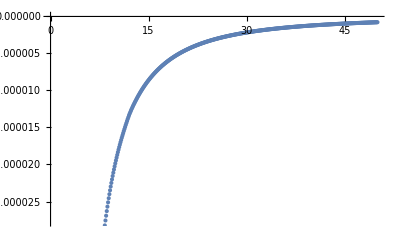

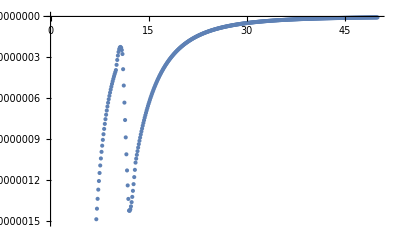

{(5. | -0.0000775034
5.1 | -0.0000745169
5.2 | -0.0000716985
5.3 | -0.000069036
5.4 | -0.0000665182
5.5 | -0.0000641347
5.6 | -0.0000618762
5.7 | -0.0000597344
5.8 | -0.0000577012
5.9 | -0.0000557696
6. | -0.0000539329
6.1 | -0.0000521863
6.2 | -0.0000505228
6.3 | -0.0000489373
6.4 | -0.0000474251
6.5 | -0.0000459816
6.6 | -0.0000446029
6.7 | -0.000043285
6.8 | -0.0000420246
6.9 | -0.0000408182
7. | -0.000039663
7.1 | -0.0000385562
7.2 | -0.000037495
7.3 | -0.0000364769
7.4 | -0.0000354997
7.5 | -0.0000345611
7.6 | -0.0000336592
7.7 | -0.0000327921
7.8 | -0.000031958
7.9 | -0.0000311553
8. | -0.0000303824
8.1 | -0.000029638
8.2 | -0.0000289205
8.3 | -0.0000282288
8.4 | -0.0000275615
8.5 | -0.0000269176
8.6 | -0.000026296
8.7 | -0.0000256957
8.8 | -0.0000251156
8.9 | -0.000024555
9. | -0.0000240129
9.1 | -0.0000234885
9.2 | -0.0000229812
9.3 | -0.00002249
9.4 | -0.0000220145
9.5 | -0.0000215538
9.6 | -0.0000211075
9.7 | -0.0000206749
9.8 | -0.0000202554
9.9 | -0.0000198485
10. | -0.0000194538
10.1 | -0.0000190717
10.2 | -0.0000187006
10.3 | -0.0000183401
10.4 | -0.0000179897
10.5 | -0.0000176491
10.6 | -0.0000173179
10.7 | -0.0000169957
10.8 | -0.0000166821
10.9 | -0.0000163768
11. | -0.0000160793
11.1 | -0.0000157861
11.2 | -0.0000154982
11.3 | -0.0000152151
11.4 | -0.0000149365
11.5 | -0.0000146622
11.6 | -0.0000143922
11.7 | -0.0000141268
11.8 | -0.0000138664
11.9 | -0.0000136117
12. | -0.0000133635
12.1 | -0.000013138
12.2 | -0.0000129208
12.3 | -0.0000127113
12.4 | -0.000012509
12.5 | -0.0000123134
12.6 | -0.0000121238
12.7 | -0.0000119396
12.8 | -0.0000117605
12.9 | -0.0000115858
13. | -0.0000114152
13.1 | -0.000011244
13.2 | -0.0000110765
13.3 | -0.0000109127
13.4 | -0.0000107526
13.5 | -0.0000105958
13.6 | -0.0000104425
13.7 | -0.0000102924
13.8 | -0.0000101455
13.9 | -0.0000100017
14. | -9.86093×10^-6
14.1 | -9.72308×10^-6
14.2 | -9.58809×10^-6
14.3 | -9.45586×10^-6
14.4 | -9.32632×10^-6
14.5 | -9.19942×10^-6
14.6 | -9.07506×10^-6
14.7 | -8.95319×10^-6
14.8 | -8.83375×10^-6
14.9 | -8.71666×10^-6
15. | -8.60187×10^-6
15.1 | -8.48934×10^-6
15.2 | -8.37898×10^-6
15.3 | -8.27074×10^-6
15.4 | -8.16458×10^-6
15.5 | -8.06044×10^-6
15.6 | -7.95826×10^-6
15.7 | -7.85801×10^-6
15.8 | -7.75963×10^-6
15.9 | -7.66307×10^-6
16. | -7.56829×10^-6
16.1 | -7.47526×10^-6
16.2 | -7.38392×10^-6
16.3 | -7.29424×10^-6
16.4 | -7.20617×10^-6
16.5 | -7.11968×10^-6
16.6 | -7.03473×10^-6
16.7 | -6.95128×10^-6
16.8 | -6.8693×10^-6
16.9 | -6.78876×10^-6
17. | -6.70962×10^-6
17.1 | -6.63185×10^-6
17.2 | -6.55542×10^-6
17.3 | -6.48029×10^-6
17.4 | -6.40645×10^-6
17.5 | -6.33385×10^-6
17.6 | -6.26248×10^-6
17.7 | -6.1923×10^-6
17.8 | -6.12329×10^-6
17.9 | -6.05542×10^-6
18. | -5.98867×10^-6
18.1 | -5.92301×10^-6
18.2 | -5.85843×10^-6
18.3 | -5.79489×10^-6
18.4 | -5.73237×10^-6
18.5 | -5.67086×10^-6
18.6 | -5.61033×10^-6
18.7 | -5.55076×10^-6
18.8 | -5.49212×10^-6
18.9 | -5.43441×10^-6
19. | -5.3776×10^-6
19.1 | -5.32168×10^-6
19.2 | -5.26662×10^-6
19.3 | -5.21241×10^-6
19.4 | -5.15902×10^-6
19.5 | -5.10645×10^-6
19.6 | -5.05468×10^-6
19.7 | -5.00369×10^-6
19.8 | -4.95346×10^-6
19.9 | -4.90398×10^-6
20. | -4.85524×10^-6
20.1 | -4.80722×10^-6
20.2 | -4.75991×10^-6
20.3 | -4.71329×10^-6
20.4 | -4.66735×10^-6
20.5 | -4.62208×10^-6
20.6 | -4.57746×10^-6
20.7 | -4.53348×10^-6
20.8 | -4.49013×10^-6
20.9 | -4.4474×10^-6
21. | -4.40527×10^-6
21.1 | -4.36374×10^-6
21.2 | -4.32279×10^-6
21.3 | -4.28242×10^-6
21.4 | -4.2426×10^-6
21.5 | -4.20334×10^-6
21.6 | -4.16462×10^-6
21.7 | -4.12643×10^-6
21.8 | -4.08876×10^-6
21.9 | -4.05161×10^-6
22. | -4.01495×10^-6
22.1 | -3.97879×10^-6
22.2 | -3.94312×10^-6
22.3 | -3.90792×10^-6
22.4 | -3.87319×10^-6
22.5 | -3.83892×10^-6
22.6 | -3.80511×10^-6
22.7 | -3.77173×10^-6
22.8 | -3.73879×10^-6
22.9 | -3.70629×10^-6
23. | -3.6742×10^-6
23.1 | -3.64253×10^-6
23.2 | -3.61126×10^-6
23.3 | -3.5804×10^-6
23.4 | -3.54993×10^-6
23.5 | -3.51984×10^-6
23.6 | -3.49014×10^-6
23.7 | -3.4608×10^-6
23.8 | -3.43184×10^-6
23.9 | -3.40324×10^-6
24. | -3.37499×10^-6
24.1 | -3.3471×10^-6
24.2 | -3.31954×10^-6
24.3 | -3.29233×10^-6
24.4 | -3.26545×10^-6
24.5 | -3.23889×10^-6
24.6 | -3.21266×10^-6
24.7 | -3.18675×10^-6
24.8 | -3.16114×10^-6
24.9 | -3.13585×10^-6
25. | -3.11085×10^-6
25.1 | -3.08615×10^-6
25.2 | -3.06175×10^-6
25.3 | -3.03763×10^-6
25.4 | -3.0138×10^-6
25.5 | -2.99024×10^-6
25.6 | -2.96696×10^-6
25.7 | -2.94395×10^-6
25.8 | -2.92121×10^-6
25.9 | -2.89873×10^-6
26. | -2.87651×10^-6
26.1 | -2.85454×10^-6
26.2 | -2.83282×10^-6
26.3 | -2.81135×10^-6
26.4 | -2.79012×10^-6
26.5 | -2.76914×10^-6
26.6 | -2.74838×10^-6
26.7 | -2.72786×10^-6
26.8 | -2.70757×10^-6
26.9 | -2.6875×10^-6
27. | -2.66766×10^-6
27.1 | -2.64803×10^-6
27.2 | -2.62862×10^-6
27.3 | -2.60942×10^-6
27.4 | -2.59043×10^-6
27.5 | -2.57165×10^-6
27.6 | -2.55307×10^-6
27.7 | -2.53469×10^-6
27.8 | -2.51651×10^-6
27.9 | -2.49852×10^-6
28. | -2.48073×10^-6
28.1 | -2.46313×10^-6
28.2 | -2.44571×10^-6
28.3 | -2.42847×10^-6
28.4 | -2.41142×10^-6
28.5 | -2.39454×10^-6
28.6 | -2.37785×10^-6
28.7 | -2.36132×10^-6
28.8 | -2.34497×10^-6
28.9 | -2.32878×10^-6
29. | -2.31277×10^-6
29.1 | -2.29692×10^-6
29.2 | -2.28123×10^-6
29.3 | -2.2657×10^-6
29.4 | -2.25032×10^-6
29.5 | -2.23511×10^-6
29.6 | -2.22005×10^-6
29.7 | -2.20514×10^-6
29.8 | -2.19037×10^-6
29.9 | -2.17576×10^-6
30. | -2.16129×10^-6
30.1 | -2.14697×10^-6
30.2 | -2.13279×10^-6
30.3 | -2.11874×10^-6
30.4 | -2.10484×10^-6
30.5 | -2.09107×10^-6
30.6 | -2.07744×10^-6
30.7 | -2.06394×10^-6
30.8 | -2.05057×10^-6
30.9 | -2.03733×10^-6
31. | -2.02422×10^-6
31.1 | -2.01123×10^-6
31.2 | -1.99837×10^-6
31.3 | -1.98563×10^-6
31.4 | -1.97301×10^-6
31.5 | -1.96051×10^-6
31.6 | -1.94813×10^-6
31.7 | -1.93587×10^-6
31.8 | -1.92372×10^-6
31.9 | -1.91169×10^-6
32. | -1.89977×10^-6
32.1 | -1.88796×10^-6
32.2 | -1.87626×10^-6
32.3 | -1.86467×10^-6
32.4 | -1.85318×10^-6
32.5 | -1.84181×10^-6
32.6 | -1.83053×10^-6
32.7 | -1.81936×10^-6
32.8 | -1.80829×10^-6
32.9 | -1.79732×10^-6
33. | -1.78645×10^-6
33.1 | -1.77568×10^-6
33.2 | -1.76501×10^-6
33.3 | -1.75443×10^-6
33.4 | -1.74394×10^-6
33.5 | -1.73355×10^-6
33.6 | -1.72326×10^-6
33.7 | -1.71305×10^-6
33.8 | -1.70294×10^-6
33.9 | -1.69291×10^-6
34. | -1.68297×10^-6
34.1 | -1.67312×10^-6
34.2 | -1.66336×10^-6
34.3 | -1.65368×10^-6
34.4 | -1.64408×10^-6
34.5 | -1.63457×10^-6
34.6 | -1.62514×10^-6
34.7 | -1.61579×10^-6
34.8 | -1.60652×10^-6
34.9 | -1.59734×10^-6
35. | -1.58823×10^-6
35.1 | -1.57919×10^-6
35.2 | -1.57024×10^-6
35.3 | -1.56136×10^-6
35.4 | -1.55255×10^-6
35.5 | -1.54382×10^-6
35.6 | -1.53517×10^-6
35.7 | -1.52658×10^-6
35.8 | -1.51807×10^-6
35.9 | -1.50963×10^-6
36. | -1.50126×10^-6
36.1 | -1.49296×10^-6
36.2 | -1.48472×10^-6
36.3 | -1.47656×10^-6
36.4 | -1.46846×10^-6
36.5 | -1.46043×10^-6
36.6 | -1.45246×10^-6
36.7 | -1.44456×10^-6
36.8 | -1.43672×10^-6
36.9 | -1.42895×10^-6
37. | -1.42124×10^-6
37.1 | -1.41359×10^-6
37.2 | -1.40601×10^-6
37.3 | -1.39848×10^-6
37.4 | -1.39102×10^-6
37.5 | -1.38361×10^-6
37.6 | -1.37626×10^-6
37.7 | -1.36897×10^-6
37.8 | -1.36174×10^-6
37.9 | -1.35457×10^-6
38. | -1.34745×10^-6
38.1 | -1.34039×10^-6
38.2 | -1.33339×10^-6
38.3 | -1.32643×10^-6
38.4 | -1.31954×10^-6
38.5 | -1.31269×10^-6
38.6 | -1.3059×10^-6
38.7 | -1.29917×10^-6
38.8 | -1.29248×10^-6
38.9 | -1.28585×10^-6
39. | -1.27926×10^-6
39.1 | -1.27273×10^-6
39.2 | -1.26625×10^-6
39.3 | -1.25981×10^-6
39.4 | -1.25343×10^-6
39.5 | -1.24709×10^-6
39.6 | -1.2408×10^-6
39.7 | -1.23456×10^-6
39.8 | -1.22837×10^-6
39.9 | -1.22222×10^-6
40. | -1.21612×10^-6
40.1 | -1.21006×10^-6
40.2 | -1.20405×10^-6
40.3 | -1.19809×10^-6
40.4 | -1.19216×10^-6
40.5 | -1.18629×10^-6
40.6 | -1.18045×10^-6
40.7 | -1.17466×10^-6
40.8 | -1.16891×10^-6
40.9 | -1.1632×10^-6
41. | -1.15754×10^-6
41.1 | -1.15191×10^-6
41.2 | -1.14633×10^-6
41.3 | -1.14079×10^-6
41.4 | -1.13528×10^-6
41.5 | -1.12982×10^-6
41.6 | -1.1244×10^-6
41.7 | -1.11901×10^-6
41.8 | -1.11367×10^-6
41.9 | -1.10836×10^-6
42. | -1.10309×10^-6
42.1 | -1.09786×10^-6
42.2 | -1.09266×10^-6
42.3 | -1.0875×10^-6
42.4 | -1.08238×10^-6
42.5 | -1.07729×10^-6
42.6 | -1.07224×10^-6
42.7 | -1.06723×10^-6
42.8 | -1.06225×10^-6
42.9 | -1.0573×10^-6
43. | -1.05239×10^-6
43.1 | -1.04751×10^-6
43.2 | -1.04267×10^-6
43.3 | -1.03786×10^-6
43.4 | -1.03309×10^-6
43.5 | -1.02834×10^-6
43.6 | -1.02363×10^-6
43.7 | -1.01895×10^-6
43.8 | -1.01431×10^-6
43.9 | -1.00969×10^-6
44. | -1.00511×10^-6
44.1 | -1.00056×10^-6
44.2 | -9.96036×10^-7
44.3 | -9.91545×10^-7
44.4 | -9.87085×10^-7
44.5 | -9.82655×10^-7
44.6 | -9.78254×10^-7
44.7 | -9.73883×10^-7
44.8 | -9.69541×10^-7
44.9 | -9.65228×10^-7
45. | -9.60944×10^-7
45.1 | -9.56688×10^-7
45.2 | -9.5246×10^-7
45.3 | -9.48261×10^-7
45.4 | -9.44089×10^-7
45.5 | -9.39944×10^-7
45.6 | -9.35827×10^-7
45.7 | -9.31737×10^-7
45.8 | -9.27674×10^-7
45.9 | -9.23637×10^-7
46. | -9.19626×10^-7
46.1 | -9.15641×10^-7
46.2 | -9.11683×10^-7
46.3 | -9.07749×10^-7
46.4 | -9.03842×10^-7
46.5 | -8.99959×10^-7
46.6 | -8.96101×10^-7
46.7 | -8.92269×10^-7
46.8 | -8.8846×10^-7
46.9 | -8.84676×10^-7
47. | -8.80916×10^-7
47.1 | -8.7718×10^-7
47.2 | -8.73468×10^-7
47.3 | -8.69779×10^-7
47.4 | -8.66114×10^-7
47.5 | -8.62471×10^-7
47.6 | -8.58852×10^-7
47.7 | -8.55255×10^-7
47.8 | -8.51681×10^-7
47.9 | -8.48129×10^-7
48. | -8.446×10^-7
48.1 | -8.41092×10^-7
48.2 | -8.37606×10^-7
48.3 | -8.34142×10^-7
48.4 | -8.30699×10^-7
48.5 | -8.27278×10^-7
48.6 | -8.23878×10^-7
48.7 | -8.20498×10^-7
48.8 | -8.17139×10^-7
48.9 | -8.13801×10^-7
49. | -8.10483×10^-7
49.1 | -8.07186×10^-7
49.2 | -8.03909×10^-7
49.3 | -8.00651×10^-7
49.4 | -7.97413×10^-7
49.5 | -7.94195×10^-7
49.6 | -7.90996×10^-7
49.7 | -7.87817×10^-7
49.8 | -7.84657×10^-7
49.9 | -7.81515×10^-7
50. | -7.78393×10^-7),(5. | -5.19514×10^-6
5.1 | -4.81737×10^-6
5.2 | -4.4743×10^-6
5.3 | -4.16274×10^-6
5.4 | -3.87976×10^-6
5.5 | -3.62263×10^-6
5.6 | -3.38879×10^-6
5.7 | -3.1759×10^-6
5.8 | -2.98176×10^-6
5.9 | -2.80433×10^-6
6. | -2.64169×10^-6
6.1 | -2.48111×10^-6
6.2 | -2.33287×10^-6
6.3 | -2.196×10^-6
6.4 | -2.0696×10^-6
6.5 | -1.95281×10^-6
6.6 | -1.84483×10^-6
6.7 | -1.74491×10^-6
6.8 | -1.65233×10^-6
6.9 | -1.56643×10^-6
7. | -1.48658×10^-6
7.1 | -1.40915×10^-6
7.2 | -1.33688×10^-6
7.3 | -1.2694×10^-6
7.4 | -1.20638×10^-6
7.5 | -1.14748×10^-6
7.6 | -1.0924×10^-6
7.7 | -1.04084×10^-6
7.8 | -9.92537×10^-7
7.9 | -9.47217×10^-7
8. | -9.04633×10^-7
8.1 | -8.63289×10^-7
8.2 | -8.24325×10^-7
8.3 | -7.87594×10^-7
8.4 | -7.52961×10^-7
8.5 | -7.20293×10^-7
8.6 | -6.89465×10^-7
8.7 | -6.60359×10^-7
8.8 | -6.32861×10^-7
8.9 | -6.06861×10^-7
9. | -5.82256×10^-7
9.1 | -5.58572×10^-7
9.2 | -5.36119×10^-7
9.3 | -5.14828×10^-7
9.4 | -4.94631×10^-7
9.5 | -4.75466×10^-7
9.6 | -4.57271×10^-7
9.7 | -4.39986×10^-7
9.8 | -4.23557×10^-7
9.9 | -4.07929×10^-7
10. | -3.93049×10^-7
10.1 | -3.54657×10^-7
10.2 | -3.18843×10^-7
10.3 | -2.86946×10^-7
10.4 | -2.6025×10^-7
10.5 | -2.39991×10^-7
10.6 | -2.2736×10^-7
10.7 | -2.23501×10^-7
10.8 | -2.29518×10^-7
10.9 | -2.46472×10^-7
11. | -2.75388×10^-7
11.1 | -3.86663×10^-7
11.2 | -5.06429×10^-7
11.3 | -6.31616×10^-7
11.4 | -7.5926×10^-7
11.5 | -8.86502×10^-7
11.6 | -1.01058×10^-6
11.7 | -1.12883×10^-6
11.8 | -1.23867×10^-6
11.9 | -1.33761×10^-6
12. | -1.42325×10^-6
12.1 | -1.42498×10^-6
12.2 | -1.41404×10^-6
12.3 | -1.39221×10^-6
12.4 | -1.3612×10^-6
12.5 | -1.32266×10^-6
12.6 | -1.27819×10^-6
12.7 | -1.22935×10^-6
12.8 | -1.17764×10^-6
12.9 | -1.12451×10^-6
13. | -1.07138×10^-6
13.1 | -1.04243×10^-6
13.2 | -1.01445×10^-6
13.3 | -9.87415×10^-7
13.4 | -9.61278×10^-7
13.5 | -9.36008×10^-7
13.6 | -9.11572×10^-7
13.7 | -8.87938×10^-7
13.8 | -8.65075×10^-7
13.9 | -8.42953×10^-7
14. | -8.21541×10^-7
14.1 | -8.00762×10^-7
14.2 | -7.80641×10^-7
14.3 | -7.61154×10^-7
14.4 | -7.42277×10^-7
14.5 | -7.23987×10^-7
14.6 | -7.06262×10^-7
14.7 | -6.8908×10^-7
14.8 | -6.72421×10^-7
14.9 | -6.56263×10^-7
15. | -6.40587×10^-7
15.1 | -6.25306×10^-7
15.2 | -6.10474×10^-7
15.3 | -5.96075×10^-7
15.4 | -5.82096×10^-7
15.5 | -5.68522×10^-7
15.6 | -5.55341×10^-7
15.7 | -5.42538×10^-7
15.8 | -5.30102×10^-7
15.9 | -5.1802×10^-7
16. | -5.06279×10^-7
16.1 | -4.94848×10^-7
16.2 | -4.83736×10^-7
16.3 | -4.72935×10^-7
16.4 | -4.62433×10^-7
16.5 | -4.52221×10^-7
16.6 | -4.4229×10^-7
16.7 | -4.32631×10^-7
16.8 | -4.23235×10^-7
16.9 | -4.14093×10^-7
17. | -4.05196×10^-7
17.1 | -3.96519×10^-7
17.2 | -3.88072×10^-7
17.3 | -3.79849×10^-7
17.4 | -3.71843×10^-7
17.5 | -3.64048×10^-7
17.6 | -3.56456×10^-7
17.7 | -3.49062×10^-7
17.8 | -3.4186×10^-7
17.9 | -3.34844×10^-7
18. | -3.28008×10^-7
18.1 | -3.21334×10^-7
18.2 | -3.1483×10^-7
18.3 | -3.0849×10^-7
18.4 | -3.02311×10^-7
18.5 | -2.96286×10^-7
18.6 | -2.90413×10^-7
18.7 | -2.84686×10^-7
18.8 | -2.79102×10^-7
18.9 | -2.73655×10^-7
19. | -2.68342×10^-7
19.1 | -2.63154×10^-7
19.2 | -2.58092×10^-7
19.3 | -2.53153×10^-7
19.4 | -2.48333×10^-7
19.5 | -2.43629×10^-7
19.6 | -2.39038×10^-7
19.7 | -2.34556×10^-7
19.8 | -2.3018×10^-7
19.9 | -2.25907×10^-7
20. | -2.21734×10^-7
20.1 | -2.17651×10^-7
20.2 | -2.13664×10^-7
20.3 | -2.09768×10^-7
20.4 | -2.05961×10^-7
20.5 | -2.02241×10^-7
20.6 | -1.98606×10^-7
20.7 | -1.95054×10^-7
20.8 | -1.91581×10^-7
20.9 | -1.88185×10^-7
21. | -1.84865×10^-7
21.1 | -1.81612×10^-7
21.2 | -1.78431×10^-7
21.3 | -1.75319×10^-7
21.4 | -1.72276×10^-7
21.5 | -1.69299×10^-7
21.6 | -1.66387×10^-7
21.7 | -1.63539×10^-7
21.8 | -1.60753×10^-7
21.9 | -1.58027×10^-7
22. | -1.5536×10^-7
22.1 | -1.52751×10^-7
22.2 | -1.50199×10^-7
22.3 | -1.47701×10^-7
22.4 | -1.45256×10^-7
22.5 | -1.42862×10^-7
22.6 | -1.40519×10^-7
22.7 | -1.38223×10^-7
22.8 | -1.35976×10^-7
22.9 | -1.33774×10^-7
23. | -1.31616×10^-7
23.1 | -1.29496×10^-7
23.2 | -1.27418×10^-7
23.3 | -1.25382×10^-7
23.4 | -1.23386×10^-7
23.5 | -1.2143×10^-7
23.6 | -1.19512×10^-7
23.7 | -1.17633×10^-7
23.8 | -1.15791×10^-7
23.9 | -1.13985×10^-7
24. | -1.12215×10^-7
24.1 | -1.10479×10^-7
24.2 | -1.08778×10^-7
24.3 | -1.07109×10^-7
24.4 | -1.05473×10^-7
24.5 | -1.03869×10^-7
24.6 | -1.02296×10^-7
24.7 | -1.00753×10^-7
24.8 | -9.92391×10^-8
24.9 | -9.77545×10^-8
25. | -9.62981×10^-8
25.1 | -9.48692×10^-8
25.2 | -9.34671×10^-8
25.3 | -9.20912×10^-8
25.4 | -9.07409×10^-8
25.5 | -8.94155×10^-8
25.6 | -8.81144×10^-8
25.7 | -8.6837×10^-8
25.8 | -8.55827×10^-8
25.9 | -8.43509×10^-8
26. | -8.3141×10^-8
26.1 | -8.19491×10^-8
26.2 | -8.07782×10^-8
26.3 | -7.9628×10^-8
26.4 | -7.84981×10^-8
26.5 | -7.73881×10^-8
26.6 | -7.62978×10^-8
26.7 | -7.52266×10^-8
26.8 | -7.41744×10^-8
26.9 | -7.31409×10^-8
27. | -7.21255×10^-8
27.1 | -7.11295×10^-8
27.2 | -7.01509×10^-8
27.3 | -6.91896×10^-8
27.4 | -6.8245×10^-8
27.5 | -6.73169×10^-8
27.6 | -6.64048×10^-8
27.7 | -6.55084×10^-8
27.8 | -6.46273×10^-8
27.9 | -6.37612×10^-8
28. | -6.29098×10^-8
28.1 | -6.2072×10^-8
28.2 | -6.12482×10^-8
28.3 | -6.0438×10^-8
28.4 | -5.96413×10^-8
28.5 | -5.88577×10^-8
28.6 | -5.80869×10^-8
28.7 | -5.73286×10^-8
28.8 | -5.65827×10^-8
28.9 | -5.58487×10^-8
29. | -5.51264×10^-8
29.1 | -5.44144×10^-8
29.2 | -5.37137×10^-8
29.3 | -5.30241×10^-8
29.4 | -5.23454×10^-8
29.5 | -5.16774×10^-8
29.6 | -5.102×10^-8
29.7 | -5.03729×10^-8
29.8 | -4.9736×10^-8
29.9 | -4.91092×10^-8
30. | -4.84922×10^-8
30.1 | -4.78848×10^-8
30.2 | -4.7287×10^-8
30.3 | -4.66986×10^-8
30.4 | -4.61193×10^-8
30.5 | -4.55491×10^-8
30.6 | -4.49878×10^-8
30.7 | -4.44351×10^-8
30.8 | -4.38911×10^-8
30.9 | -4.33554×10^-8
31. | -4.28281×10^-8
31.1 | -4.23088×10^-8
31.2 | -4.17975×10^-8
31.3 | -4.12941×10^-8
31.4 | -4.07983×10^-8
31.5 | -4.03101×10^-8
31.6 | -3.98293×10^-8
31.7 | -3.93558×10^-8
31.8 | -3.88894×10^-8
31.9 | -3.843×10^-8
32. | -3.79775×10^-8
32.1 | -3.75315×10^-8
32.2 | -3.70922×10^-8
32.3 | -3.66594×10^-8
32.4 | -3.6233×10^-8
32.5 | -3.58128×10^-8
32.6 | -3.53989×10^-8
32.7 | -3.4991×10^-8
32.8 | -3.45892×10^-8
32.9 | -3.41931×10^-8
33. | -3.38029×10^-8
33.1 | -3.34184×10^-8
33.2 | -3.30394×10^-8
33.3 | -3.26659×10^-8
33.4 | -3.22978×10^-8
33.5 | -3.19348×10^-8
33.6 | -3.1577×10^-8
33.7 | -3.12243×10^-8
33.8 | -3.08764×10^-8
33.9 | -3.05334×10^-8
34. | -3.01951×10^-8
34.1 | -2.9861×10^-8
34.2 | -2.95314×10^-8
34.3 | -2.92064×10^-8
34.4 | -2.88858×10^-8
34.5 | -2.85695×10^-8
34.6 | -2.82576×10^-8
34.7 | -2.79499×10^-8
34.8 | -2.76464×10^-8
34.9 | -2.73469×10^-8
35. | -2.70516×10^-8
35.1 | -2.67601×10^-8
35.2 | -2.64726×10^-8
35.3 | -2.6189×10^-8
35.4 | -2.59092×10^-8
35.5 | -2.56331×10^-8
35.6 | -2.53608×10^-8
35.7 | -2.50921×10^-8
35.8 | -2.4827×10^-8
35.9 | -2.45654×10^-8
36. | -2.43074×10^-8
36.1 | -2.40528×10^-8
36.2 | -2.38016×10^-8
36.3 | -2.35537×10^-8
36.4 | -2.33091×10^-8
36.5 | -2.30677×10^-8
36.6 | -2.28295×10^-8
36.7 | -2.25944×10^-8
36.8 | -2.23624×10^-8
36.9 | -2.21334×10^-8
37. | -2.19074×10^-8
37.1 | -2.16842×10^-8
37.2 | -2.14639×10^-8
37.3 | -2.12464×10^-8
37.4 | -2.10317×10^-8
37.5 | -2.08198×10^-8
37.6 | -2.06105×10^-8
37.7 | -2.04039×10^-8
37.8 | -2.01999×10^-8
37.9 | -1.99984×10^-8
38. | -1.97995×10^-8
38.1 | -1.96029×10^-8
38.2 | -1.94088×10^-8
38.3 | -1.92171×10^-8
38.4 | -1.90277×10^-8
38.5 | -1.88407×10^-8
38.6 | -1.8656×10^-8
38.7 | -1.84736×10^-8
38.8 | -1.82935×10^-8
38.9 | -1.81155×10^-8
39. | -1.79398×10^-8
39.1 | -1.77662×10^-8
39.2 | -1.75948×10^-8
39.3 | -1.74255×10^-8
39.4 | -1.72582×10^-8
39.5 | -1.7093×10^-8
39.6 | -1.69298×10^-8
39.7 | -1.67685×10^-8
39.8 | -1.66093×10^-8
39.9 | -1.6452×10^-8
40. | -1.62965×10^-8
40.1 | -1.6143×10^-8
40.2 | -1.59913×10^-8
40.3 | -1.58415×10^-8
40.4 | -1.56934×10^-8
40.5 | -1.55471×10^-8
40.6 | -1.54026×10^-8
40.7 | -1.52597×10^-8
40.8 | -1.51185×10^-8
40.9 | -1.49789×10^-8
41. | -1.4841×10^-8
41.1 | -1.47045×10^-8
41.2 | -1.45696×10^-8
41.3 | -1.44363×10^-8
41.4 | -1.43045×10^-8
41.5 | -1.41742×10^-8
41.6 | -1.40454×10^-8
41.7 | -1.39181×10^-8
41.8 | -1.37922×10^-8
41.9 | -1.36678×10^-8
42. | -1.35448×10^-8
42.1 | -1.34233×10^-8
42.2 | -1.33031×10^-8
42.3 | -1.31843×10^-8
42.4 | -1.30669×10^-8
42.5 | -1.29508×10^-8
42.6 | -1.2836×10^-8
42.7 | -1.27225×10^-8
42.8 | -1.26102×10^-8
42.9 | -1.24993×10^-8
43. | -1.23895×10^-8
43.1 | -1.22809×10^-8
43.2 | -1.21736×10^-8
43.3 | -1.20674×10^-8
43.4 | -1.19624×10^-8
43.5 | -1.18585×10^-8
43.6 | -1.17558×10^-8
43.7 | -1.16542×10^-8
43.8 | -1.15537×10^-8
43.9 | -1.14543×10^-8
44. | -1.1356×10^-8
44.1 | -1.12587×10^-8
44.2 | -1.11624×10^-8
44.3 | -1.10672×10^-8
44.4 | -1.09731×10^-8
44.5 | -1.08799×10^-8
44.6 | -1.07878×10^-8
44.7 | -1.06966×10^-8
44.8 | -1.06064×10^-8
44.9 | -1.05173×10^-8
45. | -1.0429×10^-8
45.1 | -1.03418×10^-8
45.2 | -1.02555×10^-8
45.3 | -1.01701×10^-8
45.4 | -1.00856×10^-8
45.5 | -1.00021×10^-8
45.6 | -9.91936×10^-9
45.7 | -9.83755×10^-9
45.8 | -9.75659×10^-9
45.9 | -9.67648×10^-9
46. | -9.5972×10^-9
46.1 | -9.51867×10^-9
46.2 | -9.44096×10^-9
46.3 | -9.36406×10^-9
46.4 | -9.28795×10^-9
46.5 | -9.21264×10^-9
46.6 | -9.13811×10^-9
46.7 | -9.06436×10^-9
46.8 | -8.99138×10^-9
46.9 | -8.91917×10^-9
47. | -8.84771×10^-9
47.1 | -8.77711×10^-9
47.2 | -8.70724×10^-9
47.3 | -8.6381×10^-9
47.4 | -8.56967×10^-9
47.5 | -8.50193×10^-9
47.6 | -8.43487×10^-9
47.7 | -8.36849×10^-9
47.8 | -8.30275×10^-9
47.9 | -8.23767×10^-9
48. | -8.17321×10^-9
48.1 | -8.10922×10^-9
48.2 | -8.04585×10^-9
48.3 | -7.98309×10^-9
48.4 | -7.92093×10^-9
48.5 | -7.85938×10^-9
48.6 | -7.79843×10^-9
48.7 | -7.73807×10^-9
48.8 | -7.6783×10^-9
48.9 | -7.61913×10^-9
49. | -7.56053×10^-9
49.1 | -7.50259×10^-9
49.2 | -7.44522×10^-9
49.3 | -7.38842×10^-9
49.4 | -7.33217×10^-9
49.5 | -7.27648×10^-9
49.6 | -7.22132×10^-9
49.7 | -7.1667×10^-9
49.8 | -7.11261×10^-9
49.9 | -7.05904×10^-9
50. | -7.00598×10^-9)}

```mathematica
tabre = Re[tabnow];
ListPlot[Re[tabnow]]
tabim = tabnow;
tabim [[All,2]]=Im[tabnow[[All,2]]];
ListPlot[tabim]

{MatrixForm[tabre ],MatrixForm[tabim ]}
```

(5. | 8.66557
5.1 | 8.66557
5.2 | 8.66557
5.3 | 8.66557
5.4 | 8.66557
5.5 | 8.66557
5.6 | 8.66557
5.7 | 8.66557
5.8 | 8.66557
5.9 | 8.66557
6. | 8.66557
6.1 | 8.66557
6.2 | 8.66557
6.3 | 8.66557
6.4 | 8.66557
6.5 | 8.66557
6.6 | 8.66557
6.7 | 8.66557
6.8 | 8.66557
6.9 | 8.66557
7. | 8.66557
7.1 | 8.66557
7.2 | 8.66557
7.3 | 8.66557
7.4 | 8.66557
7.5 | 8.66557
7.6 | 8.66557
7.7 | 8.66557
7.8 | 8.66557
7.9 | 8.66557
8. | 8.66557
8.1 | 8.66557
8.2 | 8.66557
8.3 | 8.66557
8.4 | 8.66557
8.5 | 8.66557
8.6 | 8.66557
8.7 | 8.66557
8.8 | 8.66557
8.9 | 8.66557
9. | 8.66557
9.1 | 8.66557
9.2 | 8.66557
9.3 | 8.66557
9.4 | 8.66557
9.5 | 8.66557
9.6 | 8.66557
9.7 | 8.66557
9.8 | 8.66557
9.9 | 8.66557
10. | 8.66557
10.1 | 8.66557
10.2 | 8.66557
10.3 | 8.66557
10.4 | 8.66557
10.5 | 8.66557
10.6 | 8.66557
10.7 | 8.66557
10.8 | 8.66557
10.9 | 8.66557
11. | 8.66557
11.1 | 8.66557
11.2 | 8.66557
11.3 | 8.66557
11.4 | 8.66557
11.5 | 8.66557
11.6 | 8.66557
11.7 | 8.66557
11.8 | 8.66557
11.9 | 8.66557
12. | 8.66557
12.1 | 8.66557
12.2 | 8.66557
12.3 | 8.66557
12.4 | 8.66557
12.5 | 8.66557
12.6 | 8.66557
12.7 | 8.66557
12.8 | 8.66557
12.9 | 8.66557
13. | 8.66557
13.1 | 8.66557
13.2 | 8.66557
13.3 | 8.66557
13.4 | 8.66557
13.5 | 8.66557
13.6 | 8.66557
13.7 | 8.66557
13.8 | 8.66557
13.9 | 8.66557
14. | 8.66557
14.1 | 8.66557
14.2 | 8.66557
14.3 | 8.66557
14.4 | 8.66557
14.5 | 8.66557
14.6 | 8.66557
14.7 | 8.66557
14.8 | 8.66557
14.9 | 8.66557
15. | 8.66557
15.1 | 8.66557
15.2 | 8.66557
15.3 | 8.66557
15.4 | 8.66557
15.5 | 8.66557
15.6 | 8.66557
15.7 | 8.66557
15.8 | 8.66557
15.9 | 8.66557
16. | 8.66557
16.1 | 8.66557
16.2 | 8.66557
16.3 | 8.66557
16.4 | 8.66557
16.5 | 8.66557
16.6 | 8.66557
16.7 | 8.66557
16.8 | 8.66557
16.9 | 8.66557
17. | 8.66557
17.1 | 8.66557
17.2 | 8.66557
17.3 | 8.66557
17.4 | 8.66557
17.5 | 8.66557
17.6 | 8.66557
17.7 | 8.66557
17.8 | 8.66557
17.9 | 8.66557
18. | 8.66557
18.1 | 8.66557
18.2 | 8.66557
18.3 | 8.66557
18.4 | 8.66557
18.5 | 8.66557
18.6 | 8.66557
18.7 | 8.66557
18.8 | 8.66557
18.9 | 8.66557
19. | 8.66557
19.1 | 8.66557
19.2 | 8.66557
19.3 | 8.66557
19.4 | 8.66557
19.5 | 8.66557
19.6 | 8.66557
19.7 | 8.66557
19.8 | 8.66557
19.9 | 8.66557
20. | 8.66557
20.1 | 8.66557
20.2 | 8.66557
20.3 | 8.66557
20.4 | 8.66557
20.5 | 8.66557
20.6 | 8.66557
20.7 | 8.66557
20.8 | 8.66557
20.9 | 8.66557
21. | 8.66557
21.1 | 8.66557
21.2 | 8.66557
21.3 | 8.66557
21.4 | 8.66557
21.5 | 8.66557
21.6 | 8.66557
21.7 | 8.66557
21.8 | 8.66557
21.9 | 8.66557
22. | 8.66557
22.1 | 8.66557
22.2 | 8.66557
22.3 | 8.66557
22.4 | 8.66557
22.5 | 8.66557
22.6 | 8.66557
22.7 | 8.66557
22.8 | 8.66557
22.9 | 8.66557
23. | 8.66557
23.1 | 8.66557
23.2 | 8.66557
23.3 | 8.66557
23.4 | 8.66557
23.5 | 8.66557
23.6 | 8.66557
23.7 | 8.66557
23.8 | 8.66557
23.9 | 8.66557
24. | 8.66557
24.1 | 8.66557
24.2 | 8.66557
24.3 | 8.66557
24.4 | 8.66557
24.5 | 8.66557
24.6 | 8.66557
24.7 | 8.66557
24.8 | 8.66557
24.9 | 8.66557
25. | 8.66557
25.1 | 8.66557
25.2 | 8.66557
25.3 | 8.66557
25.4 | 8.66557
25.5 | 8.66557
25.6 | 8.66557
25.7 | 8.66557
25.8 | 8.66557
25.9 | 8.66557
26. | 8.66557
26.1 | 8.66557
26.2 | 8.66557
26.3 | 8.66557
26.4 | 8.66557
26.5 | 8.66557
26.6 | 8.66557
26.7 | 8.66557
26.8 | 8.66557
26.9 | 8.66557
27. | 8.66557
27.1 | 8.66557
27.2 | 8.66557
27.3 | 8.66557
27.4 | 8.66557
27.5 | 8.66557
27.6 | 8.66557
27.7 | 8.66557
27.8 | 8.66557
27.9 | 8.66557
28. | 8.66557
28.1 | 8.66557
28.2 | 8.66557
28.3 | 8.66557
28.4 | 8.66557
28.5 | 8.66557
28.6 | 8.66557
28.7 | 8.66557
28.8 | 8.66557
28.9 | 8.66557
29. | 8.66557
29.1 | 8.66557
29.2 | 8.66557
29.3 | 8.66557
29.4 | 8.66557
29.5 | 8.66557
29.6 | 8.66557
29.7 | 8.66557
29.8 | 8.66557
29.9 | 8.66557
30. | 8.66557
30.1 | 8.66557
30.2 | 8.66557
30.3 | 8.66557
30.4 | 8.66557
30.5 | 8.66557
30.6 | 8.66557
30.7 | 8.66557
30.8 | 8.66557
30.9 | 8.66557
31. | 8.66557
31.1 | 8.66557
31.2 | 8.66557
31.3 | 8.66557
31.4 | 8.66557
31.5 | 8.66557
31.6 | 8.66557
31.7 | 8.66557
31.8 | 8.66557
31.9 | 8.66557
32. | 8.66557
32.1 | 8.66557
32.2 | 8.66557
32.3 | 8.66557
32.4 | 8.66557
32.5 | 8.66557
32.6 | 8.66557
32.7 | 8.66557
32.8 | 8.66557
32.9 | 8.66557
33. | 8.66557
33.1 | 8.66557
33.2 | 8.66557
33.3 | 8.66557
33.4 | 8.66557
33.5 | 8.66557
33.6 | 8.66557
33.7 | 8.66557
33.8 | 8.66557
33.9 | 8.66557
34. | 8.66557
34.1 | 8.66557
34.2 | 8.66557
34.3 | 8.66557
34.4 | 8.66557
34.5 | 8.66557
34.6 | 8.66557
34.7 | 8.66557
34.8 | 8.66557
34.9 | 8.66557
35. | 8.66557
35.1 | 8.66557
35.2 | 8.66557
35.3 | 8.66557
35.4 | 8.66557
35.5 | 8.66557
35.6 | 8.66557
35.7 | 8.66557
35.8 | 8.66557
35.9 | 8.66557
36. | 8.66557
36.1 | 8.66557
36.2 | 8.66557
36.3 | 8.66557
36.4 | 8.66557
36.5 | 8.66557
36.6 | 8.66557
36.7 | 8.66557
36.8 | 8.66557
36.9 | 8.66557
37. | 8.66557
37.1 | 8.66557
37.2 | 8.66557
37.3 | 8.66557
37.4 | 8.66557
37.5 | 8.66557
37.6 | 8.66557
37.7 | 8.66557
37.8 | 8.66557
37.9 | 8.66557
38. | 8.66557
38.1 | 8.66557
38.2 | 8.66557
38.3 | 8.66557
38.4 | 8.66557
38.5 | 8.66557
38.6 | 8.66557
38.7 | 8.66557
38.8 | 8.66557
38.9 | 8.66557
39. | 8.66557
39.1 | 8.66557
39.2 | 8.66557
39.3 | 8.66557
39.4 | 8.66557
39.5 | 8.66557
39.6 | 8.66557
39.7 | 8.66557
39.8 | 8.66557
39.9 | 8.66557
40. | 8.66557
40.1 | 8.66557
40.2 | 8.66557
40.3 | 8.66557
40.4 | 8.66557
40.5 | 8.66557
40.6 | 8.66557
40.7 | 8.66557
40.8 | 8.66557
40.9 | 8.66557
41. | 8.66557
41.1 | 8.66557
41.2 | 8.66557
41.3 | 8.66557
41.4 | 8.66557
41.5 | 8.66557
41.6 | 8.66557
41.7 | 8.66557
41.8 | 8.66557
41.9 | 8.66557
42. | 8.66557
42.1 | 8.66557
42.2 | 8.66557
42.3 | 8.66557
42.4 | 8.66557
42.5 | 8.66557
42.6 | 8.66557
42.7 | 8.66557
42.8 | 8.66557
42.9 | 8.66557
43. | 8.66557
43.1 | 8.66557
43.2 | 8.66557
43.3 | 8.66557
43.4 | 8.66557
43.5 | 8.66557
43.6 | 8.66557
43.7 | 8.66557
43.8 | 8.66557
43.9 | 8.66557
44. | 8.66557
44.1 | 8.66557
44.2 | 8.66557
44.3 | 8.66557
44.4 | 8.66557
44.5 | 8.66557
44.6 | 8.66557
44.7 | 8.66557
44.8 | 8.66557
44.9 | 8.66557
45. | 8.66557
45.1 | 8.66557
45.2 | 8.66557
45.3 | 8.66557
45.4 | 8.66557
45.5 | 8.66557
45.6 | 8.66557
45.7 | 8.66557
45.8 | 8.66557
45.9 | 8.66557
46. | 8.66557
46.1 | 8.66557
46.2 | 8.66557
46.3 | 8.66557
46.4 | 8.66557
46.5 | 8.66557
46.6 | 8.66557
46.7 | 8.66557
46.8 | 8.66557
46.9 | 8.66557
47. | 8.66557
47.1 | 8.66557
47.2 | 8.66557
47.3 | 8.66557
47.4 | 8.66557
47.5 | 8.66557
47.6 | 8.66557
47.7 | 8.66557
47.8 | 8.66557
47.9 | 8.66557
48. | 8.66557
48.1 | 8.66557
48.2 | 8.66557
48.3 | 8.66557
48.4 | 8.66557
48.5 | 8.66557
48.6 | 8.66557
48.7 | 8.66557
48.8 | 8.66557
48.9 | 8.66557
49. | 8.66557
49.1 | 8.66557
49.2 | 8.66557
49.3 | 8.66557
49.4 | 8.66557
49.5 | 8.66557
49.6 | 8.66557
49.7 | 8.66557
49.8 | 8.66557
49.9 | 8.66557
50. | 8.66557)

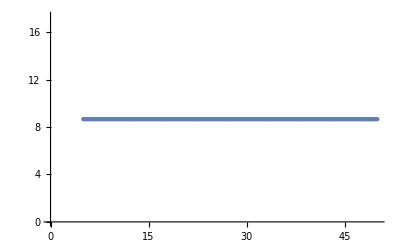

-Graphics-

```mathematica
{hnow,know,lnow}={2,2,0};
mnow = 7;

MatrixForm[
tabnow=Table[{EkeV,
ffactorreal[EkeV,hnow,know,lnow,mnow]
	}
,{EkeV,5,50,0.1}]
]
tabre=tabnow;
tabre[[All,2]]=Re[tabnow[[All,2]]];
tabim=tabnow;
tabim[[All,2]]=Re[tabnow[[All,2]]];
ListPlot[tabre]
ListPlot[tabim]
```

```mathematica
Subscript[assorbimento, 7]=Import["C:\\Users\\xx9905\\Documents\\archivio txt\\assorbimento vs energia molti materiali\\14.dat","Table"];

MatrixForm[Subscript[assorbimento, 7]]
```

(0. | 0 | 0
0.001 | 1570. | 1567.
0.002 | 2777. | 2775.
0.003 | 978.4 | 976.7
0.004 | 452.8 | 451.4
0.005 | 245.1 | 243.9
0.006 | 147. | 145.9
0.007 | 94.88 | 93.97
0.008 | 64.69 | 63.89
0.009 | 46.02 | 45.31
0.01 | 33.88 | 33.26
0.011 | 25.65 | 25.1
0.012 | 19.89 | 19.4
0.013 | 15.73 | 15.29
0.014 | 12.66 | 12.26
0.015 | 10.34 | 9.977
0.016 | 8.554 | 8.227
0.017 | 7.162 | 6.864
0.018 | 6.061 | 5.787
0.019 | 5.179 | 4.926
0.02 | 4.463 | 4.229
0.021 | 3.878 | 3.66
0.022 | 3.393 | 3.191
0.023 | 2.99 | 2.8
0.024 | 2.651 | 2.473
0.025 | 2.364 | 2.197
0.026 | 2.119 | 1.962
0.027 | 1.91 | 1.762
0.028 | 1.729 | 1.589
0.029 | 1.573 | 1.44
0.03 | 1.436 | 1.311
0.031 | 1.317 | 1.198
0.032 | 1.212 | 1.099
0.033 | 1.12 | 1.012
0.034 | 1.038 | 0.9352
0.035 | 0.9652 | 0.8671
0.036 | 0.9004 | 0.8066
0.037 | 0.8423 | 0.7526
0.038 | 0.7902 | 0.7044
0.039 | 0.7433 | 0.6611
0.04 | 0.701 | 0.6221
0.041 | 0.6627 | 0.587
0.042 | 0.628 | 0.5553
0.043 | 0.5963 | 0.5265
0.044 | 0.5675 | 0.5003
0.045 | 0.5412 | 0.4765
0.046 | 0.517 | 0.4547
0.047 | 0.4949 | 0.4348
0.048 | 0.4746 | 0.4166
0.049 | 0.4558 | 0.3999
0.05 | 0.4385 | 0.3845
0.051 | 0.4225 | 0.3703
0.052 | 0.4077 | 0.3572
0.053 | 0.3939 | 0.3451
0.054 | 0.3811 | 0.3339
0.055 | 0.3692 | 0.3235
0.056 | 0.3582 | 0.3139
0.057 | 0.3478 | 0.3049
0.058 | 0.3382 | 0.2965
0.059 | 0.3291 | 0.2888
0.06 | 0.3206 | 0.2815
0.061 | 0.3127 | 0.2747
0.062 | 0.3052 | 0.2683
0.063 | 0.2982 | 0.2623
0.064 | 0.2916 | 0.2567
0.065 | 0.2854 | 0.2514
0.066 | 0.2795 | 0.2465
0.067 | 0.2739 | 0.2418
0.068 | 0.2687 | 0.2374
0.069 | 0.2637 | 0.2332
0.07 | 0.259 | 0.2293
0.071 | 0.2545 | 0.2256
0.072 | 0.2503 | 0.2221
0.073 | 0.2462 | 0.2187
0.074 | 0.2424 | 0.2156
0.075 | 0.2387 | 0.2125
0.076 | 0.2352 | 0.2097
0.077 | 0.2319 | 0.207
0.078 | 0.2287 | 0.2044
0.079 | 0.2257 | 0.2019
0.08 | 0.2228 | 0.1995
0.081 | 0.22 | 0.1973
0.082 | 0.2173 | 0.1951
0.083 | 0.2148 | 0.1931
0.084 | 0.2124 | 0.1911
0.085 | 0.21 | 0.1892
0.086 | 0.2077 | 0.1874
0.087 | 0.2056 | 0.1857
0.088 | 0.2035 | 0.184
0.089 | 0.2015 | 0.1824
0.09 | 0.1996 | 0.1809
0.091 | 0.1977 | 0.1794
0.092 | 0.1959 | 0.1779
0.093 | 0.1942 | 0.1766
0.094 | 0.1925 | 0.1752
0.095 | 0.1909 | 0.174
0.096 | 0.1893 | 0.1727
0.097 | 0.1878 | 0.1715
0.098 | 0.1863 | 0.1704
0.099 | 0.1849 | 0.1693
0.1 | 0.1835 | 0.1682
0.101 | 0.1822 | 0.1671
0.102 | 0.1809 | 0.1661
0.103 | 0.1797 | 0.1651
0.104 | 0.1784 | 0.1642
0.105 | 0.1773 | 0.1632
0.106 | 0.1761 | 0.1623
0.107 | 0.175 | 0.1615
0.108 | 0.1739 | 0.1606
0.109 | 0.1729 | 0.1598
0.11 | 0.1718 | 0.159
0.111 | 0.1708 | 0.1582
0.112 | 0.1699 | 0.1574
0.113 | 0.1689 | 0.1567
0.114 | 0.168 | 0.156
0.115 | 0.1671 | 0.1553
0.116 | 0.1662 | 0.1546
0.117 | 0.1653 | 0.1539
0.118 | 0.1645 | 0.1532
0.119 | 0.1637 | 0.1526
0.12 | 0.1629 | 0.152
0.121 | 0.1621 | 0.1513
0.122 | 0.1613 | 0.1507
0.123 | 0.1606 | 0.1502
0.124 | 0.1598 | 0.1496
0.125 | 0.1591 | 0.149
0.126 | 0.1584 | 0.1485
0.127 | 0.1577 | 0.1479
0.128 | 0.157 | 0.1474
0.129 | 0.1564 | 0.1469
0.13 | 0.1557 | 0.1463
0.131 | 0.1551 | 0.1458
0.132 | 0.1544 | 0.1453
0.133 | 0.1538 | 0.1449
0.134 | 0.1532 | 0.1444
0.135 | 0.1526 | 0.1439
0.136 | 0.152 | 0.1435
0.137 | 0.1515 | 0.143
0.138 | 0.1509 | 0.1426
0.139 | 0.1504 | 0.1421
0.14 | 0.1498 | 0.1417
0.141 | 0.1493 | 0.1413
0.142 | 0.1488 | 0.1408
0.143 | 0.1482 | 0.1404
0.144 | 0.1477 | 0.14
0.145 | 0.1472 | 0.1396
0.146 | 0.1467 | 0.1392
0.147 | 0.1463 | 0.1388
0.148 | 0.1458 | 0.1385
0.149 | 0.1453 | 0.1381
0.15 | 0.1448 | 0.1377
0.151 | 0.1444 | 0.1373
0.152 | 0.1439 | 0.137
0.153 | 0.1435 | 0.1366
0.154 | 0.143 | 0.1363
0.155 | 0.1426 | 0.1359
0.156 | 0.1422 | 0.1356
0.157 | 0.1418 | 0.1352
0.158 | 0.1413 | 0.1349
0.159 | 0.1409 | 0.1346
0.16 | 0.1405 | 0.1342
0.161 | 0.1401 | 0.1339
0.162 | 0.1397 | 0.1336
0.163 | 0.1393 | 0.1333
0.164 | 0.139 | 0.133
0.165 | 0.1386 | 0.1326
0.166 | 0.1382 | 0.1323
0.167 | 0.1378 | 0.132
0.168 | 0.1375 | 0.1317
0.169 | 0.1371 | 0.1314
0.17 | 0.1367 | 0.1311
0.171 | 0.1364 | 0.1309
0.172 | 0.136 | 0.1306
0.173 | 0.1357 | 0.1303
0.174 | 0.1353 | 0.13
0.175 | 0.135 | 0.1297
0.176 | 0.1347 | 0.1294
0.177 | 0.1343 | 0.1292
0.178 | 0.134 | 0.1289
0.179 | 0.1337 | 0.1286
0.18 | 0.1334 | 0.1284
0.181 | 0.133 | 0.1281
0.182 | 0.1327 | 0.1278
0.183 | 0.1324 | 0.1276
0.184 | 0.1321 | 0.1273
0.185 | 0.1318 | 0.1271
0.186 | 0.1315 | 0.1268
0.187 | 0.1312 | 0.1265
0.188 | 0.1309 | 0.1263
0.189 | 0.1306 | 0.1261
0.19 | 0.1303 | 0.1258
0.191 | 0.13 | 0.1256
0.192 | 0.1297 | 0.1253
0.193 | 0.1295 | 0.1251
0.194 | 0.1292 | 0.1248
0.195 | 0.1289 | 0.1246
0.196 | 0.1286 | 0.1244
0.197 | 0.1283 | 0.1241
0.198 | 0.1281 | 0.1239
0.199 | 0.1278 | 0.1237
0.2 | 0.1275 | 0.1235
0.201 | 0.1273 | 0.1232
0.202 | 0.127 | 0.123
0.203 | 0.1268 | 0.1228
0.204 | 0.1265 | 0.1226
0.205 | 0.1262 | 0.1223
0.206 | 0.126 | 0.1221
0.207 | 0.1257 | 0.1219
0.208 | 0.1255 | 0.1217
0.209 | 0.1252 | 0.1215
0.21 | 0.125 | 0.1213
0.211 | 0.1247 | 0.1211
0.212 | 0.1245 | 0.1209
0.213 | 0.1243 | 0.1206
0.214 | 0.124 | 0.1204
0.215 | 0.1238 | 0.1202
0.216 | 0.1235 | 0.12
0.217 | 0.1233 | 0.1198
0.218 | 0.1231 | 0.1196
0.219 | 0.1229 | 0.1194
0.22 | 0.1226 | 0.1192
0.221 | 0.1224 | 0.119
0.222 | 0.1222 | 0.1188
0.223 | 0.1219 | 0.1186
0.224 | 0.1217 | 0.1185
0.225 | 0.1215 | 0.1183
0.226 | 0.1213 | 0.1181
0.227 | 0.1211 | 0.1179
0.228 | 0.1209 | 0.1177
0.229 | 0.1206 | 0.1175
0.23 | 0.1204 | 0.1173
0.231 | 0.1202 | 0.1171
0.232 | 0.12 | 0.1169
0.233 | 0.1198 | 0.1168
0.234 | 0.1196 | 0.1166
0.235 | 0.1194 | 0.1164
0.236 | 0.1192 | 0.1162
0.237 | 0.119 | 0.116
0.238 | 0.1188 | 0.1159
0.239 | 0.1186 | 0.1157
0.24 | 0.1184 | 0.1155
0.241 | 0.1182 | 0.1153
0.242 | 0.118 | 0.1152
0.243 | 0.1178 | 0.115
0.244 | 0.1176 | 0.1148
0.245 | 0.1174 | 0.1146
0.246 | 0.1172 | 0.1145
0.247 | 0.117 | 0.1143
0.248 | 0.1168 | 0.1141
0.249 | 0.1166 | 0.114
0.25 | 0.1164 | 0.1138
0.251 | 0.1162 | 0.1136
0.252 | 0.1161 | 0.1135
0.253 | 0.1159 | 0.1133
0.254 | 0.1157 | 0.1131
0.255 | 0.1155 | 0.113
0.256 | 0.1153 | 0.1128
0.257 | 0.1151 | 0.1126
0.258 | 0.115 | 0.1125
0.259 | 0.1148 | 0.1123
0.26 | 0.1146 | 0.1122
0.261 | 0.1144 | 0.112
0.262 | 0.1142 | 0.1118
0.263 | 0.1141 | 0.1117
0.264 | 0.1139 | 0.1115
0.265 | 0.1137 | 0.1114
0.266 | 0.1136 | 0.1112
0.267 | 0.1134 | 0.1111
0.268 | 0.1132 | 0.1109
0.269 | 0.113 | 0.1108
0.27 | 0.1129 | 0.1106
0.271 | 0.1127 | 0.1104
0.272 | 0.1125 | 0.1103
0.273 | 0.1124 | 0.1101
0.274 | 0.1122 | 0.11
0.275 | 0.112 | 0.1098
0.276 | 0.1119 | 0.1097
0.277 | 0.1117 | 0.1096
0.278 | 0.1115 | 0.1094
0.279 | 0.1114 | 0.1093
0.28 | 0.1112 | 0.1091
0.281 | 0.1111 | 0.109
0.282 | 0.1109 | 0.1088
0.283 | 0.1108 | 0.1087
0.284 | 0.1106 | 0.1085
0.285 | 0.1104 | 0.1084
0.286 | 0.1103 | 0.1083
0.287 | 0.1101 | 0.1081
0.288 | 0.11 | 0.108
0.289 | 0.1098 | 0.1078
0.29 | 0.1097 | 0.1077
0.291 | 0.1095 | 0.1076
0.292 | 0.1094 | 0.1074
0.293 | 0.1092 | 0.1073
0.294 | 0.1091 | 0.1071
0.295 | 0.1089 | 0.107
0.296 | 0.1088 | 0.1069
0.297 | 0.1086 | 0.1067
0.298 | 0.1085 | 0.1066
0.299 | 0.1083 | 0.1065
0.3 | 0.1082 | 0.1063
0.301 | 0.108 | 0.1062
0.302 | 0.1079 | 0.1061
0.303 | 0.1077 | 0.1059
0.304 | 0.1076 | 0.1058
0.305 | 0.1074 | 0.1057
0.306 | 0.1073 | 0.1055
0.307 | 0.1072 | 0.1054
0.308 | 0.107 | 0.1053
0.309 | 0.1069 | 0.1051
0.31 | 0.1067 | 0.105
0.311 | 0.1066 | 0.1049
0.312 | 0.1065 | 0.1048
0.313 | 0.1063 | 0.1046
0.314 | 0.1062 | 0.1045
0.315 | 0.1061 | 0.1044
0.316 | 0.1059 | 0.1043
0.317 | 0.1058 | 0.1041
0.318 | 0.1056 | 0.104
0.319 | 0.1055 | 0.1039
0.32 | 0.1054 | 0.1038
0.321 | 0.1052 | 0.1036
0.322 | 0.1051 | 0.1035
0.323 | 0.105 | 0.1034
0.324 | 0.1048 | 0.1033
0.325 | 0.1047 | 0.1031
0.326 | 0.1046 | 0.103
0.327 | 0.1045 | 0.1029
0.328 | 0.1043 | 0.1028
0.329 | 0.1042 | 0.1027
0.33 | 0.1041 | 0.1025
0.331 | 0.1039 | 0.1024
0.332 | 0.1038 | 0.1023
0.333 | 0.1037 | 0.1022
0.334 | 0.1036 | 0.1021
0.335 | 0.1034 | 0.1019
0.336 | 0.1033 | 0.1018
0.337 | 0.1032 | 0.1017
0.338 | 0.1031 | 0.1016
0.339 | 0.1029 | 0.1015
0.34 | 0.1028 | 0.1014
0.341 | 0.1027 | 0.1012
0.342 | 0.1026 | 0.1011
0.343 | 0.1024 | 0.101
0.344 | 0.1023 | 0.1009
0.345 | 0.1022 | 0.1008
0.346 | 0.1021 | 0.1007
0.347 | 0.1019 | 0.1006
0.348 | 0.1018 | 0.1005
0.349 | 0.1017 | 0.1003
0.35 | 0.1016 | 0.1002
0.351 | 0.1015 | 0.1001
0.352 | 0.1014 | 0.1
0.353 | 0.1012 | 0.0999
0.354 | 0.1011 | 0.09979
0.355 | 0.101 | 0.09968
0.356 | 0.1009 | 0.09957
0.357 | 0.1008 | 0.09946
0.358 | 0.1007 | 0.09935
0.359 | 0.1005 | 0.09924
0.36 | 0.1004 | 0.09914
0.361 | 0.1003 | 0.09903
0.362 | 0.1002 | 0.09892
0.363 | 0.1001 | 0.09881
0.364 | 0.09997 | 0.09871
0.365 | 0.09985 | 0.0986
0.366 | 0.09974 | 0.0985
0.367 | 0.09963 | 0.09839
0.368 | 0.09952 | 0.09829
0.369 | 0.0994 | 0.09818
0.37 | 0.09929 | 0.09808
0.371 | 0.09918 | 0.09797
0.372 | 0.09907 | 0.09787
0.373 | 0.09896 | 0.09776
0.374 | 0.09885 | 0.09766
0.375 | 0.09875 | 0.09756
0.376 | 0.09864 | 0.09746
0.377 | 0.09853 | 0.09735
0.378 | 0.09842 | 0.09725
0.379 | 0.09831 | 0.09715
0.38 | 0.09821 | 0.09705
0.381 | 0.0981 | 0.09695
0.382 | 0.09799 | 0.09685
0.383 | 0.09789 | 0.09675
0.384 | 0.09778 | 0.09665
0.385 | 0.09768 | 0.09655
0.386 | 0.09757 | 0.09645
0.387 | 0.09747 | 0.09635
0.388 | 0.09736 | 0.09625
0.389 | 0.09726 | 0.09616
0.39 | 0.09715 | 0.09606
0.391 | 0.09705 | 0.09596
0.392 | 0.09695 | 0.09586
0.393 | 0.09685 | 0.09577
0.394 | 0.09674 | 0.09567
0.395 | 0.09664 | 0.09557
0.396 | 0.09654 | 0.09548
0.397 | 0.09644 | 0.09538
0.398 | 0.09634 | 0.09528
0.399 | 0.09624 | 0.09519
0.4 | 0.09614 | 0.09509
0.401 | 0.09604 | 0.095
0.402 | 0.09594 | 0.0949
0.403 | 0.09584 | 0.09481
0.404 | 0.09574 | 0.09472
0.405 | 0.09564 | 0.09462
0.406 | 0.09554 | 0.09453
0.407 | 0.09544 | 0.09444
0.408 | 0.09535 | 0.09434
0.409 | 0.09525 | 0.09425
0.41 | 0.09515 | 0.09416
0.411 | 0.09506 | 0.09407
0.412 | 0.09496 | 0.09398
0.413 | 0.09486 | 0.09388
0.414 | 0.09477 | 0.09379
0.415 | 0.09467 | 0.0937
0.416 | 0.09458 | 0.09361
0.417 | 0.09448 | 0.09352
0.418 | 0.09439 | 0.09343
0.419 | 0.09429 | 0.09334
0.42 | 0.0942 | 0.09325
0.421 | 0.0941 | 0.09316
0.422 | 0.09401 | 0.09307
0.423 | 0.09392 | 0.09298
0.424 | 0.09383 | 0.0929
0.425 | 0.09373 | 0.09281
0.426 | 0.09364 | 0.09272
0.427 | 0.09355 | 0.09263
0.428 | 0.09346 | 0.09254
0.429 | 0.09336 | 0.09246
0.43 | 0.09327 | 0.09237
0.431 | 0.09318 | 0.09228
0.432 | 0.09309 | 0.0922
0.433 | 0.093 | 0.09211
0.434 | 0.09291 | 0.09202
0.435 | 0.09282 | 0.09194
0.436 | 0.09273 | 0.09185
0.437 | 0.09264 | 0.09177
0.438 | 0.09255 | 0.09168
0.439 | 0.09246 | 0.0916
0.44 | 0.09238 | 0.09151
0.441 | 0.09229 | 0.09143
0.442 | 0.0922 | 0.09134
0.443 | 0.09211 | 0.09126
0.444 | 0.09202 | 0.09118
0.445 | 0.09194 | 0.09109
0.446 | 0.09185 | 0.09101
0.447 | 0.09176 | 0.09093
0.448 | 0.09168 | 0.09084
0.449 | 0.09159 | 0.09076
0.45 | 0.0915 | 0.09068
0.451 | 0.09142 | 0.09059
0.452 | 0.09133 | 0.09051
0.453 | 0.09125 | 0.09043
0.454 | 0.09116 | 0.09035
0.455 | 0.09108 | 0.09027
0.456 | 0.09099 | 0.09019
0.457 | 0.09091 | 0.09011
0.458 | 0.09082 | 0.09002
0.459 | 0.09074 | 0.08994
0.46 | 0.09065 | 0.08986
0.461 | 0.09057 | 0.08978
0.462 | 0.09049 | 0.0897
0.463 | 0.0904 | 0.08962
0.464 | 0.09032 | 0.08954
0.465 | 0.09024 | 0.08947
0.466 | 0.09016 | 0.08939
0.467 | 0.09007 | 0.08931
0.468 | 0.08999 | 0.08923
0.469 | 0.08991 | 0.08915
0.47 | 0.08983 | 0.08907
0.471 | 0.08975 | 0.08899
0.472 | 0.08967 | 0.08892
0.473 | 0.08959 | 0.08884
0.474 | 0.08951 | 0.08876
0.475 | 0.08943 | 0.08868
0.476 | 0.08934 | 0.08861
0.477 | 0.08926 | 0.08853
0.478 | 0.08919 | 0.08845
0.479 | 0.08911 | 0.08838
0.48 | 0.08903 | 0.0883
0.481 | 0.08895 | 0.08822
0.482 | 0.08887 | 0.08815
0.483 | 0.08879 | 0.08807
0.484 | 0.08871 | 0.088
0.485 | 0.08863 | 0.08792
0.486 | 0.08855 | 0.08785
0.487 | 0.08848 | 0.08777
0.488 | 0.0884 | 0.0877
0.489 | 0.08832 | 0.08762
0.49 | 0.08824 | 0.08755
0.491 | 0.08817 | 0.08747
0.492 | 0.08809 | 0.0874
0.493 | 0.08801 | 0.08732
0.494 | 0.08794 | 0.08725
0.495 | 0.08786 | 0.08718
0.496 | 0.08778 | 0.0871
0.497 | 0.08771 | 0.08703
0.498 | 0.08763 | 0.08696
0.499 | 0.08756 | 0.08688
0.5 | 0.08748 | 0.08681
0.501 | 0.08741 | 0.08674
0.502 | 0.08733 | 0.08667
0.503 | 0.08726 | 0.08659
0.504 | 0.08718 | 0.08652
0.505 | 0.08711 | 0.08645
0.506 | 0.08703 | 0.08638
0.507 | 0.08696 | 0.08631
0.508 | 0.08688 | 0.08624
0.509 | 0.08681 | 0.08616
0.51 | 0.08674 | 0.08609
0.511 | 0.08666 | 0.08602
0.512 | 0.08659 | 0.08595
0.513 | 0.08652 | 0.08588
0.514 | 0.08644 | 0.08581
0.515 | 0.08637 | 0.08574
0.516 | 0.0863 | 0.08567
0.517 | 0.08623 | 0.0856
0.518 | 0.08616 | 0.08553
0.519 | 0.08608 | 0.08546
0.52 | 0.08601 | 0.08539
0.521 | 0.08594 | 0.08532
0.522 | 0.08587 | 0.08525
0.523 | 0.0858 | 0.08518
0.524 | 0.08573 | 0.08512
0.525 | 0.08565 | 0.08505
0.526 | 0.08558 | 0.08498
0.527 | 0.08551 | 0.08491
0.528 | 0.08544 | 0.08484
0.529 | 0.08537 | 0.08477
0.53 | 0.0853 | 0.08471
0.531 | 0.08523 | 0.08464
0.532 | 0.08516 | 0.08457
0.533 | 0.08509 | 0.0845
0.534 | 0.08502 | 0.08444
0.535 | 0.08495 | 0.08437
0.536 | 0.08489 | 0.0843
0.537 | 0.08482 | 0.08424
0.538 | 0.08475 | 0.08417
0.539 | 0.08468 | 0.0841
0.54 | 0.08461 | 0.08404
0.541 | 0.08454 | 0.08397
0.542 | 0.08447 | 0.0839
0.543 | 0.08441 | 0.08384
0.544 | 0.08434 | 0.08377
0.545 | 0.08427 | 0.08371
0.546 | 0.0842 | 0.08364
0.547 | 0.08414 | 0.08358
0.548 | 0.08407 | 0.08351
0.549 | 0.084 | 0.08345
0.55 | 0.08394 | 0.08338
0.551 | 0.08387 | 0.08332
0.552 | 0.0838 | 0.08325
0.553 | 0.08374 | 0.08319
0.554 | 0.08367 | 0.08312
0.555 | 0.0836 | 0.08306
0.556 | 0.08354 | 0.083
0.557 | 0.08347 | 0.08293
0.558 | 0.08341 | 0.08287
0.559 | 0.08334 | 0.0828
0.56 | 0.08327 | 0.08274
0.561 | 0.08321 | 0.08268
0.562 | 0.08314 | 0.08261
0.563 | 0.08308 | 0.08255
0.564 | 0.08301 | 0.08249
0.565 | 0.08295 | 0.08243
0.566 | 0.08289 | 0.08236
0.567 | 0.08282 | 0.0823
0.568 | 0.08276 | 0.08224
0.569 | 0.08269 | 0.08218
0.57 | 0.08263 | 0.08211
0.571 | 0.08257 | 0.08205
0.572 | 0.0825 | 0.08199
0.573 | 0.08244 | 0.08193
0.574 | 0.08237 | 0.08187
0.575 | 0.08231 | 0.0818
0.576 | 0.08225 | 0.08174
0.577 | 0.08219 | 0.08168
0.578 | 0.08212 | 0.08162
0.579 | 0.08206 | 0.08156
0.58 | 0.082 | 0.0815
0.581 | 0.08194 | 0.08144
0.582 | 0.08187 | 0.08138
0.583 | 0.08181 | 0.08132
0.584 | 0.08175 | 0.08126
0.585 | 0.08169 | 0.0812
0.586 | 0.08163 | 0.08114
0.587 | 0.08156 | 0.08108
0.588 | 0.0815 | 0.08102
0.589 | 0.08144 | 0.08096
0.59 | 0.08138 | 0.0809
0.591 | 0.08132 | 0.08084
0.592 | 0.08126 | 0.08078
0.593 | 0.0812 | 0.08072
0.594 | 0.08114 | 0.08066
0.595 | 0.08108 | 0.0806
0.596 | 0.08102 | 0.08054
0.597 | 0.08096 | 0.08048
0.598 | 0.08089 | 0.08043
0.599 | 0.08083 | 0.08037
0.6 | 0.08078 | 0.08031
0.601 | 0.08072 | 0.08025
0.602 | 0.08066 | 0.08019
0.603 | 0.0806 | 0.08013
0.604 | 0.08054 | 0.08008
0.605 | 0.08048 | 0.08002
0.606 | 0.08042 | 0.07996
0.607 | 0.08036 | 0.0799
0.608 | 0.0803 | 0.07985
0.609 | 0.08024 | 0.07979
0.61 | 0.08018 | 0.07973
0.611 | 0.08012 | 0.07968
0.612 | 0.08007 | 0.07962
0.613 | 0.08001 | 0.07956
0.614 | 0.07995 | 0.0795
0.615 | 0.07989 | 0.07945
0.616 | 0.07983 | 0.07939
0.617 | 0.07978 | 0.07934
0.618 | 0.07972 | 0.07928
0.619 | 0.07966 | 0.07922
0.62 | 0.0796 | 0.07917
0.621 | 0.07955 | 0.07911
0.622 | 0.07949 | 0.07906
0.623 | 0.07943 | 0.079
0.624 | 0.07937 | 0.07894
0.625 | 0.07932 | 0.07889
0.626 | 0.07926 | 0.07883
0.627 | 0.0792 | 0.07878
0.628 | 0.07915 | 0.07872
0.629 | 0.07909 | 0.07867
0.63 | 0.07904 | 0.07861
0.631 | 0.07898 | 0.07856
0.632 | 0.07892 | 0.0785
0.633 | 0.07887 | 0.07845
0.634 | 0.07881 | 0.07839
0.635 | 0.07876 | 0.07834
0.636 | 0.0787 | 0.07829
0.637 | 0.07864 | 0.07823
0.638 | 0.07859 | 0.07818
0.639 | 0.07853 | 0.07812
0.64 | 0.07848 | 0.07807
0.641 | 0.07842 | 0.07802
0.642 | 0.07837 | 0.07796
0.643 | 0.07831 | 0.07791
0.644 | 0.07826 | 0.07785
0.645 | 0.0782 | 0.0778
0.646 | 0.07815 | 0.07775
0.647 | 0.0781 | 0.07769
0.648 | 0.07804 | 0.07764
0.649 | 0.07799 | 0.07759
0.65 | 0.07793 | 0.07754
0.651 | 0.07788 | 0.07748
0.652 | 0.07782 | 0.07743
0.653 | 0.07777 | 0.07738
0.654 | 0.07772 | 0.07733
0.655 | 0.07766 | 0.07727
0.656 | 0.07761 | 0.07722
0.657 | 0.07756 | 0.07717
0.658 | 0.0775 | 0.07712
0.659 | 0.07745 | 0.07706
0.66 | 0.0774 | 0.07701
0.661 | 0.07734 | 0.07696
0.662 | 0.07729 | 0.07691
0.663 | 0.07724 | 0.07686
0.664 | 0.07719 | 0.07681
0.665 | 0.07713 | 0.07675
0.666 | 0.07708 | 0.0767
0.667 | 0.07703 | 0.07665
0.668 | 0.07698 | 0.0766
0.669 | 0.07692 | 0.07655
0.67 | 0.07687 | 0.0765
0.671 | 0.07682 | 0.07645
0.672 | 0.07677 | 0.0764
0.673 | 0.07672 | 0.07635
0.674 | 0.07666 | 0.0763
0.675 | 0.07661 | 0.07624
0.676 | 0.07656 | 0.07619
0.677 | 0.07651 | 0.07614
0.678 | 0.07646 | 0.07609
0.679 | 0.07641 | 0.07604
0.68 | 0.07636 | 0.07599
0.681 | 0.07631 | 0.07594
0.682 | 0.07625 | 0.07589
0.683 | 0.0762 | 0.07584
0.684 | 0.07615 | 0.07579
0.685 | 0.0761 | 0.07574
0.686 | 0.07605 | 0.0757
0.687 | 0.076 | 0.07565
0.688 | 0.07595 | 0.0756
0.689 | 0.0759 | 0.07555
0.69 | 0.07585 | 0.0755
0.691 | 0.0758 | 0.07545
0.692 | 0.07575 | 0.0754
0.693 | 0.0757 | 0.07535
0.694 | 0.07565 | 0.0753
0.695 | 0.0756 | 0.07525
0.696 | 0.07555 | 0.0752
0.697 | 0.0755 | 0.07516
0.698 | 0.07545 | 0.07511
0.699 | 0.0754 | 0.07506
0.7 | 0.07535 | 0.07501
0.701 | 0.0753 | 0.07496
0.702 | 0.07526 | 0.07491
0.703 | 0.07521 | 0.07487
0.704 | 0.07516 | 0.07482
0.705 | 0.07511 | 0.07477
0.706 | 0.07506 | 0.07472
0.707 | 0.07501 | 0.07467
0.708 | 0.07496 | 0.07463
0.709 | 0.07491 | 0.07458
0.71 | 0.07487 | 0.07453
0.711 | 0.07482 | 0.07448
0.712 | 0.07477 | 0.07444
0.713 | 0.07472 | 0.07439
0.714 | 0.07467 | 0.07434
0.715 | 0.07462 | 0.0743
0.716 | 0.07458 | 0.07425
0.717 | 0.07453 | 0.0742
0.718 | 0.07448 | 0.07416
0.719 | 0.07443 | 0.07411
0.72 | 0.07439 | 0.07406
0.721 | 0.07434 | 0.07401
0.722 | 0.07429 | 0.07397
0.723 | 0.07424 | 0.07392
0.724 | 0.0742 | 0.07388
0.725 | 0.07415 | 0.07383
0.726 | 0.0741 | 0.07378
0.727 | 0.07405 | 0.07374
0.728 | 0.07401 | 0.07369
0.729 | 0.07396 | 0.07364
0.73 | 0.07391 | 0.0736
0.731 | 0.07387 | 0.07355
0.732 | 0.07382 | 0.07351
0.733 | 0.07377 | 0.07346
0.734 | 0.07373 | 0.07342
0.735 | 0.07368 | 0.07337
0.736 | 0.07363 | 0.07332
0.737 | 0.07359 | 0.07328
0.738 | 0.07354 | 0.07323
0.739 | 0.0735 | 0.07319
0.74 | 0.07345 | 0.07314
0.741 | 0.0734 | 0.0731
0.742 | 0.07336 | 0.07305
0.743 | 0.07331 | 0.07301
0.744 | 0.07327 | 0.07296
0.745 | 0.07322 | 0.07292
0.746 | 0.07318 | 0.07287
0.747 | 0.07313 | 0.07283
0.748 | 0.07309 | 0.07278
0.749 | 0.07304 | 0.07274
0.75 | 0.07299 | 0.0727
0.751 | 0.07295 | 0.07265
0.752 | 0.0729 | 0.07261
0.753 | 0.07286 | 0.07256
0.754 | 0.07281 | 0.07252
0.755 | 0.07277 | 0.07247
0.756 | 0.07272 | 0.07243
0.757 | 0.07268 | 0.07239
0.758 | 0.07264 | 0.07234
0.759 | 0.07259 | 0.0723
0.76 | 0.07255 | 0.07226
0.761 | 0.0725 | 0.07221
0.762 | 0.07246 | 0.07217
0.763 | 0.07241 | 0.07212
0.764 | 0.07237 | 0.07208
0.765 | 0.07232 | 0.07204
0.766 | 0.07228 | 0.07199
0.767 | 0.07224 | 0.07195
0.768 | 0.07219 | 0.07191
0.769 | 0.07215 | 0.07186
0.77 | 0.0721 | 0.07182
0.771 | 0.07206 | 0.07178
0.772 | 0.07202 | 0.07174
0.773 | 0.07197 | 0.07169
0.774 | 0.07193 | 0.07165
0.775 | 0.07189 | 0.07161
0.776 | 0.07184 | 0.07156
0.777 | 0.0718 | 0.07152
0.778 | 0.07176 | 0.07148
0.779 | 0.07171 | 0.07144
0.78 | 0.07167 | 0.07139
0.781 | 0.07163 | 0.07135
0.782 | 0.07158 | 0.07131
0.783 | 0.07154 | 0.07127
0.784 | 0.0715 | 0.07123
0.785 | 0.07146 | 0.07118
0.786 | 0.07141 | 0.07114
0.787 | 0.07137 | 0.0711
0.788 | 0.07133 | 0.07106
0.789 | 0.07129 | 0.07102
0.79 | 0.07124 | 0.07097
0.791 | 0.0712 | 0.07093
0.792 | 0.07116 | 0.07089
0.793 | 0.07112 | 0.07085
0.794 | 0.07107 | 0.07081
0.795 | 0.07103 | 0.07077
0.796 | 0.07099 | 0.07073
0.797 | 0.07095 | 0.07068
0.798 | 0.07091 | 0.07064
0.799 | 0.07086 | 0.0706
0.8 | 0.07082 | 0.07056
0.801 | 0.07078 | 0.07052
0.802 | 0.07074 | 0.07048
0.803 | 0.0707 | 0.07044
0.804 | 0.07066 | 0.0704
0.805 | 0.07061 | 0.07036
0.806 | 0.07057 | 0.07031
0.807 | 0.07053 | 0.07027
0.808 | 0.07049 | 0.07023
0.809 | 0.07045 | 0.07019
0.81 | 0.07041 | 0.07015
0.811 | 0.07037 | 0.07011
0.812 | 0.07033 | 0.07007
0.813 | 0.07029 | 0.07003
0.814 | 0.07024 | 0.06999
0.815 | 0.0702 | 0.06995
0.816 | 0.07016 | 0.06991
0.817 | 0.07012 | 0.06987
0.818 | 0.07008 | 0.06983
0.819 | 0.07004 | 0.06979
0.82 | 0.07 | 0.06975
0.821 | 0.06996 | 0.06971
0.822 | 0.06992 | 0.06967
0.823 | 0.06988 | 0.06963
0.824 | 0.06984 | 0.06959
0.825 | 0.0698 | 0.06955
0.826 | 0.06976 | 0.06951
0.827 | 0.06972 | 0.06947
0.828 | 0.06968 | 0.06943
0.829 | 0.06964 | 0.06939
0.83 | 0.0696 | 0.06935
0.831 | 0.06956 | 0.06932
0.832 | 0.06952 | 0.06928
0.833 | 0.06948 | 0.06924
0.834 | 0.06944 | 0.0692
0.835 | 0.0694 | 0.06916
0.836 | 0.06936 | 0.06912
0.837 | 0.06932 | 0.06908
0.838 | 0.06928 | 0.06904
0.839 | 0.06924 | 0.069
0.84 | 0.0692 | 0.06896
0.841 | 0.06916 | 0.06893
0.842 | 0.06912 | 0.06889
0.843 | 0.06909 | 0.06885
0.844 | 0.06905 | 0.06881
0.845 | 0.06901 | 0.06877
0.846 | 0.06897 | 0.06873
0.847 | 0.06893 | 0.0687
0.848 | 0.06889 | 0.06866
0.849 | 0.06885 | 0.06862
0.85 | 0.06881 | 0.06858
0.851 | 0.06877 | 0.06854
0.852 | 0.06874 | 0.0685
0.853 | 0.0687 | 0.06847
0.854 | 0.06866 | 0.06843
0.855 | 0.06862 | 0.06839
0.856 | 0.06858 | 0.06835
0.857 | 0.06854 | 0.06832
0.858 | 0.06851 | 0.06828
0.859 | 0.06847 | 0.06824
0.86 | 0.06843 | 0.0682
0.861 | 0.06839 | 0.06816
0.862 | 0.06835 | 0.06813
0.863 | 0.06832 | 0.06809
0.864 | 0.06828 | 0.06805
0.865 | 0.06824 | 0.06802
0.866 | 0.0682 | 0.06798
0.867 | 0.06816 | 0.06794
0.868 | 0.06813 | 0.0679
0.869 | 0.06809 | 0.06787
0.87 | 0.06805 | 0.06783
0.871 | 0.06801 | 0.06779
0.872 | 0.06798 | 0.06776
0.873 | 0.06794 | 0.06772
0.874 | 0.0679 | 0.06768
0.875 | 0.06786 | 0.06764
0.876 | 0.06783 | 0.06761
0.877 | 0.06779 | 0.06757
0.878 | 0.06775 | 0.06753
0.879 | 0.06772 | 0.0675
0.88 | 0.06768 | 0.06746
0.881 | 0.06764 | 0.06743
0.882 | 0.0676 | 0.06739
0.883 | 0.06757 | 0.06735
0.884 | 0.06753 | 0.06732
0.885 | 0.06749 | 0.06728
0.886 | 0.06746 | 0.06724
0.887 | 0.06742 | 0.06721
0.888 | 0.06738 | 0.06717
0.889 | 0.06735 | 0.06714
0.89 | 0.06731 | 0.0671
0.891 | 0.06728 | 0.06706
0.892 | 0.06724 | 0.06703
0.893 | 0.0672 | 0.06699
0.894 | 0.06717 | 0.06696
0.895 | 0.06713 | 0.06692
0.896 | 0.06709 | 0.06688
0.897 | 0.06706 | 0.06685
0.898 | 0.06702 | 0.06681
0.899 | 0.06699 | 0.06678
0.9 | 0.06695 | 0.06674
0.901 | 0.06691 | 0.06671
0.902 | 0.06688 | 0.06667
0.903 | 0.06684 | 0.06664
0.904 | 0.06681 | 0.0666
0.905 | 0.06677 | 0.06657
0.906 | 0.06674 | 0.06653
0.907 | 0.0667 | 0.0665
0.908 | 0.06666 | 0.06646
0.909 | 0.06663 | 0.06643
0.91 | 0.06659 | 0.06639
0.911 | 0.06656 | 0.06636
0.912 | 0.06652 | 0.06632
0.913 | 0.06649 | 0.06629
0.914 | 0.06645 | 0.06625
0.915 | 0.06642 | 0.06622
0.916 | 0.06638 | 0.06618
0.917 | 0.06635 | 0.06615
0.918 | 0.06631 | 0.06611
0.919 | 0.06628 | 0.06608
0.92 | 0.06624 | 0.06604
0.921 | 0.06621 | 0.06601
0.922 | 0.06617 | 0.06597
0.923 | 0.06614 | 0.06594
0.924 | 0.0661 | 0.06591
0.925 | 0.06607 | 0.06587
0.926 | 0.06603 | 0.06584
0.927 | 0.066 | 0.0658
0.928 | 0.06596 | 0.06577
0.929 | 0.06593 | 0.06574
0.93 | 0.0659 | 0.0657
0.931 | 0.06586 | 0.06567
0.932 | 0.06583 | 0.06563
0.933 | 0.06579 | 0.0656
0.934 | 0.06576 | 0.06557
0.935 | 0.06573 | 0.06553
0.936 | 0.06569 | 0.0655
0.937 | 0.06566 | 0.06547
0.938 | 0.06562 | 0.06543
0.939 | 0.06559 | 0.0654
0.94 | 0.06556 | 0.06536
0.941 | 0.06552 | 0.06533
0.942 | 0.06549 | 0.0653
0.943 | 0.06545 | 0.06526
0.944 | 0.06542 | 0.06523
0.945 | 0.06539 | 0.0652
0.946 | 0.06535 | 0.06517
0.947 | 0.06532 | 0.06513
0.948 | 0.06529 | 0.0651
0.949 | 0.06525 | 0.06507
0.95 | 0.06522 | 0.06503
0.951 | 0.06519 | 0.065
0.952 | 0.06515 | 0.06497
0.953 | 0.06512 | 0.06493
0.954 | 0.06509 | 0.0649
0.955 | 0.06505 | 0.06487
0.956 | 0.06502 | 0.06484
0.957 | 0.06499 | 0.0648
0.958 | 0.06495 | 0.06477
0.959 | 0.06492 | 0.06474
0.96 | 0.06489 | 0.06471
0.961 | 0.06485 | 0.06467
0.962 | 0.06482 | 0.06464
0.963 | 0.06479 | 0.06461
0.964 | 0.06476 | 0.06458
0.965 | 0.06472 | 0.06454
0.966 | 0.06469 | 0.06451
0.967 | 0.06466 | 0.06448
0.968 | 0.06463 | 0.06445
0.969 | 0.06459 | 0.06441
0.97 | 0.06456 | 0.06438
0.971 | 0.06453 | 0.06435
0.972 | 0.0645 | 0.06432
0.973 | 0.06446 | 0.06429
0.974 | 0.06443 | 0.06425
0.975 | 0.0644 | 0.06422
0.976 | 0.06437 | 0.06419
0.977 | 0.06434 | 0.06416
0.978 | 0.0643 | 0.06413
0.979 | 0.06427 | 0.0641
0.98 | 0.06424 | 0.06406
0.981 | 0.06421 | 0.06403
0.982 | 0.06418 | 0.064
0.983 | 0.06414 | 0.06397
0.984 | 0.06411 | 0.06394
0.985 | 0.06408 | 0.06391
0.986 | 0.06405 | 0.06388
0.987 | 0.06402 | 0.06384
0.988 | 0.06398 | 0.06381
0.989 | 0.06395 | 0.06378
0.99 | 0.06392 | 0.06375
0.991 | 0.06389 | 0.06372
0.992 | 0.06386 | 0.06369
0.993 | 0.06383 | 0.06366
0.994 | 0.0638 | 0.06363
0.995 | 0.06376 | 0.0636
0.996 | 0.06373 | 0.06356
0.997 | 0.0637 | 0.06353
0.998 | 0.06367 | 0.0635
0.999 | 0.06364 | 0.06347
1. | 0.06361 | 0.06344
1.001 | 0.06358 | 0.06341
1.002 | 0.06355 | 0.06338
1.003 | 0.06352 | 0.06335
1.004 | 0.06348 | 0.06332
1.005 | 0.06345 | 0.06329
1.006 | 0.06342 | 0.06326
1.007 | 0.06339 | 0.06323
1.008 | 0.06336 | 0.0632
1.009 | 0.06333 | 0.06317
1.01 | 0.0633 | 0.06314
1.011 | 0.06327 | 0.06311
1.012 | 0.06324 | 0.06308
1.013 | 0.06321 | 0.06304
1.014 | 0.06318 | 0.06301
1.015 | 0.06315 | 0.06298
1.016 | 0.06312 | 0.06295
1.017 | 0.06309 | 0.06292
1.018 | 0.06306 | 0.06289
1.019 | 0.06303 | 0.06286
1.02 | 0.063 | 0.06283
1.021 | 0.06297 | 0.0628
1.022 | 0.06294 | 0.06277
1.023 | 0.0629 | 0.06274
1.024 | 0.06287 | 0.06271
1.025 | 0.06284 | 0.06268
1.026 | 0.06281 | 0.06265
1.027 | 0.06278 | 0.06263
1.028 | 0.06275 | 0.0626
1.029 | 0.06272 | 0.06257
1.03 | 0.06269 | 0.06254
1.031 | 0.06266 | 0.06251
1.032 | 0.06263 | 0.06248
1.033 | 0.0626 | 0.06245
1.034 | 0.06258 | 0.06242
1.035 | 0.06255 | 0.06239
1.036 | 0.06252 | 0.06236
1.037 | 0.06249 | 0.06233
1.038 | 0.06246 | 0.0623
1.039 | 0.06243 | 0.06227
1.04 | 0.0624 | 0.06224
1.041 | 0.06237 | 0.06221
1.042 | 0.06234 | 0.06218
1.043 | 0.06231 | 0.06215
1.044 | 0.06228 | 0.06212
1.045 | 0.06225 | 0.0621
1.046 | 0.06222 | 0.06207
1.047 | 0.06219 | 0.06204
1.048 | 0.06216 | 0.06201
1.049 | 0.06213 | 0.06198
1.05 | 0.0621 | 0.06195
1.051 | 0.06207 | 0.06192
1.052 | 0.06204 | 0.06189
1.053 | 0.06201 | 0.06186
1.054 | 0.06199 | 0.06183
1.055 | 0.06196 | 0.06181
1.056 | 0.06193 | 0.06178
1.057 | 0.0619 | 0.06175
1.058 | 0.06187 | 0.06172
1.059 | 0.06184 | 0.06169
1.06 | 0.06181 | 0.06166
1.061 | 0.06178 | 0.06163
1.062 | 0.06175 | 0.0616
1.063 | 0.06172 | 0.06158
1.064 | 0.0617 | 0.06155
1.065 | 0.06167 | 0.06152
1.066 | 0.06164 | 0.06149
1.067 | 0.06161 | 0.06146
1.068 | 0.06158 | 0.06143
1.069 | 0.06155 | 0.06141
1.07 | 0.06152 | 0.06138
1.071 | 0.06149 | 0.06135
1.072 | 0.06147 | 0.06132
1.073 | 0.06144 | 0.06129
1.074 | 0.06141 | 0.06126
1.075 | 0.06138 | 0.06124
1.076 | 0.06135 | 0.06121
1.077 | 0.06132 | 0.06118
1.078 | 0.0613 | 0.06115
1.079 | 0.06127 | 0.06112
1.08 | 0.06124 | 0.06109
1.081 | 0.06121 | 0.06107
1.082 | 0.06118 | 0.06104
1.083 | 0.06115 | 0.06101
1.084 | 0.06113 | 0.06098
1.085 | 0.0611 | 0.06096
1.086 | 0.06107 | 0.06093
1.087 | 0.06104 | 0.0609
1.088 | 0.06101 | 0.06087
1.089 | 0.06099 | 0.06084
1.09 | 0.06096 | 0.06082
1.091 | 0.06093 | 0.06079
1.092 | 0.0609 | 0.06076
1.093 | 0.06087 | 0.06073
1.094 | 0.06085 | 0.06071
1.095 | 0.06082 | 0.06068
1.096 | 0.06079 | 0.06065
1.097 | 0.06076 | 0.06062
1.098 | 0.06074 | 0.0606
1.099 | 0.06071 | 0.06057
1.1 | 0.06068 | 0.06054
1.101 | 0.06065 | 0.06051
1.102 | 0.06062 | 0.06049
1.103 | 0.0606 | 0.06046
1.104 | 0.06057 | 0.06043
1.105 | 0.06054 | 0.0604
1.106 | 0.06051 | 0.06038
1.107 | 0.06049 | 0.06035
1.108 | 0.06046 | 0.06032
1.109 | 0.06043 | 0.0603
1.11 | 0.06041 | 0.06027
1.111 | 0.06038 | 0.06024
1.112 | 0.06035 | 0.06021
1.113 | 0.06032 | 0.06019
1.114 | 0.0603 | 0.06016
1.115 | 0.06027 | 0.06013
1.116 | 0.06024 | 0.06011
1.117 | 0.06021 | 0.06008
1.118 | 0.06019 | 0.06005
1.119 | 0.06016 | 0.06003
1.12 | 0.06013 | 0.06
1.121 | 0.06011 | 0.05997
1.122 | 0.06008 | 0.05995
1.123 | 0.06005 | 0.05992
1.124 | 0.06003 | 0.05989
1.125 | 0.06 | 0.05987
1.126 | 0.05997 | 0.05984
1.127 | 0.05995 | 0.05981
1.128 | 0.05992 | 0.05979
1.129 | 0.05989 | 0.05976
1.13 | 0.05987 | 0.05973
1.131 | 0.05984 | 0.05971
1.132 | 0.05981 | 0.05968
1.133 | 0.05979 | 0.05965
1.134 | 0.05976 | 0.05963
1.135 | 0.05973 | 0.0596
1.136 | 0.05971 | 0.05958
1.137 | 0.05968 | 0.05955
1.138 | 0.05965 | 0.05952
1.139 | 0.05963 | 0.0595
1.14 | 0.0596 | 0.05947
1.141 | 0.05957 | 0.05944
1.142 | 0.05955 | 0.05942
1.143 | 0.05952 | 0.05939
1.144 | 0.05949 | 0.05937
1.145 | 0.05947 | 0.05934
1.146 | 0.05944 | 0.05931
1.147 | 0.05942 | 0.05929
1.148 | 0.05939 | 0.05926
1.149 | 0.05936 | 0.05924
1.15 | 0.05934 | 0.05921
1.151 | 0.05931 | 0.05919
1.152 | 0.05929 | 0.05916
1.153 | 0.05926 | 0.05913
1.154 | 0.05923 | 0.05911
1.155 | 0.05921 | 0.05908
1.156 | 0.05918 | 0.05906
1.157 | 0.05916 | 0.05903
1.158 | 0.05913 | 0.05901
1.159 | 0.0591 | 0.05898
1.16 | 0.05908 | 0.05895
1.161 | 0.05905 | 0.05893
1.162 | 0.05903 | 0.0589
1.163 | 0.059 | 0.05888
1.164 | 0.05898 | 0.05885
1.165 | 0.05895 | 0.05883
1.166 | 0.05893 | 0.0588
1.167 | 0.0589 | 0.05878
1.168 | 0.05887 | 0.05875
1.169 | 0.05885 | 0.05873
1.17 | 0.05882 | 0.0587
1.171 | 0.0588 | 0.05868
1.172 | 0.05877 | 0.05865
1.173 | 0.05875 | 0.05862
1.174 | 0.05872 | 0.0586
1.175 | 0.0587 | 0.05857
1.176 | 0.05867 | 0.05855
1.177 | 0.05865 | 0.05852
1.178 | 0.05862 | 0.0585
1.179 | 0.0586 | 0.05847
1.18 | 0.05857 | 0.05845
1.181 | 0.05854 | 0.05842
1.182 | 0.05852 | 0.0584
1.183 | 0.05849 | 0.05837
1.184 | 0.05847 | 0.05835
1.185 | 0.05844 | 0.05832
1.186 | 0.05842 | 0.0583
1.187 | 0.05839 | 0.05828
1.188 | 0.05837 | 0.05825
1.189 | 0.05834 | 0.05823
1.19 | 0.05832 | 0.0582
1.191 | 0.0583 | 0.05818
1.192 | 0.05827 | 0.05815
1.193 | 0.05825 | 0.05813
1.194 | 0.05822 | 0.0581
1.195 | 0.0582 | 0.05808
1.196 | 0.05817 | 0.05805
1.197 | 0.05815 | 0.05803
1.198 | 0.05812 | 0.05801
1.199 | 0.0581 | 0.05798
1.2 | 0.05807 | 0.05796
1.201 | 0.05805 | 0.05793
1.202 | 0.05802 | 0.05791
1.203 | 0.058 | 0.05788
1.204 | 0.05797 | 0.05786
1.205 | 0.05795 | 0.05783
1.206 | 0.05793 | 0.05781
1.207 | 0.0579 | 0.05779
1.208 | 0.05788 | 0.05776
1.209 | 0.05785 | 0.05774
1.21 | 0.05783 | 0.05771
1.211 | 0.0578 | 0.05769
1.212 | 0.05778 | 0.05767
1.213 | 0.05776 | 0.05764
1.214 | 0.05773 | 0.05762
1.215 | 0.05771 | 0.05759
1.216 | 0.05768 | 0.05757
1.217 | 0.05766 | 0.05755
1.218 | 0.05764 | 0.05752
1.219 | 0.05761 | 0.0575
1.22 | 0.05759 | 0.05747
1.221 | 0.05756 | 0.05745
1.222 | 0.05754 | 0.05743
1.223 | 0.05752 | 0.0574
1.224 | 0.05749 | 0.05738
1.225 | 0.05747 | 0.05736
1.226 | 0.05744 | 0.05733
1.227 | 0.05742 | 0.05731
1.228 | 0.0574 | 0.05729
1.229 | 0.05737 | 0.05726
1.23 | 0.05735 | 0.05724
1.231 | 0.05733 | 0.05721
1.232 | 0.0573 | 0.05719
1.233 | 0.05728 | 0.05717
1.234 | 0.05725 | 0.05714
1.235 | 0.05723 | 0.05712
1.236 | 0.05721 | 0.0571
1.237 | 0.05718 | 0.05707
1.238 | 0.05716 | 0.05705
1.239 | 0.05714 | 0.05703
1.24 | 0.05711 | 0.057
1.241 | 0.05709 | 0.05698
1.242 | 0.05707 | 0.05696
1.243 | 0.05704 | 0.05693
1.244 | 0.05702 | 0.05691
1.245 | 0.057 | 0.05689
1.246 | 0.05697 | 0.05687
1.247 | 0.05695 | 0.05684
1.248 | 0.05693 | 0.05682
1.249 | 0.0569 | 0.0568
1.25 | 0.05688 | 0.05677
1.251 | 0.05686 | 0.05675
1.252 | 0.05683 | 0.05673
1.253 | 0.05681 | 0.0567
1.254 | 0.05679 | 0.05668
1.255 | 0.05677 | 0.05666
1.256 | 0.05674 | 0.05664
1.257 | 0.05672 | 0.05661
1.258 | 0.0567 | 0.05659
1.259 | 0.05667 | 0.05657
1.26 | 0.05665 | 0.05654
1.261 | 0.05663 | 0.05652
1.262 | 0.0566 | 0.0565
1.263 | 0.05658 | 0.05648
1.264 | 0.05656 | 0.05645
1.265 | 0.05654 | 0.05643
1.266 | 0.05651 | 0.05641
1.267 | 0.05649 | 0.05639
1.268 | 0.05647 | 0.05636
1.269 | 0.05645 | 0.05634
1.27 | 0.05642 | 0.05632
1.271 | 0.0564 | 0.0563
1.272 | 0.05638 | 0.05627
1.273 | 0.05636 | 0.05625
1.274 | 0.05633 | 0.05623
1.275 | 0.05631 | 0.05621
1.276 | 0.05629 | 0.05618
1.277 | 0.05627 | 0.05616
1.278 | 0.05624 | 0.05614
1.279 | 0.05622 | 0.05612
1.28 | 0.0562 | 0.0561
1.281 | 0.05618 | 0.05607
1.282 | 0.05615 | 0.05605
1.283 | 0.05613 | 0.05603
1.284 | 0.05611 | 0.05601
1.285 | 0.05609 | 0.05598
1.286 | 0.05606 | 0.05596
1.287 | 0.05604 | 0.05594
1.288 | 0.05602 | 0.05592
1.289 | 0.056 | 0.0559
1.29 | 0.05598 | 0.05587
1.291 | 0.05595 | 0.05585
1.292 | 0.05593 | 0.05583
1.293 | 0.05591 | 0.05581
1.294 | 0.05589 | 0.05579
1.295 | 0.05587 | 0.05577
1.296 | 0.05584 | 0.05574
1.297 | 0.05582 | 0.05572
1.298 | 0.0558 | 0.0557
1.299 | 0.05578 | 0.05568
1.3 | 0.05576 | 0.05566
1.301 | 0.05573 | 0.05563
1.302 | 0.05571 | 0.05561
1.303 | 0.05569 | 0.05559
1.304 | 0.05567 | 0.05557
1.305 | 0.05565 | 0.05555
1.306 | 0.05563 | 0.05553
1.307 | 0.0556 | 0.05551
1.308 | 0.05558 | 0.05548
1.309 | 0.05556 | 0.05546
1.31 | 0.05554 | 0.05544
1.311 | 0.05552 | 0.05542
1.312 | 0.0555 | 0.0554
1.313 | 0.05547 | 0.05538
1.314 | 0.05545 | 0.05536
1.315 | 0.05543 | 0.05533
1.316 | 0.05541 | 0.05531
1.317 | 0.05539 | 0.05529
1.318 | 0.05537 | 0.05527
1.319 | 0.05535 | 0.05525
1.32 | 0.05532 | 0.05523
1.321 | 0.0553 | 0.05521
1.322 | 0.05528 | 0.05519
1.323 | 0.05526 | 0.05516
1.324 | 0.05524 | 0.05514
1.325 | 0.05522 | 0.05512
1.326 | 0.0552 | 0.0551
1.327 | 0.05518 | 0.05508
1.328 | 0.05515 | 0.05506
1.329 | 0.05513 | 0.05504
1.33 | 0.05511 | 0.05502
1.331 | 0.05509 | 0.055
1.332 | 0.05507 | 0.05497
1.333 | 0.05505 | 0.05495
1.334 | 0.05503 | 0.05493
1.335 | 0.05501 | 0.05491
1.336 | 0.05499 | 0.05489
1.337 | 0.05496 | 0.05487
1.338 | 0.05494 | 0.05485
1.339 | 0.05492 | 0.05483
1.34 | 0.0549 | 0.05481
1.341 | 0.05488 | 0.05479
1.342 | 0.05486 | 0.05477
1.343 | 0.05484 | 0.05475
1.344 | 0.05482 | 0.05473
1.345 | 0.0548 | 0.0547
1.346 | 0.05478 | 0.05468
1.347 | 0.05476 | 0.05466
1.348 | 0.05474 | 0.05464
1.349 | 0.05471 | 0.05462
1.35 | 0.05469 | 0.0546
1.351 | 0.05467 | 0.05458
1.352 | 0.05465 | 0.05456
1.353 | 0.05463 | 0.05454
1.354 | 0.05461 | 0.05452
1.355 | 0.05459 | 0.0545
1.356 | 0.05457 | 0.05448
1.357 | 0.05455 | 0.05446
1.358 | 0.05453 | 0.05444
1.359 | 0.05451 | 0.05442
1.36 | 0.05449 | 0.0544
1.361 | 0.05447 | 0.05438
1.362 | 0.05445 | 0.05436
1.363 | 0.05443 | 0.05434
1.364 | 0.05441 | 0.05432
1.365 | 0.05439 | 0.0543
1.366 | 0.05437 | 0.05428
1.367 | 0.05435 | 0.05426
1.368 | 0.05433 | 0.05424
1.369 | 0.05431 | 0.05422
1.37 | 0.05429 | 0.0542
1.371 | 0.05427 | 0.05418
1.372 | 0.05424 | 0.05416
1.373 | 0.05422 | 0.05414
1.374 | 0.0542 | 0.05412
1.375 | 0.05418 | 0.0541
1.376 | 0.05416 | 0.05408
1.377 | 0.05414 | 0.05406
1.378 | 0.05412 | 0.05404
1.379 | 0.0541 | 0.05402
1.38 | 0.05408 | 0.054
1.381 | 0.05406 | 0.05398
1.382 | 0.05404 | 0.05396
1.383 | 0.05402 | 0.05394
1.384 | 0.054 | 0.05392
1.385 | 0.05398 | 0.0539
1.386 | 0.05396 | 0.05388
1.387 | 0.05394 | 0.05386
1.388 | 0.05393 | 0.05384
1.389 | 0.05391 | 0.05382
1.39 | 0.05389 | 0.0538
1.391 | 0.05387 | 0.05378
1.392 | 0.05385 | 0.05376
1.393 | 0.05383 | 0.05374
1.394 | 0.05381 | 0.05372
1.395 | 0.05379 | 0.0537
1.396 | 0.05377 | 0.05368
1.397 | 0.05375 | 0.05366
1.398 | 0.05373 | 0.05364
1.399 | 0.05371 | 0.05362
1.4 | 0.05369 | 0.0536
1.401 | 0.05367 | 0.05358
1.402 | 0.05365 | 0.05356
1.403 | 0.05363 | 0.05354
1.404 | 0.05361 | 0.05353
1.405 | 0.05359 | 0.05351
1.406 | 0.05357 | 0.05349
1.407 | 0.05355 | 0.05347
1.408 | 0.05353 | 0.05345
1.409 | 0.05351 | 0.05343
1.41 | 0.05349 | 0.05341
1.411 | 0.05347 | 0.05339
1.412 | 0.05346 | 0.05337
1.413 | 0.05344 | 0.05335
1.414 | 0.05342 | 0.05333
1.415 | 0.0534 | 0.05331
1.416 | 0.05338 | 0.05329
1.417 | 0.05336 | 0.05328
1.418 | 0.05334 | 0.05326
1.419 | 0.05332 | 0.05324
1.42 | 0.0533 | 0.05322
1.421 | 0.05328 | 0.0532
1.422 | 0.05326 | 0.05318
1.423 | 0.05324 | 0.05316
1.424 | 0.05322 | 0.05314
1.425 | 0.05321 | 0.05312
1.426 | 0.05319 | 0.0531
1.427 | 0.05317 | 0.05309
1.428 | 0.05315 | 0.05307
1.429 | 0.05313 | 0.05305
1.43 | 0.05311 | 0.05303
1.431 | 0.05309 | 0.05301
1.432 | 0.05307 | 0.05299
1.433 | 0.05305 | 0.05297
1.434 | 0.05304 | 0.05295
1.435 | 0.05302 | 0.05293
1.436 | 0.053 | 0.05292
1.437 | 0.05298 | 0.0529
1.438 | 0.05296 | 0.05288
1.439 | 0.05294 | 0.05286
1.44 | 0.05292 | 0.05284
1.441 | 0.0529 | 0.05282
1.442 | 0.05288 | 0.0528
1.443 | 0.05287 | 0.05279
1.444 | 0.05285 | 0.05277
1.445 | 0.05283 | 0.05275
1.446 | 0.05281 | 0.05273
1.447 | 0.05279 | 0.05271
1.448 | 0.05277 | 0.05269
1.449 | 0.05275 | 0.05267
1.45 | 0.05274 | 0.05266
1.451 | 0.05272 | 0.05264
1.452 | 0.0527 | 0.05262
1.453 | 0.05268 | 0.0526
1.454 | 0.05266 | 0.05258
1.455 | 0.05264 | 0.05256
1.456 | 0.05262 | 0.05254
1.457 | 0.05261 | 0.05253
1.458 | 0.05259 | 0.05251
1.459 | 0.05257 | 0.05249
1.46 | 0.05255 | 0.05247
1.461 | 0.05253 | 0.05245
1.462 | 0.05251 | 0.05244
1.463 | 0.0525 | 0.05242
1.464 | 0.05248 | 0.0524
1.465 | 0.05246 | 0.05238
1.466 | 0.05244 | 0.05236
1.467 | 0.05242 | 0.05234
1.468 | 0.0524 | 0.05233
1.469 | 0.05239 | 0.05231
1.47 | 0.05237 | 0.05229
1.471 | 0.05235 | 0.05227
1.472 | 0.05233 | 0.05225
1.473 | 0.05231 | 0.05224
1.474 | 0.05229 | 0.05222
1.475 | 0.05228 | 0.0522
1.476 | 0.05226 | 0.05218
1.477 | 0.05224 | 0.05216
1.478 | 0.05222 | 0.05215
1.479 | 0.0522 | 0.05213
1.48 | 0.05219 | 0.05211
1.481 | 0.05217 | 0.05209
1.482 | 0.05215 | 0.05207
1.483 | 0.05213 | 0.05206
1.484 | 0.05211 | 0.05204
1.485 | 0.0521 | 0.05202
1.486 | 0.05208 | 0.052
1.487 | 0.05206 | 0.05198
1.488 | 0.05204 | 0.05197
1.489 | 0.05203 | 0.05195
1.49 | 0.05201 | 0.05193
1.491 | 0.05199 | 0.05191
1.492 | 0.05197 | 0.0519
1.493 | 0.05195 | 0.05188
1.494 | 0.05194 | 0.05186
1.495 | 0.05192 | 0.05184
1.496 | 0.0519 | 0.05183
1.497 | 0.05188 | 0.05181
1.498 | 0.05187 | 0.05179
1.499 | 0.05185 | 0.05177
1.5 | 0.05183 | 0.05175
1.501 | 0.05181 | 0.05174
1.502 | 0.05179 | 0.05172
1.503 | 0.05178 | 0.0517
1.504 | 0.05176 | 0.05168
1.505 | 0.05174 | 0.05167
1.506 | 0.05172 | 0.05165
1.507 | 0.05171 | 0.05163
1.508 | 0.05169 | 0.05162
1.509 | 0.05167 | 0.0516
1.51 | 0.05165 | 0.05158
1.511 | 0.05164 | 0.05156
1.512 | 0.05162 | 0.05155
1.513 | 0.0516 | 0.05153
1.514 | 0.05158 | 0.05151
1.515 | 0.05157 | 0.05149
1.516 | 0.05155 | 0.05148
1.517 | 0.05153 | 0.05146
1.518 | 0.05151 | 0.05144
1.519 | 0.0515 | 0.05142
1.52 | 0.05148 | 0.05141
1.521 | 0.05146 | 0.05139
1.522 | 0.05145 | 0.05137
1.523 | 0.05143 | 0.05136
1.524 | 0.05141 | 0.05134
1.525 | 0.05139 | 0.05132
1.526 | 0.05138 | 0.0513
1.527 | 0.05136 | 0.05129
1.528 | 0.05134 | 0.05127
1.529 | 0.05132 | 0.05125
1.53 | 0.05131 | 0.05124
1.531 | 0.05129 | 0.05122
1.532 | 0.05127 | 0.0512
1.533 | 0.05126 | 0.05118
1.534 | 0.05124 | 0.05117
1.535 | 0.05122 | 0.05115
1.536 | 0.05121 | 0.05113
1.537 | 0.05119 | 0.05112
1.538 | 0.05117 | 0.0511
1.539 | 0.05115 | 0.05108
1.54 | 0.05114 | 0.05107
1.541 | 0.05112 | 0.05105
1.542 | 0.0511 | 0.05103
1.543 | 0.05109 | 0.05102
1.544 | 0.05107 | 0.051
1.545 | 0.05105 | 0.05098
1.546 | 0.05104 | 0.05097
1.547 | 0.05102 | 0.05095
1.548 | 0.051 | 0.05093
1.549 | 0.05098 | 0.05091
1.55 | 0.05097 | 0.0509
1.551 | 0.05095 | 0.05088
1.552 | 0.05093 | 0.05086
1.553 | 0.05092 | 0.05085
1.554 | 0.0509 | 0.05083
1.555 | 0.05088 | 0.05081
1.556 | 0.05087 | 0.0508
1.557 | 0.05085 | 0.05078
1.558 | 0.05083 | 0.05076
1.559 | 0.05082 | 0.05075
1.56 | 0.0508 | 0.05073
1.561 | 0.05078 | 0.05072
1.562 | 0.05077 | 0.0507
1.563 | 0.05075 | 0.05068
1.564 | 0.05073 | 0.05067
1.565 | 0.05072 | 0.05065
1.566 | 0.0507 | 0.05063
1.567 | 0.05068 | 0.05062
1.568 | 0.05067 | 0.0506
1.569 | 0.05065 | 0.05058
1.57 | 0.05064 | 0.05057
1.571 | 0.05062 | 0.05055
1.572 | 0.0506 | 0.05053
1.573 | 0.05059 | 0.05052
1.574 | 0.05057 | 0.0505
1.575 | 0.05055 | 0.05049
1.576 | 0.05054 | 0.05047
1.577 | 0.05052 | 0.05045
1.578 | 0.0505 | 0.05044
1.579 | 0.05049 | 0.05042
1.58 | 0.05047 | 0.0504
1.581 | 0.05045 | 0.05039
1.582 | 0.05044 | 0.05037
1.583 | 0.05042 | 0.05036
1.584 | 0.05041 | 0.05034
1.585 | 0.05039 | 0.05032
1.586 | 0.05037 | 0.05031
1.587 | 0.05036 | 0.05029
1.588 | 0.05034 | 0.05027
1.589 | 0.05032 | 0.05026
1.59 | 0.05031 | 0.05024
1.591 | 0.05029 | 0.05023
1.592 | 0.05028 | 0.05021
1.593 | 0.05026 | 0.05019
1.594 | 0.05024 | 0.05018
1.595 | 0.05023 | 0.05016
1.596 | 0.05021 | 0.05015
1.597 | 0.0502 | 0.05013
1.598 | 0.05018 | 0.05011
1.599 | 0.05016 | 0.0501
1.6 | 0.05015 | 0.05008
1.601 | 0.05013 | 0.05007
1.602 | 0.05012 | 0.05005
1.603 | 0.0501 | 0.05003
1.604 | 0.05008 | 0.05002
1.605 | 0.05007 | 0.05
1.606 | 0.05005 | 0.04999
1.607 | 0.05004 | 0.04997
1.608 | 0.05002 | 0.04996
1.609 | 0.05 | 0.04994
1.61 | 0.04999 | 0.04992
1.611 | 0.04997 | 0.04991
1.612 | 0.04996 | 0.04989
1.613 | 0.04994 | 0.04988
1.614 | 0.04993 | 0.04986
1.615 | 0.04991 | 0.04984
1.616 | 0.04989 | 0.04983
1.617 | 0.04988 | 0.04981
1.618 | 0.04986 | 0.0498
1.619 | 0.04985 | 0.04978
1.62 | 0.04983 | 0.04977
1.621 | 0.04981 | 0.04975
1.622 | 0.0498 | 0.04974
1.623 | 0.04978 | 0.04972
1.624 | 0.04977 | 0.0497
1.625 | 0.04975 | 0.04969
1.626 | 0.04974 | 0.04967
1.627 | 0.04972 | 0.04966
1.628 | 0.04971 | 0.04964
1.629 | 0.04969 | 0.04963
1.63 | 0.04967 | 0.04961
1.631 | 0.04966 | 0.0496
1.632 | 0.04964 | 0.04958
1.633 | 0.04963 | 0.04956
1.634 | 0.04961 | 0.04955
1.635 | 0.0496 | 0.04953
1.636 | 0.04958 | 0.04952
1.637 | 0.04957 | 0.0495
1.638 | 0.04955 | 0.04949
1.639 | 0.04953 | 0.04947
1.64 | 0.04952 | 0.04946
1.641 | 0.0495 | 0.04944
1.642 | 0.04949 | 0.04943
1.643 | 0.04947 | 0.04941
1.644 | 0.04946 | 0.0494
1.645 | 0.04944 | 0.04938
1.646 | 0.04943 | 0.04937
1.647 | 0.04941 | 0.04935
1.648 | 0.0494 | 0.04933
1.649 | 0.04938 | 0.04932
1.65 | 0.04937 | 0.0493
1.651 | 0.04935 | 0.04929
1.652 | 0.04934 | 0.04927
1.653 | 0.04932 | 0.04926
1.654 | 0.04931 | 0.04924
1.655 | 0.04929 | 0.04923
1.656 | 0.04927 | 0.04921
1.657 | 0.04926 | 0.0492
1.658 | 0.04924 | 0.04918
1.659 | 0.04923 | 0.04917
1.66 | 0.04921 | 0.04915
1.661 | 0.0492 | 0.04914
1.662 | 0.04918 | 0.04912
1.663 | 0.04917 | 0.04911
1.664 | 0.04915 | 0.04909
1.665 | 0.04914 | 0.04908
1.666 | 0.04912 | 0.04906
1.667 | 0.04911 | 0.04905
1.668 | 0.04909 | 0.04903
1.669 | 0.04908 | 0.04902
1.67 | 0.04906 | 0.049
1.671 | 0.04905 | 0.04899
1.672 | 0.04903 | 0.04897
1.673 | 0.04902 | 0.04896
1.674 | 0.049 | 0.04894
1.675 | 0.04899 | 0.04893
1.676 | 0.04897 | 0.04891
1.677 | 0.04896 | 0.0489
1.678 | 0.04894 | 0.04888
1.679 | 0.04893 | 0.04887
1.68 | 0.04891 | 0.04886
1.681 | 0.0489 | 0.04884
1.682 | 0.04889 | 0.04883
1.683 | 0.04887 | 0.04881
1.684 | 0.04886 | 0.0488
1.685 | 0.04884 | 0.04878
1.686 | 0.04883 | 0.04877
1.687 | 0.04881 | 0.04875
1.688 | 0.0488 | 0.04874
1.689 | 0.04878 | 0.04872
1.69 | 0.04877 | 0.04871
1.691 | 0.04875 | 0.04869
1.692 | 0.04874 | 0.04868
1.693 | 0.04872 | 0.04866
1.694 | 0.04871 | 0.04865
1.695 | 0.04869 | 0.04864
1.696 | 0.04868 | 0.04862
1.697 | 0.04866 | 0.04861
1.698 | 0.04865 | 0.04859
1.699 | 0.04864 | 0.04858
1.7 | 0.04862 | 0.04856
1.701 | 0.04861 | 0.04855
1.702 | 0.04859 | 0.04853
1.703 | 0.04858 | 0.04852
1.704 | 0.04856 | 0.04851
1.705 | 0.04855 | 0.04849
1.706 | 0.04853 | 0.04848
1.707 | 0.04852 | 0.04846
1.708 | 0.04851 | 0.04845
1.709 | 0.04849 | 0.04843
1.71 | 0.04848 | 0.04842
1.711 | 0.04846 | 0.0484
1.712 | 0.04845 | 0.04839
1.713 | 0.04843 | 0.04838
1.714 | 0.04842 | 0.04836
1.715 | 0.0484 | 0.04835
1.716 | 0.04839 | 0.04833
1.717 | 0.04838 | 0.04832
1.718 | 0.04836 | 0.0483
1.719 | 0.04835 | 0.04829
1.72 | 0.04833 | 0.04828
1.721 | 0.04832 | 0.04826
1.722 | 0.0483 | 0.04825
1.723 | 0.04829 | 0.04823
1.724 | 0.04828 | 0.04822
1.725 | 0.04826 | 0.04821
1.726 | 0.04825 | 0.04819
1.727 | 0.04823 | 0.04818
1.728 | 0.04822 | 0.04816
1.729 | 0.0482 | 0.04815
1.73 | 0.04819 | 0.04813
1.731 | 0.04818 | 0.04812
1.732 | 0.04816 | 0.04811
1.733 | 0.04815 | 0.04809
1.734 | 0.04813 | 0.04808
1.735 | 0.04812 | 0.04806
1.736 | 0.04811 | 0.04805
1.737 | 0.04809 | 0.04804
1.738 | 0.04808 | 0.04802
1.739 | 0.04806 | 0.04801
1.74 | 0.04805 | 0.04799
1.741 | 0.04804 | 0.04798
1.742 | 0.04802 | 0.04797
1.743 | 0.04801 | 0.04795
1.744 | 0.04799 | 0.04794
1.745 | 0.04798 | 0.04792
1.746 | 0.04797 | 0.04791
1.747 | 0.04795 | 0.0479
1.748 | 0.04794 | 0.04788
1.749 | 0.04792 | 0.04787
1.75 | 0.04791 | 0.04786
1.751 | 0.0479 | 0.04784
1.752 | 0.04788 | 0.04783
1.753 | 0.04787 | 0.04781
1.754 | 0.04785 | 0.0478
1.755 | 0.04784 | 0.04779
1.756 | 0.04783 | 0.04777
1.757 | 0.04781 | 0.04776
1.758 | 0.0478 | 0.04775
1.759 | 0.04779 | 0.04773
1.76 | 0.04777 | 0.04772
1.761 | 0.04776 | 0.0477
1.762 | 0.04774 | 0.04769
1.763 | 0.04773 | 0.04768
1.764 | 0.04772 | 0.04766
1.765 | 0.0477 | 0.04765
1.766 | 0.04769 | 0.04764
1.767 | 0.04768 | 0.04762
1.768 | 0.04766 | 0.04761
1.769 | 0.04765 | 0.0476
1.77 | 0.04764 | 0.04758
1.771 | 0.04762 | 0.04757
1.772 | 0.04761 | 0.04755
1.773 | 0.04759 | 0.04754
1.774 | 0.04758 | 0.04753
1.775 | 0.04757 | 0.04751
1.776 | 0.04755 | 0.0475
1.777 | 0.04754 | 0.04749
1.778 | 0.04753 | 0.04747
1.779 | 0.04751 | 0.04746
1.78 | 0.0475 | 0.04745
1.781 | 0.04749 | 0.04743
1.782 | 0.04747 | 0.04742
1.783 | 0.04746 | 0.04741
1.784 | 0.04745 | 0.04739
1.785 | 0.04743 | 0.04738
1.786 | 0.04742 | 0.04737
1.787 | 0.04741 | 0.04735
1.788 | 0.04739 | 0.04734
1.789 | 0.04738 | 0.04733
1.79 | 0.04737 | 0.04731
1.791 | 0.04735 | 0.0473
1.792 | 0.04734 | 0.04729
1.793 | 0.04733 | 0.04727
1.794 | 0.04731 | 0.04726
1.795 | 0.0473 | 0.04725
1.796 | 0.04729 | 0.04723
1.797 | 0.04727 | 0.04722
1.798 | 0.04726 | 0.04721
1.799 | 0.04725 | 0.04719
1.8 | 0.04723 | 0.04718
1.801 | 0.04722 | 0.04717
1.802 | 0.04721 | 0.04715
1.803 | 0.04719 | 0.04714
1.804 | 0.04718 | 0.04713
1.805 | 0.04717 | 0.04711
1.806 | 0.04715 | 0.0471
1.807 | 0.04714 | 0.04709
1.808 | 0.04713 | 0.04707
1.809 | 0.04711 | 0.04706
1.81 | 0.0471 | 0.04705
1.811 | 0.04709 | 0.04704
1.812 | 0.04707 | 0.04702
1.813 | 0.04706 | 0.04701
1.814 | 0.04705 | 0.047
1.815 | 0.04703 | 0.04698
1.816 | 0.04702 | 0.04697
1.817 | 0.04701 | 0.04696
1.818 | 0.047 | 0.04694
1.819 | 0.04698 | 0.04693
1.82 | 0.04697 | 0.04692
1.821 | 0.04696 | 0.04691
1.822 | 0.04694 | 0.04689
1.823 | 0.04693 | 0.04688
1.824 | 0.04692 | 0.04687
1.825 | 0.0469 | 0.04685
1.826 | 0.04689 | 0.04684
1.827 | 0.04688 | 0.04683
1.828 | 0.04687 | 0.04682
1.829 | 0.04685 | 0.0468
1.83 | 0.04684 | 0.04679
1.831 | 0.04683 | 0.04678
1.832 | 0.04681 | 0.04676
1.833 | 0.0468 | 0.04675
1.834 | 0.04679 | 0.04674
1.835 | 0.04678 | 0.04673
1.836 | 0.04676 | 0.04671
1.837 | 0.04675 | 0.0467
1.838 | 0.04674 | 0.04669
1.839 | 0.04672 | 0.04667
1.84 | 0.04671 | 0.04666
1.841 | 0.0467 | 0.04665
1.842 | 0.04669 | 0.04664
1.843 | 0.04667 | 0.04662
1.844 | 0.04666 | 0.04661
1.845 | 0.04665 | 0.0466
1.846 | 0.04663 | 0.04659
1.847 | 0.04662 | 0.04657
1.848 | 0.04661 | 0.04656
1.849 | 0.0466 | 0.04655
1.85 | 0.04658 | 0.04653
1.851 | 0.04657 | 0.04652
1.852 | 0.04656 | 0.04651
1.853 | 0.04655 | 0.0465
1.854 | 0.04653 | 0.04648
1.855 | 0.04652 | 0.04647
1.856 | 0.04651 | 0.04646
1.857 | 0.0465 | 0.04645
1.858 | 0.04648 | 0.04643
1.859 | 0.04647 | 0.04642
1.86 | 0.04646 | 0.04641
1.861 | 0.04645 | 0.0464
1.862 | 0.04643 | 0.04638
1.863 | 0.04642 | 0.04637
1.864 | 0.04641 | 0.04636
1.865 | 0.0464 | 0.04635
1.866 | 0.04638 | 0.04633
1.867 | 0.04637 | 0.04632
1.868 | 0.04636 | 0.04631
1.869 | 0.04635 | 0.0463
1.87 | 0.04633 | 0.04628
1.871 | 0.04632 | 0.04627
1.872 | 0.04631 | 0.04626
1.873 | 0.0463 | 0.04625
1.874 | 0.04628 | 0.04624
1.875 | 0.04627 | 0.04622
1.876 | 0.04626 | 0.04621
1.877 | 0.04625 | 0.0462
1.878 | 0.04623 | 0.04619
1.879 | 0.04622 | 0.04617
1.88 | 0.04621 | 0.04616
1.881 | 0.0462 | 0.04615
1.882 | 0.04618 | 0.04614
1.883 | 0.04617 | 0.04612
1.884 | 0.04616 | 0.04611
1.885 | 0.04615 | 0.0461
1.886 | 0.04614 | 0.04609
1.887 | 0.04612 | 0.04608
1.888 | 0.04611 | 0.04606
1.889 | 0.0461 | 0.04605
1.89 | 0.04609 | 0.04604
1.891 | 0.04607 | 0.04603
1.892 | 0.04606 | 0.04601
1.893 | 0.04605 | 0.046
1.894 | 0.04604 | 0.04599
1.895 | 0.04603 | 0.04598
1.896 | 0.04601 | 0.04597
1.897 | 0.046 | 0.04595
1.898 | 0.04599 | 0.04594
1.899 | 0.04598 | 0.04593
1.9 | 0.04596 | 0.04592
1.901 | 0.04595 | 0.04591
1.902 | 0.04594 | 0.04589
1.903 | 0.04593 | 0.04588
1.904 | 0.04592 | 0.04587
1.905 | 0.0459 | 0.04586
1.906 | 0.04589 | 0.04585
1.907 | 0.04588 | 0.04583
1.908 | 0.04587 | 0.04582
1.909 | 0.04586 | 0.04581
1.91 | 0.04584 | 0.0458
1.911 | 0.04583 | 0.04579
1.912 | 0.04582 | 0.04577
1.913 | 0.04581 | 0.04576
1.914 | 0.0458 | 0.04575
1.915 | 0.04578 | 0.04574
1.916 | 0.04577 | 0.04573
1.917 | 0.04576 | 0.04571
1.918 | 0.04575 | 0.0457
1.919 | 0.04574 | 0.04569
1.92 | 0.04572 | 0.04568
1.921 | 0.04571 | 0.04567
1.922 | 0.0457 | 0.04566
1.923 | 0.04569 | 0.04564
1.924 | 0.04568 | 0.04563
1.925 | 0.04566 | 0.04562
1.926 | 0.04565 | 0.04561
1.927 | 0.04564 | 0.0456
1.928 | 0.04563 | 0.04558
1.929 | 0.04562 | 0.04557
1.93 | 0.04561 | 0.04556
1.931 | 0.04559 | 0.04555
1.932 | 0.04558 | 0.04554
1.933 | 0.04557 | 0.04553
1.934 | 0.04556 | 0.04551
1.935 | 0.04555 | 0.0455
1.936 | 0.04554 | 0.04549
1.937 | 0.04552 | 0.04548
1.938 | 0.04551 | 0.04547
1.939 | 0.0455 | 0.04546
1.94 | 0.04549 | 0.04544
1.941 | 0.04548 | 0.04543
1.942 | 0.04547 | 0.04542
1.943 | 0.04545 | 0.04541
1.944 | 0.04544 | 0.0454
1.945 | 0.04543 | 0.04539
1.946 | 0.04542 | 0.04537
1.947 | 0.04541 | 0.04536
1.948 | 0.0454 | 0.04535
1.949 | 0.04538 | 0.04534
1.95 | 0.04537 | 0.04533
1.951 | 0.04536 | 0.04532
1.952 | 0.04535 | 0.0453
1.953 | 0.04534 | 0.04529
1.954 | 0.04533 | 0.04528
1.955 | 0.04531 | 0.04527
1.956 | 0.0453 | 0.04526
1.957 | 0.04529 | 0.04525
1.958 | 0.04528 | 0.04524
1.959 | 0.04527 | 0.04522
1.96 | 0.04526 | 0.04521
1.961 | 0.04525 | 0.0452
1.962 | 0.04523 | 0.04519
1.963 | 0.04522 | 0.04518
1.964 | 0.04521 | 0.04517
1.965 | 0.0452 | 0.04516
1.966 | 0.04519 | 0.04514
1.967 | 0.04518 | 0.04513
1.968 | 0.04517 | 0.04512
1.969 | 0.04515 | 0.04511
1.97 | 0.04514 | 0.0451
1.971 | 0.04513 | 0.04509
1.972 | 0.04512 | 0.04508
1.973 | 0.04511 | 0.04506
1.974 | 0.0451 | 0.04505
1.975 | 0.04509 | 0.04504
1.976 | 0.04507 | 0.04503
1.977 | 0.04506 | 0.04502
1.978 | 0.04505 | 0.04501
1.979 | 0.04504 | 0.045
1.98 | 0.04503 | 0.04499
1.981 | 0.04502 | 0.04497
1.982 | 0.04501 | 0.04496
1.983 | 0.045 | 0.04495
1.984 | 0.04498 | 0.04494
1.985 | 0.04497 | 0.04493
1.986 | 0.04496 | 0.04492
1.987 | 0.04495 | 0.04491
1.988 | 0.04494 | 0.0449
1.989 | 0.04493 | 0.04489
1.99 | 0.04492 | 0.04487
1.991 | 0.04491 | 0.04486
1.992 | 0.04489 | 0.04485
1.993 | 0.04488 | 0.04484
1.994 | 0.04487 | 0.04483
1.995 | 0.04486 | 0.04482
1.996 | 0.04485 | 0.04481
1.997 | 0.04484 | 0.0448
1.998 | 0.04483 | 0.04479
1.999 | 0.04482 | 0.04477
2. | 0.04481 | 0.04476
2.001 | 0.04479 | 0.04475
2.002 | 0.04478 | 0.04474
2.003 | 0.04477 | 0.04473
2.004 | 0.04476 | 0.04472
2.005 | 0.04475 | 0.04471
2.006 | 0.04474 | 0.0447
2.007 | 0.04473 | 0.04469
2.008 | 0.04472 | 0.04467
2.009 | 0.04471 | 0.04466
2.01 | 0.04469 | 0.04465
2.011 | 0.04468 | 0.04464
2.012 | 0.04467 | 0.04463
2.013 | 0.04466 | 0.04462
2.014 | 0.04465 | 0.04461
2.015 | 0.04464 | 0.0446
2.016 | 0.04463 | 0.04459
2.017 | 0.04462 | 0.04458
2.018 | 0.04461 | 0.04457
2.019 | 0.0446 | 0.04455
2.02 | 0.04459 | 0.04454
2.021 | 0.04457 | 0.04453
2.022 | 0.04456 | 0.04452
2.023 | 0.04455 | 0.04451
2.024 | 0.04454 | 0.0445
2.025 | 0.04453 | 0.04449
2.026 | 0.04452 | 0.04448
2.027 | 0.04451 | 0.04447
2.028 | 0.0445 | 0.04446
2.029 | 0.04449 | 0.04445
2.03 | 0.04448 | 0.04444
2.031 | 0.04447 | 0.04442
2.032 | 0.04445 | 0.04441
2.033 | 0.04444 | 0.0444
2.034 | 0.04443 | 0.04439
2.035 | 0.04442 | 0.04438
2.036 | 0.04441 | 0.04437
2.037 | 0.0444 | 0.04436
2.038 | 0.04439 | 0.04435
2.039 | 0.04438 | 0.04434
2.04 | 0.04437 | 0.04433
2.041 | 0.04436 | 0.04432
2.042 | 0.04435 | 0.04431
2.043 | 0.04434 | 0.0443
2.044 | 0.04433 | 0.04429
2.045 | 0.04431 | 0.04427
2.046 | 0.0443 | 0.04426
2.047 | 0.04429 | 0.04425
2.048 | 0.04428 | 0.04424
2.049 | 0.04427 | 0.04423
2.05 | 0.04426 | 0.04422
2.051 | 0.04425 | 0.04421
2.052 | 0.04424 | 0.0442
2.053 | 0.04423 | 0.04419
2.054 | 0.04422 | 0.04418
2.055 | 0.04421 | 0.04417
2.056 | 0.0442 | 0.04416
2.057 | 0.04419 | 0.04415
2.058 | 0.04418 | 0.04414
2.059 | 0.04417 | 0.04413
2.06 | 0.04416 | 0.04412
2.061 | 0.04414 | 0.0441
2.062 | 0.04413 | 0.04409
2.063 | 0.04412 | 0.04408
2.064 | 0.04411 | 0.04407
2.065 | 0.0441 | 0.04406
2.066 | 0.04409 | 0.04405
2.067 | 0.04408 | 0.04404
2.068 | 0.04407 | 0.04403
2.069 | 0.04406 | 0.04402
2.07 | 0.04405 | 0.04401
2.071 | 0.04404 | 0.044
2.072 | 0.04403 | 0.04399
2.073 | 0.04402 | 0.04398
2.074 | 0.04401 | 0.04397
2.075 | 0.044 | 0.04396
2.076 | 0.04399 | 0.04395
2.077 | 0.04398 | 0.04394
2.078 | 0.04397 | 0.04393
2.079 | 0.04396 | 0.04392
2.08 | 0.04394 | 0.04391
2.081 | 0.04393 | 0.0439
2.082 | 0.04392 | 0.04389
2.083 | 0.04391 | 0.04387
2.084 | 0.0439 | 0.04386
2.085 | 0.04389 | 0.04385
2.086 | 0.04388 | 0.04384
2.087 | 0.04387 | 0.04383
2.088 | 0.04386 | 0.04382
2.089 | 0.04385 | 0.04381
2.09 | 0.04384 | 0.0438
2.091 | 0.04383 | 0.04379
2.092 | 0.04382 | 0.04378
2.093 | 0.04381 | 0.04377
2.094 | 0.0438 | 0.04376
2.095 | 0.04379 | 0.04375
2.096 | 0.04378 | 0.04374
2.097 | 0.04377 | 0.04373
2.098 | 0.04376 | 0.04372
2.099 | 0.04375 | 0.04371
2.1 | 0.04374 | 0.0437
2.101 | 0.04373 | 0.04369
2.102 | 0.04372 | 0.04368
2.103 | 0.04371 | 0.04367
2.104 | 0.0437 | 0.04366
2.105 | 0.04369 | 0.04365
2.106 | 0.04368 | 0.04364
2.107 | 0.04367 | 0.04363
2.108 | 0.04366 | 0.04362
2.109 | 0.04364 | 0.04361
2.11 | 0.04363 | 0.0436
2.111 | 0.04362 | 0.04359
2.112 | 0.04361 | 0.04358
2.113 | 0.0436 | 0.04357
2.114 | 0.04359 | 0.04356
2.115 | 0.04358 | 0.04355
2.116 | 0.04357 | 0.04354
2.117 | 0.04356 | 0.04353
2.118 | 0.04355 | 0.04352
2.119 | 0.04354 | 0.04351
2.12 | 0.04353 | 0.0435
2.121 | 0.04352 | 0.04349
2.122 | 0.04351 | 0.04348
2.123 | 0.0435 | 0.04346
2.124 | 0.04349 | 0.04345
2.125 | 0.04348 | 0.04344
2.126 | 0.04347 | 0.04343
2.127 | 0.04346 | 0.04342
2.128 | 0.04345 | 0.04341
2.129 | 0.04344 | 0.0434
2.13 | 0.04343 | 0.04339
2.131 | 0.04342 | 0.04338
2.132 | 0.04341 | 0.04337
2.133 | 0.0434 | 0.04336
2.134 | 0.04339 | 0.04335
2.135 | 0.04338 | 0.04334
2.136 | 0.04337 | 0.04333
2.137 | 0.04336 | 0.04332
2.138 | 0.04335 | 0.04331
2.139 | 0.04334 | 0.0433
2.14 | 0.04333 | 0.04329
2.141 | 0.04332 | 0.04328
2.142 | 0.04331 | 0.04327
2.143 | 0.0433 | 0.04326
2.144 | 0.04329 | 0.04325
2.145 | 0.04328 | 0.04324
2.146 | 0.04327 | 0.04323
2.147 | 0.04326 | 0.04322
2.148 | 0.04325 | 0.04321
2.149 | 0.04324 | 0.0432
2.15 | 0.04323 | 0.04319
2.151 | 0.04322 | 0.04318
2.152 | 0.04321 | 0.04318
2.153 | 0.0432 | 0.04317
2.154 | 0.04319 | 0.04316
2.155 | 0.04318 | 0.04315
2.156 | 0.04317 | 0.04314
2.157 | 0.04316 | 0.04313
2.158 | 0.04315 | 0.04312
2.159 | 0.04314 | 0.04311
2.16 | 0.04313 | 0.0431
2.161 | 0.04312 | 0.04309
2.162 | 0.04311 | 0.04308
2.163 | 0.0431 | 0.04307
2.164 | 0.04309 | 0.04306
2.165 | 0.04308 | 0.04305
2.166 | 0.04307 | 0.04304
2.167 | 0.04306 | 0.04303
2.168 | 0.04305 | 0.04302
2.169 | 0.04304 | 0.04301
2.17 | 0.04303 | 0.043
2.171 | 0.04302 | 0.04299
2.172 | 0.04301 | 0.04298
2.173 | 0.043 | 0.04297
2.174 | 0.04299 | 0.04296
2.175 | 0.04298 | 0.04295
2.176 | 0.04298 | 0.04294
2.177 | 0.04297 | 0.04293
2.178 | 0.04296 | 0.04292
2.179 | 0.04295 | 0.04291
2.18 | 0.04294 | 0.0429
2.181 | 0.04293 | 0.04289
2.182 | 0.04292 | 0.04288
2.183 | 0.04291 | 0.04287
2.184 | 0.0429 | 0.04286
2.185 | 0.04289 | 0.04285
2.186 | 0.04288 | 0.04284
2.187 | 0.04287 | 0.04283
2.188 | 0.04286 | 0.04282
2.189 | 0.04285 | 0.04281
2.19 | 0.04284 | 0.0428
2.191 | 0.04283 | 0.04279
2.192 | 0.04282 | 0.04278
2.193 | 0.04281 | 0.04277
2.194 | 0.0428 | 0.04277
2.195 | 0.04279 | 0.04276
2.196 | 0.04278 | 0.04275
2.197 | 0.04277 | 0.04274
2.198 | 0.04276 | 0.04273
2.199 | 0.04275 | 0.04272
2.2 | 0.04274 | 0.04271
2.201 | 0.04273 | 0.0427
2.202 | 0.04272 | 0.04269
2.203 | 0.04271 | 0.04268
2.204 | 0.0427 | 0.04267
2.205 | 0.04269 | 0.04266
2.206 | 0.04269 | 0.04265
2.207 | 0.04268 | 0.04264
2.208 | 0.04267 | 0.04263
2.209 | 0.04266 | 0.04262
2.21 | 0.04265 | 0.04261
2.211 | 0.04264 | 0.0426
2.212 | 0.04263 | 0.04259
2.213 | 0.04262 | 0.04258
2.214 | 0.04261 | 0.04257
2.215 | 0.0426 | 0.04256
2.216 | 0.04259 | 0.04256
2.217 | 0.04258 | 0.04255
2.218 | 0.04257 | 0.04254
2.219 | 0.04256 | 0.04253
2.22 | 0.04255 | 0.04252
2.221 | 0.04254 | 0.04251
2.222 | 0.04253 | 0.0425
2.223 | 0.04252 | 0.04249
2.224 | 0.04251 | 0.04248
2.225 | 0.0425 | 0.04247
2.226 | 0.0425 | 0.04246
2.227 | 0.04249 | 0.04245
2.228 | 0.04248 | 0.04244
2.229 | 0.04247 | 0.04243
2.23 | 0.04246 | 0.04242
2.231 | 0.04245 | 0.04241
2.232 | 0.04244 | 0.0424
2.233 | 0.04243 | 0.0424
2.234 | 0.04242 | 0.04239
2.235 | 0.04241 | 0.04238
2.236 | 0.0424 | 0.04237
2.237 | 0.04239 | 0.04236
2.238 | 0.04238 | 0.04235
2.239 | 0.04237 | 0.04234
2.24 | 0.04236 | 0.04233
2.241 | 0.04235 | 0.04232
2.242 | 0.04235 | 0.04231
2.243 | 0.04234 | 0.0423
2.244 | 0.04233 | 0.04229
2.245 | 0.04232 | 0.04228
2.246 | 0.04231 | 0.04227
2.247 | 0.0423 | 0.04227
2.248 | 0.04229 | 0.04226
2.249 | 0.04228 | 0.04225
2.25 | 0.04227 | 0.04224
2.251 | 0.04226 | 0.04223
2.252 | 0.04225 | 0.04222
2.253 | 0.04224 | 0.04221
2.254 | 0.04223 | 0.0422
2.255 | 0.04222 | 0.04219
2.256 | 0.04222 | 0.04218
2.257 | 0.04221 | 0.04217
2.258 | 0.0422 | 0.04216
2.259 | 0.04219 | 0.04215
2.26 | 0.04218 | 0.04215
2.261 | 0.04217 | 0.04214
2.262 | 0.04216 | 0.04213
2.263 | 0.04215 | 0.04212
2.264 | 0.04214 | 0.04211
2.265 | 0.04213 | 0.0421
2.266 | 0.04212 | 0.04209
2.267 | 0.04211 | 0.04208
2.268 | 0.0421 | 0.04207
2.269 | 0.0421 | 0.04206
2.27 | 0.04209 | 0.04205
2.271 | 0.04208 | 0.04204
2.272 | 0.04207 | 0.04204
2.273 | 0.04206 | 0.04203
2.274 | 0.04205 | 0.04202
2.275 | 0.04204 | 0.04201
2.276 | 0.04203 | 0.042
2.277 | 0.04202 | 0.04199
2.278 | 0.04201 | 0.04198
2.279 | 0.042 | 0.04197
2.28 | 0.042 | 0.04196
2.281 | 0.04199 | 0.04195
2.282 | 0.04198 | 0.04194
2.283 | 0.04197 | 0.04194
2.284 | 0.04196 | 0.04193
2.285 | 0.04195 | 0.04192
2.286 | 0.04194 | 0.04191
2.287 | 0.04193 | 0.0419
2.288 | 0.04192 | 0.04189
2.289 | 0.04191 | 0.04188
2.29 | 0.0419 | 0.04187
2.291 | 0.0419 | 0.04186
2.292 | 0.04189 | 0.04185
2.293 | 0.04188 | 0.04185
2.294 | 0.04187 | 0.04184
2.295 | 0.04186 | 0.04183
2.296 | 0.04185 | 0.04182
2.297 | 0.04184 | 0.04181
2.298 | 0.04183 | 0.0418
2.299 | 0.04182 | 0.04179
2.3 | 0.04181 | 0.04178
2.301 | 0.04181 | 0.04177
2.302 | 0.0418 | 0.04176
2.303 | 0.04179 | 0.04176
2.304 | 0.04178 | 0.04175
2.305 | 0.04177 | 0.04174
2.306 | 0.04176 | 0.04173
2.307 | 0.04175 | 0.04172
2.308 | 0.04174 | 0.04171
2.309 | 0.04173 | 0.0417
2.31 | 0.04173 | 0.04169
2.311 | 0.04172 | 0.04168
2.312 | 0.04171 | 0.04168
2.313 | 0.0417 | 0.04167
2.314 | 0.04169 | 0.04166
2.315 | 0.04168 | 0.04165
2.316 | 0.04167 | 0.04164
2.317 | 0.04166 | 0.04163
2.318 | 0.04165 | 0.04162
2.319 | 0.04165 | 0.04161
2.32 | 0.04164 | 0.04161
2.321 | 0.04163 | 0.0416
2.322 | 0.04162 | 0.04159
2.323 | 0.04161 | 0.04158
2.324 | 0.0416 | 0.04157
2.325 | 0.04159 | 0.04156
2.326 | 0.04158 | 0.04155
2.327 | 0.04157 | 0.04154
2.328 | 0.04157 | 0.04153
2.329 | 0.04156 | 0.04153
2.33 | 0.04155 | 0.04152
2.331 | 0.04154 | 0.04151
2.332 | 0.04153 | 0.0415
2.333 | 0.04152 | 0.04149
2.334 | 0.04151 | 0.04148
2.335 | 0.0415 | 0.04147
2.336 | 0.0415 | 0.04146
2.337 | 0.04149 | 0.04146
2.338 | 0.04148 | 0.04145
2.339 | 0.04147 | 0.04144
2.34 | 0.04146 | 0.04143
2.341 | 0.04145 | 0.04142
2.342 | 0.04144 | 0.04141
2.343 | 0.04143 | 0.0414
2.344 | 0.04143 | 0.0414
2.345 | 0.04142 | 0.04139
2.346 | 0.04141 | 0.04138
2.347 | 0.0414 | 0.04137
2.348 | 0.04139 | 0.04136
2.349 | 0.04138 | 0.04135
2.35 | 0.04137 | 0.04134
2.351 | 0.04137 | 0.04133
2.352 | 0.04136 | 0.04133
2.353 | 0.04135 | 0.04132
2.354 | 0.04134 | 0.04131
2.355 | 0.04133 | 0.0413
2.356 | 0.04132 | 0.04129
2.357 | 0.04131 | 0.04128
2.358 | 0.0413 | 0.04127
2.359 | 0.0413 | 0.04127
2.36 | 0.04129 | 0.04126
2.361 | 0.04128 | 0.04125
2.362 | 0.04127 | 0.04124
2.363 | 0.04126 | 0.04123
2.364 | 0.04125 | 0.04122
2.365 | 0.04124 | 0.04121
2.366 | 0.04124 | 0.04121
2.367 | 0.04123 | 0.0412
2.368 | 0.04122 | 0.04119
2.369 | 0.04121 | 0.04118
2.37 | 0.0412 | 0.04117
2.371 | 0.04119 | 0.04116
2.372 | 0.04118 | 0.04115
2.373 | 0.04118 | 0.04115
2.374 | 0.04117 | 0.04114
2.375 | 0.04116 | 0.04113
2.376 | 0.04115 | 0.04112
2.377 | 0.04114 | 0.04111
2.378 | 0.04113 | 0.0411
2.379 | 0.04112 | 0.0411
2.38 | 0.04112 | 0.04109
2.381 | 0.04111 | 0.04108
2.382 | 0.0411 | 0.04107
2.383 | 0.04109 | 0.04106
2.384 | 0.04108 | 0.04105
2.385 | 0.04107 | 0.04104
2.386 | 0.04107 | 0.04104
2.387 | 0.04106 | 0.04103
2.388 | 0.04105 | 0.04102
2.389 | 0.04104 | 0.04101
2.39 | 0.04103 | 0.041
2.391 | 0.04102 | 0.04099
2.392 | 0.04101 | 0.04099
2.393 | 0.04101 | 0.04098
2.394 | 0.041 | 0.04097
2.395 | 0.04099 | 0.04096
2.396 | 0.04098 | 0.04095
2.397 | 0.04097 | 0.04094
2.398 | 0.04096 | 0.04094
2.399 | 0.04096 | 0.04093
2.4 | 0.04095 | 0.04092
2.401 | 0.04094 | 0.04091
2.402 | 0.04093 | 0.0409
2.403 | 0.04092 | 0.04089
2.404 | 0.04091 | 0.04088
2.405 | 0.04091 | 0.04088
2.406 | 0.0409 | 0.04087
2.407 | 0.04089 | 0.04086
2.408 | 0.04088 | 0.04085
2.409 | 0.04087 | 0.04084
2.41 | 0.04086 | 0.04084
2.411 | 0.04086 | 0.04083
2.412 | 0.04085 | 0.04082
2.413 | 0.04084 | 0.04081
2.414 | 0.04083 | 0.0408
2.415 | 0.04082 | 0.04079
2.416 | 0.04081 | 0.04079
2.417 | 0.04081 | 0.04078
2.418 | 0.0408 | 0.04077
2.419 | 0.04079 | 0.04076
2.42 | 0.04078 | 0.04075
2.421 | 0.04077 | 0.04074
2.422 | 0.04076 | 0.04074
2.423 | 0.04076 | 0.04073
2.424 | 0.04075 | 0.04072
2.425 | 0.04074 | 0.04071
2.426 | 0.04073 | 0.0407
2.427 | 0.04072 | 0.04069
2.428 | 0.04072 | 0.04069
2.429 | 0.04071 | 0.04068
2.43 | 0.0407 | 0.04067
2.431 | 0.04069 | 0.04066
2.432 | 0.04068 | 0.04065
2.433 | 0.04067 | 0.04065
2.434 | 0.04067 | 0.04064
2.435 | 0.04066 | 0.04063
2.436 | 0.04065 | 0.04062
2.437 | 0.04064 | 0.04061
2.438 | 0.04063 | 0.0406
2.439 | 0.04062 | 0.0406
2.44 | 0.04062 | 0.04059
2.441 | 0.04061 | 0.04058
2.442 | 0.0406 | 0.04057
2.443 | 0.04059 | 0.04056
2.444 | 0.04058 | 0.04056
2.445 | 0.04058 | 0.04055
2.446 | 0.04057 | 0.04054
2.447 | 0.04056 | 0.04053
2.448 | 0.04055 | 0.04052
2.449 | 0.04054 | 0.04052
2.45 | 0.04054 | 0.04051
2.451 | 0.04053 | 0.0405
2.452 | 0.04052 | 0.04049
2.453 | 0.04051 | 0.04048
2.454 | 0.0405 | 0.04048
2.455 | 0.0405 | 0.04047
2.456 | 0.04049 | 0.04046
2.457 | 0.04048 | 0.04045
2.458 | 0.04047 | 0.04044
2.459 | 0.04046 | 0.04043
2.46 | 0.04045 | 0.04043
2.461 | 0.04045 | 0.04042
2.462 | 0.04044 | 0.04041
2.463 | 0.04043 | 0.0404
2.464 | 0.04042 | 0.04039
2.465 | 0.04041 | 0.04039
2.466 | 0.04041 | 0.04038
2.467 | 0.0404 | 0.04037
2.468 | 0.04039 | 0.04036
2.469 | 0.04038 | 0.04035
2.47 | 0.04037 | 0.04035
2.471 | 0.04037 | 0.04034
2.472 | 0.04036 | 0.04033
2.473 | 0.04035 | 0.04032
2.474 | 0.04034 | 0.04031
2.475 | 0.04033 | 0.04031
2.476 | 0.04033 | 0.0403
2.477 | 0.04032 | 0.04029
2.478 | 0.04031 | 0.04028
2.479 | 0.0403 | 0.04028
2.48 | 0.04029 | 0.04027
2.481 | 0.04029 | 0.04026
2.482 | 0.04028 | 0.04025
2.483 | 0.04027 | 0.04024
2.484 | 0.04026 | 0.04024
2.485 | 0.04026 | 0.04023
2.486 | 0.04025 | 0.04022
2.487 | 0.04024 | 0.04021
2.488 | 0.04023 | 0.0402
2.489 | 0.04022 | 0.0402
2.49 | 0.04022 | 0.04019
2.491 | 0.04021 | 0.04018
2.492 | 0.0402 | 0.04017
2.493 | 0.04019 | 0.04016
2.494 | 0.04018 | 0.04016
2.495 | 0.04018 | 0.04015
2.496 | 0.04017 | 0.04014
2.497 | 0.04016 | 0.04013
2.498 | 0.04015 | 0.04013
2.499 | 0.04014 | 0.04012
2.5 | 0.04014 | 0.04011
2.501 | 0.04013 | 0.0401
2.502 | 0.04012 | 0.04009
2.503 | 0.04011 | 0.04009
2.504 | 0.04011 | 0.04008
2.505 | 0.0401 | 0.04007
2.506 | 0.04009 | 0.04006
2.507 | 0.04008 | 0.04006
2.508 | 0.04007 | 0.04005
2.509 | 0.04007 | 0.04004
2.51 | 0.04006 | 0.04003
2.511 | 0.04005 | 0.04002
2.512 | 0.04004 | 0.04002
2.513 | 0.04004 | 0.04001
2.514 | 0.04003 | 0.04
2.515 | 0.04002 | 0.03999
2.516 | 0.04001 | 0.03999
2.517 | 0.04 | 0.03998
2.518 | 0.04 | 0.03997
2.519 | 0.03999 | 0.03996
2.52 | 0.03998 | 0.03995
2.521 | 0.03997 | 0.03995
2.522 | 0.03997 | 0.03994
2.523 | 0.03996 | 0.03993
2.524 | 0.03995 | 0.03992
2.525 | 0.03994 | 0.03992
2.526 | 0.03993 | 0.03991
2.527 | 0.03993 | 0.0399
2.528 | 0.03992 | 0.03989
2.529 | 0.03991 | 0.03989
2.53 | 0.0399 | 0.03988
2.531 | 0.0399 | 0.03987
2.532 | 0.03989 | 0.03986
2.533 | 0.03988 | 0.03985
2.534 | 0.03987 | 0.03985
2.535 | 0.03987 | 0.03984
2.536 | 0.03986 | 0.03983
2.537 | 0.03985 | 0.03982
2.538 | 0.03984 | 0.03982
2.539 | 0.03983 | 0.03981
2.54 | 0.03983 | 0.0398
2.541 | 0.03982 | 0.03979
2.542 | 0.03981 | 0.03979
2.543 | 0.0398 | 0.03978
2.544 | 0.0398 | 0.03977
2.545 | 0.03979 | 0.03976
2.546 | 0.03978 | 0.03976
2.547 | 0.03977 | 0.03975
2.548 | 0.03977 | 0.03974
2.549 | 0.03976 | 0.03973
2.55 | 0.03975 | 0.03973
2.551 | 0.03974 | 0.03972
2.552 | 0.03974 | 0.03971
2.553 | 0.03973 | 0.0397
2.554 | 0.03972 | 0.0397
2.555 | 0.03971 | 0.03969
2.556 | 0.03971 | 0.03968
2.557 | 0.0397 | 0.03967
2.558 | 0.03969 | 0.03966
2.559 | 0.03968 | 0.03966
2.56 | 0.03968 | 0.03965
2.561 | 0.03967 | 0.03964
2.562 | 0.03966 | 0.03963
2.563 | 0.03965 | 0.03963
2.564 | 0.03965 | 0.03962
2.565 | 0.03964 | 0.03961
2.566 | 0.03963 | 0.0396
2.567 | 0.03962 | 0.0396
2.568 | 0.03962 | 0.03959
2.569 | 0.03961 | 0.03958
2.57 | 0.0396 | 0.03957
2.571 | 0.03959 | 0.03957
2.572 | 0.03959 | 0.03956
2.573 | 0.03958 | 0.03955
2.574 | 0.03957 | 0.03954
2.575 | 0.03956 | 0.03954
2.576 | 0.03956 | 0.03953
2.577 | 0.03955 | 0.03952
2.578 | 0.03954 | 0.03952
2.579 | 0.03953 | 0.03951
2.58 | 0.03953 | 0.0395
2.581 | 0.03952 | 0.03949
2.582 | 0.03951 | 0.03949
2.583 | 0.0395 | 0.03948
2.584 | 0.0395 | 0.03947
2.585 | 0.03949 | 0.03946
2.586 | 0.03948 | 0.03946
2.587 | 0.03947 | 0.03945
2.588 | 0.03947 | 0.03944
2.589 | 0.03946 | 0.03943
2.59 | 0.03945 | 0.03943
2.591 | 0.03944 | 0.03942
2.592 | 0.03944 | 0.03941
2.593 | 0.03943 | 0.0394
2.594 | 0.03942 | 0.0394
2.595 | 0.03941 | 0.03939
2.596 | 0.03941 | 0.03938
2.597 | 0.0394 | 0.03937
2.598 | 0.03939 | 0.03937
2.599 | 0.03939 | 0.03936
2.6 | 0.03938 | 0.03935
2.601 | 0.03937 | 0.03935
2.602 | 0.03936 | 0.03934
2.603 | 0.03936 | 0.03933
2.604 | 0.03935 | 0.03932
2.605 | 0.03934 | 0.03932
2.606 | 0.03933 | 0.03931
2.607 | 0.03933 | 0.0393
2.608 | 0.03932 | 0.03929
2.609 | 0.03931 | 0.03929
2.61 | 0.0393 | 0.03928
2.611 | 0.0393 | 0.03927
2.612 | 0.03929 | 0.03927
2.613 | 0.03928 | 0.03926
2.614 | 0.03928 | 0.03925
2.615 | 0.03927 | 0.03924
2.616 | 0.03926 | 0.03924
2.617 | 0.03925 | 0.03923
2.618 | 0.03925 | 0.03922
2.619 | 0.03924 | 0.03921
2.62 | 0.03923 | 0.03921
2.621 | 0.03922 | 0.0392
2.622 | 0.03922 | 0.03919
2.623 | 0.03921 | 0.03919
2.624 | 0.0392 | 0.03918
2.625 | 0.0392 | 0.03917
2.626 | 0.03919 | 0.03916
2.627 | 0.03918 | 0.03916
2.628 | 0.03917 | 0.03915
2.629 | 0.03917 | 0.03914
2.63 | 0.03916 | 0.03914
2.631 | 0.03915 | 0.03913
2.632 | 0.03915 | 0.03912
2.633 | 0.03914 | 0.03911
2.634 | 0.03913 | 0.03911
2.635 | 0.03912 | 0.0391
2.636 | 0.03912 | 0.03909
2.637 | 0.03911 | 0.03909
2.638 | 0.0391 | 0.03908
2.639 | 0.03909 | 0.03907
2.64 | 0.03909 | 0.03906
2.641 | 0.03908 | 0.03906
2.642 | 0.03907 | 0.03905
2.643 | 0.03907 | 0.03904
2.644 | 0.03906 | 0.03904
2.645 | 0.03905 | 0.03903
2.646 | 0.03904 | 0.03902
2.647 | 0.03904 | 0.03901
2.648 | 0.03903 | 0.03901
2.649 | 0.03902 | 0.039
2.65 | 0.03902 | 0.03899
2.651 | 0.03901 | 0.03899
2.652 | 0.039 | 0.03898
2.653 | 0.039 | 0.03897
2.654 | 0.03899 | 0.03896
2.655 | 0.03898 | 0.03896
2.656 | 0.03897 | 0.03895
2.657 | 0.03897 | 0.03894
2.658 | 0.03896 | 0.03894
2.659 | 0.03895 | 0.03893
2.66 | 0.03895 | 0.03892
2.661 | 0.03894 | 0.03891
2.662 | 0.03893 | 0.03891
2.663 | 0.03892 | 0.0389
2.664 | 0.03892 | 0.03889
2.665 | 0.03891 | 0.03889
2.666 | 0.0389 | 0.03888
2.667 | 0.0389 | 0.03887
2.668 | 0.03889 | 0.03887
2.669 | 0.03888 | 0.03886
2.67 | 0.03888 | 0.03885
2.671 | 0.03887 | 0.03884
2.672 | 0.03886 | 0.03884
2.673 | 0.03885 | 0.03883
2.674 | 0.03885 | 0.03882
2.675 | 0.03884 | 0.03882
2.676 | 0.03883 | 0.03881
2.677 | 0.03883 | 0.0388
2.678 | 0.03882 | 0.0388
2.679 | 0.03881 | 0.03879
2.68 | 0.03881 | 0.03878
2.681 | 0.0388 | 0.03877
2.682 | 0.03879 | 0.03877
2.683 | 0.03878 | 0.03876
2.684 | 0.03878 | 0.03875
2.685 | 0.03877 | 0.03875
2.686 | 0.03876 | 0.03874
2.687 | 0.03876 | 0.03873
2.688 | 0.03875 | 0.03873
2.689 | 0.03874 | 0.03872
2.69 | 0.03874 | 0.03871
2.691 | 0.03873 | 0.03871
2.692 | 0.03872 | 0.0387
2.693 | 0.03871 | 0.03869
2.694 | 0.03871 | 0.03868
2.695 | 0.0387 | 0.03868
2.696 | 0.03869 | 0.03867
2.697 | 0.03869 | 0.03866
2.698 | 0.03868 | 0.03866
2.699 | 0.03867 | 0.03865
2.7 | 0.03867 | 0.03864
2.701 | 0.03866 | 0.03864
2.702 | 0.03865 | 0.03863
2.703 | 0.03865 | 0.03862
2.704 | 0.03864 | 0.03862
2.705 | 0.03863 | 0.03861
2.706 | 0.03863 | 0.0386
2.707 | 0.03862 | 0.0386
2.708 | 0.03861 | 0.03859
2.709 | 0.0386 | 0.03858
2.71 | 0.0386 | 0.03857
2.711 | 0.03859 | 0.03857
2.712 | 0.03858 | 0.03856
2.713 | 0.03858 | 0.03855
2.714 | 0.03857 | 0.03855
2.715 | 0.03856 | 0.03854
2.716 | 0.03856 | 0.03853
2.717 | 0.03855 | 0.03853
2.718 | 0.03854 | 0.03852
2.719 | 0.03854 | 0.03851
2.72 | 0.03853 | 0.03851
2.721 | 0.03852 | 0.0385
2.722 | 0.03852 | 0.03849
2.723 | 0.03851 | 0.03849
2.724 | 0.0385 | 0.03848
2.725 | 0.0385 | 0.03847
2.726 | 0.03849 | 0.03847
2.727 | 0.03848 | 0.03846
2.728 | 0.03848 | 0.03845
2.729 | 0.03847 | 0.03845
2.73 | 0.03846 | 0.03844
2.731 | 0.03846 | 0.03843
2.732 | 0.03845 | 0.03843
2.733 | 0.03844 | 0.03842
2.734 | 0.03843 | 0.03841
2.735 | 0.03843 | 0.03841
2.736 | 0.03842 | 0.0384
2.737 | 0.03841 | 0.03839
2.738 | 0.03841 | 0.03839
2.739 | 0.0384 | 0.03838
2.74 | 0.03839 | 0.03837
2.741 | 0.03839 | 0.03837
2.742 | 0.03838 | 0.03836
2.743 | 0.03837 | 0.03835
2.744 | 0.03837 | 0.03835
2.745 | 0.03836 | 0.03834
2.746 | 0.03835 | 0.03833
2.747 | 0.03835 | 0.03833
2.748 | 0.03834 | 0.03832
2.749 | 0.03833 | 0.03831
2.75 | 0.03833 | 0.03831
2.751 | 0.03832 | 0.0383
2.752 | 0.03831 | 0.03829
2.753 | 0.03831 | 0.03829
2.754 | 0.0383 | 0.03828
2.755 | 0.03829 | 0.03827
2.756 | 0.03829 | 0.03827
2.757 | 0.03828 | 0.03826
2.758 | 0.03827 | 0.03825
2.759 | 0.03827 | 0.03825
2.76 | 0.03826 | 0.03824
2.761 | 0.03825 | 0.03823
2.762 | 0.03825 | 0.03823
2.763 | 0.03824 | 0.03822
2.764 | 0.03823 | 0.03821
2.765 | 0.03823 | 0.03821
2.766 | 0.03822 | 0.0382
2.767 | 0.03821 | 0.03819
2.768 | 0.03821 | 0.03819
2.769 | 0.0382 | 0.03818
2.77 | 0.03819 | 0.03817
2.771 | 0.03819 | 0.03817
2.772 | 0.03818 | 0.03816
2.773 | 0.03818 | 0.03815
2.774 | 0.03817 | 0.03815
2.775 | 0.03816 | 0.03814
2.776 | 0.03816 | 0.03813
2.777 | 0.03815 | 0.03813
2.778 | 0.03814 | 0.03812
2.779 | 0.03814 | 0.03811
2.78 | 0.03813 | 0.03811
2.781 | 0.03812 | 0.0381
2.782 | 0.03812 | 0.03809
2.783 | 0.03811 | 0.03809
2.784 | 0.0381 | 0.03808
2.785 | 0.0381 | 0.03807
2.786 | 0.03809 | 0.03807
2.787 | 0.03808 | 0.03806
2.788 | 0.03808 | 0.03806
2.789 | 0.03807 | 0.03805
2.79 | 0.03806 | 0.03804
2.791 | 0.03806 | 0.03804
2.792 | 0.03805 | 0.03803
2.793 | 0.03804 | 0.03802
2.794 | 0.03804 | 0.03802
2.795 | 0.03803 | 0.03801
2.796 | 0.03803 | 0.038
2.797 | 0.03802 | 0.038
2.798 | 0.03801 | 0.03799
2.799 | 0.03801 | 0.03798
2.8 | 0.038 | 0.03798
2.801 | 0.03799 | 0.03797
2.802 | 0.03799 | 0.03796
2.803 | 0.03798 | 0.03796
2.804 | 0.03797 | 0.03795
2.805 | 0.03797 | 0.03795
2.806 | 0.03796 | 0.03794
2.807 | 0.03795 | 0.03793
2.808 | 0.03795 | 0.03793
2.809 | 0.03794 | 0.03792
2.81 | 0.03793 | 0.03791
2.811 | 0.03793 | 0.03791
2.812 | 0.03792 | 0.0379
2.813 | 0.03792 | 0.03789
2.814 | 0.03791 | 0.03789
2.815 | 0.0379 | 0.03788
2.816 | 0.0379 | 0.03787
2.817 | 0.03789 | 0.03787
2.818 | 0.03788 | 0.03786
2.819 | 0.03788 | 0.03786
2.82 | 0.03787 | 0.03785
2.821 | 0.03786 | 0.03784
2.822 | 0.03786 | 0.03784
2.823 | 0.03785 | 0.03783
2.824 | 0.03785 | 0.03782
2.825 | 0.03784 | 0.03782
2.826 | 0.03783 | 0.03781
2.827 | 0.03783 | 0.03781
2.828 | 0.03782 | 0.0378
2.829 | 0.03781 | 0.03779
2.83 | 0.03781 | 0.03779
2.831 | 0.0378 | 0.03778
2.832 | 0.03779 | 0.03777
2.833 | 0.03779 | 0.03777
2.834 | 0.03778 | 0.03776
2.835 | 0.03778 | 0.03775
2.836 | 0.03777 | 0.03775
2.837 | 0.03776 | 0.03774
2.838 | 0.03776 | 0.03774
2.839 | 0.03775 | 0.03773
2.84 | 0.03774 | 0.03772
2.841 | 0.03774 | 0.03772
2.842 | 0.03773 | 0.03771
2.843 | 0.03772 | 0.0377
2.844 | 0.03772 | 0.0377
2.845 | 0.03771 | 0.03769
2.846 | 0.03771 | 0.03769
2.847 | 0.0377 | 0.03768
2.848 | 0.03769 | 0.03767
2.849 | 0.03769 | 0.03767
2.85 | 0.03768 | 0.03766
2.851 | 0.03767 | 0.03765
2.852 | 0.03767 | 0.03765
2.853 | 0.03766 | 0.03764
2.854 | 0.03766 | 0.03764
2.855 | 0.03765 | 0.03763
2.856 | 0.03764 | 0.03762
2.857 | 0.03764 | 0.03762
2.858 | 0.03763 | 0.03761
2.859 | 0.03762 | 0.0376
2.86 | 0.03762 | 0.0376
2.861 | 0.03761 | 0.03759
2.862 | 0.03761 | 0.03759
2.863 | 0.0376 | 0.03758
2.864 | 0.03759 | 0.03757
2.865 | 0.03759 | 0.03757
2.866 | 0.03758 | 0.03756
2.867 | 0.03758 | 0.03755
2.868 | 0.03757 | 0.03755
2.869 | 0.03756 | 0.03754
2.87 | 0.03756 | 0.03754
2.871 | 0.03755 | 0.03753
2.872 | 0.03754 | 0.03752
2.873 | 0.03754 | 0.03752
2.874 | 0.03753 | 0.03751
2.875 | 0.03753 | 0.03751
2.876 | 0.03752 | 0.0375
2.877 | 0.03751 | 0.03749
2.878 | 0.03751 | 0.03749
2.879 | 0.0375 | 0.03748
2.88 | 0.03749 | 0.03747
2.881 | 0.03749 | 0.03747
2.882 | 0.03748 | 0.03746
2.883 | 0.03748 | 0.03746
2.884 | 0.03747 | 0.03745
2.885 | 0.03746 | 0.03744
2.886 | 0.03746 | 0.03744
2.887 | 0.03745 | 0.03743
2.888 | 0.03745 | 0.03743
2.889 | 0.03744 | 0.03742
2.89 | 0.03743 | 0.03741
2.891 | 0.03743 | 0.03741
2.892 | 0.03742 | 0.0374
2.893 | 0.03742 | 0.0374
2.894 | 0.03741 | 0.03739
2.895 | 0.0374 | 0.03738
2.896 | 0.0374 | 0.03738
2.897 | 0.03739 | 0.03737
2.898 | 0.03738 | 0.03736
2.899 | 0.03738 | 0.03736
2.9 | 0.03737 | 0.03735
2.901 | 0.03737 | 0.03735
2.902 | 0.03736 | 0.03734
2.903 | 0.03735 | 0.03733
2.904 | 0.03735 | 0.03733
2.905 | 0.03734 | 0.03732
2.906 | 0.03734 | 0.03732
2.907 | 0.03733 | 0.03731
2.908 | 0.03732 | 0.0373
2.909 | 0.03732 | 0.0373
2.91 | 0.03731 | 0.03729
2.911 | 0.03731 | 0.03729
2.912 | 0.0373 | 0.03728
2.913 | 0.03729 | 0.03727
2.914 | 0.03729 | 0.03727
2.915 | 0.03728 | 0.03726
2.916 | 0.03728 | 0.03726
2.917 | 0.03727 | 0.03725
2.918 | 0.03726 | 0.03724
2.919 | 0.03726 | 0.03724
2.92 | 0.03725 | 0.03723
2.921 | 0.03725 | 0.03723
2.922 | 0.03724 | 0.03722
2.923 | 0.03723 | 0.03721
2.924 | 0.03723 | 0.03721
2.925 | 0.03722 | 0.0372
2.926 | 0.03722 | 0.0372
2.927 | 0.03721 | 0.03719
2.928 | 0.0372 | 0.03718
2.929 | 0.0372 | 0.03718
2.93 | 0.03719 | 0.03717
2.931 | 0.03719 | 0.03717
2.932 | 0.03718 | 0.03716
2.933 | 0.03717 | 0.03715
2.934 | 0.03717 | 0.03715
2.935 | 0.03716 | 0.03714
2.936 | 0.03716 | 0.03714
2.937 | 0.03715 | 0.03713
2.938 | 0.03714 | 0.03713
2.939 | 0.03714 | 0.03712
2.94 | 0.03713 | 0.03711
2.941 | 0.03713 | 0.03711
2.942 | 0.03712 | 0.0371
2.943 | 0.03711 | 0.0371
2.944 | 0.03711 | 0.03709
2.945 | 0.0371 | 0.03708
2.946 | 0.0371 | 0.03708
2.947 | 0.03709 | 0.03707
2.948 | 0.03709 | 0.03707
2.949 | 0.03708 | 0.03706
2.95 | 0.03707 | 0.03705
2.951 | 0.03707 | 0.03705
2.952 | 0.03706 | 0.03704
2.953 | 0.03706 | 0.03704
2.954 | 0.03705 | 0.03703
2.955 | 0.03704 | 0.03702
2.956 | 0.03704 | 0.03702
2.957 | 0.03703 | 0.03701
2.958 | 0.03703 | 0.03701
2.959 | 0.03702 | 0.037
2.96 | 0.03701 | 0.037
2.961 | 0.03701 | 0.03699
2.962 | 0.037 | 0.03698
2.963 | 0.037 | 0.03698
2.964 | 0.03699 | 0.03697
2.965 | 0.03699 | 0.03697
2.966 | 0.03698 | 0.03696
2.967 | 0.03697 | 0.03695
2.968 | 0.03697 | 0.03695
2.969 | 0.03696 | 0.03694
2.97 | 0.03696 | 0.03694
2.971 | 0.03695 | 0.03693
2.972 | 0.03694 | 0.03693
2.973 | 0.03694 | 0.03692
2.974 | 0.03693 | 0.03691
2.975 | 0.03693 | 0.03691
2.976 | 0.03692 | 0.0369
2.977 | 0.03692 | 0.0369
2.978 | 0.03691 | 0.03689
2.979 | 0.0369 | 0.03689
2.98 | 0.0369 | 0.03688
2.981 | 0.03689 | 0.03687
2.982 | 0.03689 | 0.03687
2.983 | 0.03688 | 0.03686
2.984 | 0.03688 | 0.03686
2.985 | 0.03687 | 0.03685
2.986 | 0.03686 | 0.03685
2.987 | 0.03686 | 0.03684
2.988 | 0.03685 | 0.03683
2.989 | 0.03685 | 0.03683
2.99 | 0.03684 | 0.03682
2.991 | 0.03684 | 0.03682
2.992 | 0.03683 | 0.03681
2.993 | 0.03682 | 0.0368
2.994 | 0.03682 | 0.0368
2.995 | 0.03681 | 0.03679
2.996 | 0.03681 | 0.03679
2.997 | 0.0368 | 0.03678
2.998 | 0.0368 | 0.03678
2.999 | 0.03679 | 0.03677
3. | 0.03678 | 0.03677
3.001 | 0.03678 | 0.03676
3.002 | 0.03677 | 0.03675
3.003 | 0.03677 | 0.03675
3.004 | 0.03676 | 0.03674
3.005 | 0.03676 | 0.03674
3.006 | 0.03675 | 0.03673
3.007 | 0.03674 | 0.03673
3.008 | 0.03674 | 0.03672
3.009 | 0.03673 | 0.03671
3.01 | 0.03673 | 0.03671
3.011 | 0.03672 | 0.0367
3.012 | 0.03672 | 0.0367
3.013 | 0.03671 | 0.03669
3.014 | 0.0367 | 0.03669
3.015 | 0.0367 | 0.03668
3.016 | 0.03669 | 0.03667
3.017 | 0.03669 | 0.03667
3.018 | 0.03668 | 0.03666
3.019 | 0.03668 | 0.03666
3.02 | 0.03667 | 0.03665
3.021 | 0.03666 | 0.03665
3.022 | 0.03666 | 0.03664
3.023 | 0.03665 | 0.03663
3.024 | 0.03665 | 0.03663
3.025 | 0.03664 | 0.03662
3.026 | 0.03664 | 0.03662
3.027 | 0.03663 | 0.03661
3.028 | 0.03663 | 0.03661
3.029 | 0.03662 | 0.0366
3.03 | 0.03661 | 0.0366
3.031 | 0.03661 | 0.03659
3.032 | 0.0366 | 0.03658
3.033 | 0.0366 | 0.03658
3.034 | 0.03659 | 0.03657
3.035 | 0.03659 | 0.03657
3.036 | 0.03658 | 0.03656
3.037 | 0.03657 | 0.03656
3.038 | 0.03657 | 0.03655
3.039 | 0.03656 | 0.03655
3.04 | 0.03656 | 0.03654
3.041 | 0.03655 | 0.03653
3.042 | 0.03655 | 0.03653
3.043 | 0.03654 | 0.03652
3.044 | 0.03654 | 0.03652
3.045 | 0.03653 | 0.03651
3.046 | 0.03652 | 0.03651
3.047 | 0.03652 | 0.0365
3.048 | 0.03651 | 0.0365
3.049 | 0.03651 | 0.03649
3.05 | 0.0365 | 0.03648
3.051 | 0.0365 | 0.03648
3.052 | 0.03649 | 0.03647
3.053 | 0.03649 | 0.03647
3.054 | 0.03648 | 0.03646
3.055 | 0.03647 | 0.03646
3.056 | 0.03647 | 0.03645
3.057 | 0.03646 | 0.03645
3.058 | 0.03646 | 0.03644
3.059 | 0.03645 | 0.03643
3.06 | 0.03645 | 0.03643
3.061 | 0.03644 | 0.03642
3.062 | 0.03644 | 0.03642
3.063 | 0.03643 | 0.03641
3.064 | 0.03643 | 0.03641
3.065 | 0.03642 | 0.0364
3.066 | 0.03641 | 0.0364
3.067 | 0.03641 | 0.03639
3.068 | 0.0364 | 0.03639
3.069 | 0.0364 | 0.03638
3.07 | 0.03639 | 0.03637
3.071 | 0.03639 | 0.03637
3.072 | 0.03638 | 0.03636
3.073 | 0.03638 | 0.03636
3.074 | 0.03637 | 0.03635
3.075 | 0.03637 | 0.03635
3.076 | 0.03636 | 0.03634
3.077 | 0.03635 | 0.03634
3.078 | 0.03635 | 0.03633
3.079 | 0.03634 | 0.03633
3.08 | 0.03634 | 0.03632
3.081 | 0.03633 | 0.03631
3.082 | 0.03633 | 0.03631
3.083 | 0.03632 | 0.0363
3.084 | 0.03632 | 0.0363
3.085 | 0.03631 | 0.03629
3.086 | 0.03631 | 0.03629
3.087 | 0.0363 | 0.03628
3.088 | 0.03629 | 0.03628
3.089 | 0.03629 | 0.03627
3.09 | 0.03628 | 0.03627
3.091 | 0.03628 | 0.03626
3.092 | 0.03627 | 0.03626
3.093 | 0.03627 | 0.03625
3.094 | 0.03626 | 0.03624
3.095 | 0.03626 | 0.03624
3.096 | 0.03625 | 0.03623
3.097 | 0.03625 | 0.03623
3.098 | 0.03624 | 0.03622
3.099 | 0.03624 | 0.03622
3.1 | 0.03623 | 0.03621
3.101 | 0.03622 | 0.03621
3.102 | 0.03622 | 0.0362
3.103 | 0.03621 | 0.0362
3.104 | 0.03621 | 0.03619
3.105 | 0.0362 | 0.03619
3.106 | 0.0362 | 0.03618
3.107 | 0.03619 | 0.03617
3.108 | 0.03619 | 0.03617
3.109 | 0.03618 | 0.03616
3.11 | 0.03618 | 0.03616
3.111 | 0.03617 | 0.03615
3.112 | 0.03617 | 0.03615
3.113 | 0.03616 | 0.03614
3.114 | 0.03615 | 0.03614
3.115 | 0.03615 | 0.03613
3.116 | 0.03614 | 0.03613
3.117 | 0.03614 | 0.03612
3.118 | 0.03613 | 0.03612
3.119 | 0.03613 | 0.03611
3.12 | 0.03612 | 0.03611
3.121 | 0.03612 | 0.0361
3.122 | 0.03611 | 0.0361
3.123 | 0.03611 | 0.03609
3.124 | 0.0361 | 0.03608
3.125 | 0.0361 | 0.03608
3.126 | 0.03609 | 0.03607
3.127 | 0.03609 | 0.03607
3.128 | 0.03608 | 0.03606
3.129 | 0.03608 | 0.03606
3.13 | 0.03607 | 0.03605
3.131 | 0.03606 | 0.03605
3.132 | 0.03606 | 0.03604
3.133 | 0.03605 | 0.03604
3.134 | 0.03605 | 0.03603
3.135 | 0.03604 | 0.03603
3.136 | 0.03604 | 0.03602
3.137 | 0.03603 | 0.03602
3.138 | 0.03603 | 0.03601
3.139 | 0.03602 | 0.03601
3.14 | 0.03602 | 0.036
3.141 | 0.03601 | 0.036
3.142 | 0.03601 | 0.03599
3.143 | 0.036 | 0.03598
3.144 | 0.036 | 0.03598
3.145 | 0.03599 | 0.03597
3.146 | 0.03599 | 0.03597
3.147 | 0.03598 | 0.03596
3.148 | 0.03598 | 0.03596
3.149 | 0.03597 | 0.03595
3.15 | 0.03597 | 0.03595
3.151 | 0.03596 | 0.03594
3.152 | 0.03595 | 0.03594
3.153 | 0.03595 | 0.03593
3.154 | 0.03594 | 0.03593
3.155 | 0.03594 | 0.03592
3.156 | 0.03593 | 0.03592
3.157 | 0.03593 | 0.03591
3.158 | 0.03592 | 0.03591
3.159 | 0.03592 | 0.0359
3.16 | 0.03591 | 0.0359
3.161 | 0.03591 | 0.03589
3.162 | 0.0359 | 0.03589
3.163 | 0.0359 | 0.03588
3.164 | 0.03589 | 0.03588
3.165 | 0.03589 | 0.03587
3.166 | 0.03588 | 0.03587
3.167 | 0.03588 | 0.03586
3.168 | 0.03587 | 0.03585
3.169 | 0.03587 | 0.03585
3.17 | 0.03586 | 0.03584
3.171 | 0.03586 | 0.03584
3.172 | 0.03585 | 0.03583
3.173 | 0.03585 | 0.03583
3.174 | 0.03584 | 0.03582
3.175 | 0.03584 | 0.03582
3.176 | 0.03583 | 0.03581
3.177 | 0.03583 | 0.03581
3.178 | 0.03582 | 0.0358
3.179 | 0.03582 | 0.0358
3.18 | 0.03581 | 0.03579
3.181 | 0.0358 | 0.03579
3.182 | 0.0358 | 0.03578
3.183 | 0.03579 | 0.03578
3.184 | 0.03579 | 0.03577
3.185 | 0.03578 | 0.03577
3.186 | 0.03578 | 0.03576
3.187 | 0.03577 | 0.03576
3.188 | 0.03577 | 0.03575
3.189 | 0.03576 | 0.03575
3.19 | 0.03576 | 0.03574
3.191 | 0.03575 | 0.03574
3.192 | 0.03575 | 0.03573
3.193 | 0.03574 | 0.03573
3.194 | 0.03574 | 0.03572
3.195 | 0.03573 | 0.03572
3.196 | 0.03573 | 0.03571
3.197 | 0.03572 | 0.03571
3.198 | 0.03572 | 0.0357
3.199 | 0.03571 | 0.0357
3.2 | 0.03571 | 0.03569
3.201 | 0.0357 | 0.03569
3.202 | 0.0357 | 0.03568
3.203 | 0.03569 | 0.03568
3.204 | 0.03569 | 0.03567
3.205 | 0.03568 | 0.03567
3.206 | 0.03568 | 0.03566
3.207 | 0.03567 | 0.03566
3.208 | 0.03567 | 0.03565
3.209 | 0.03566 | 0.03565
3.21 | 0.03566 | 0.03564
3.211 | 0.03565 | 0.03564
3.212 | 0.03565 | 0.03563
3.213 | 0.03564 | 0.03563
3.214 | 0.03564 | 0.03562
3.215 | 0.03563 | 0.03562
3.216 | 0.03563 | 0.03561
3.217 | 0.03562 | 0.03561
3.218 | 0.03562 | 0.0356
3.219 | 0.03561 | 0.0356
3.22 | 0.03561 | 0.03559
3.221 | 0.0356 | 0.03559
3.222 | 0.0356 | 0.03558
3.223 | 0.03559 | 0.03558
3.224 | 0.03559 | 0.03557
3.225 | 0.03558 | 0.03557
3.226 | 0.03558 | 0.03556
3.227 | 0.03557 | 0.03556
3.228 | 0.03557 | 0.03555
3.229 | 0.03556 | 0.03555
3.23 | 0.03556 | 0.03554
3.231 | 0.03555 | 0.03554
3.232 | 0.03555 | 0.03553
3.233 | 0.03554 | 0.03553
3.234 | 0.03554 | 0.03552
3.235 | 0.03553 | 0.03552
3.236 | 0.03553 | 0.03551
3.237 | 0.03552 | 0.03551
3.238 | 0.03552 | 0.0355
3.239 | 0.03551 | 0.0355
3.24 | 0.03551 | 0.03549
3.241 | 0.0355 | 0.03549
3.242 | 0.0355 | 0.03548
3.243 | 0.03549 | 0.03548
3.244 | 0.03549 | 0.03547
3.245 | 0.03548 | 0.03547
3.246 | 0.03548 | 0.03546
3.247 | 0.03547 | 0.03546
3.248 | 0.03547 | 0.03545
3.249 | 0.03546 | 0.03545
3.25 | 0.03546 | 0.03544
3.251 | 0.03545 | 0.03544
3.252 | 0.03545 | 0.03543
3.253 | 0.03544 | 0.03543
3.254 | 0.03544 | 0.03542
3.255 | 0.03543 | 0.03542
3.256 | 0.03543 | 0.03541
3.257 | 0.03542 | 0.03541
3.258 | 0.03542 | 0.0354
3.259 | 0.03541 | 0.0354
3.26 | 0.03541 | 0.03539
3.261 | 0.0354 | 0.03539
3.262 | 0.0354 | 0.03538
3.263 | 0.03539 | 0.03538
3.264 | 0.03539 | 0.03537
3.265 | 0.03538 | 0.03537
3.266 | 0.03538 | 0.03536
3.267 | 0.03537 | 0.03536
3.268 | 0.03537 | 0.03535
3.269 | 0.03536 | 0.03535
3.27 | 0.03536 | 0.03534
3.271 | 0.03536 | 0.03534
3.272 | 0.03535 | 0.03533
3.273 | 0.03535 | 0.03533
3.274 | 0.03534 | 0.03532
3.275 | 0.03534 | 0.03532
3.276 | 0.03533 | 0.03532
3.277 | 0.03533 | 0.03531
3.278 | 0.03532 | 0.03531
3.279 | 0.03532 | 0.0353
3.28 | 0.03531 | 0.0353
3.281 | 0.03531 | 0.03529
3.282 | 0.0353 | 0.03529
3.283 | 0.0353 | 0.03528
3.284 | 0.03529 | 0.03528
3.285 | 0.03529 | 0.03527
3.286 | 0.03528 | 0.03527
3.287 | 0.03528 | 0.03526
3.288 | 0.03527 | 0.03526
3.289 | 0.03527 | 0.03525
3.29 | 0.03526 | 0.03525
3.291 | 0.03526 | 0.03524
3.292 | 0.03525 | 0.03524
3.293 | 0.03525 | 0.03523
3.294 | 0.03524 | 0.03523
3.295 | 0.03524 | 0.03522
3.296 | 0.03523 | 0.03522
3.297 | 0.03523 | 0.03521
3.298 | 0.03522 | 0.03521
3.299 | 0.03522 | 0.0352
3.3 | 0.03522 | 0.0352
3.301 | 0.03521 | 0.03519
3.302 | 0.03521 | 0.03519
3.303 | 0.0352 | 0.03519
3.304 | 0.0352 | 0.03518
3.305 | 0.03519 | 0.03518
3.306 | 0.03519 | 0.03517
3.307 | 0.03518 | 0.03517
3.308 | 0.03518 | 0.03516
3.309 | 0.03517 | 0.03516
3.31 | 0.03517 | 0.03515
3.311 | 0.03516 | 0.03515
3.312 | 0.03516 | 0.03514
3.313 | 0.03515 | 0.03514
3.314 | 0.03515 | 0.03513
3.315 | 0.03514 | 0.03513
3.316 | 0.03514 | 0.03512
3.317 | 0.03513 | 0.03512
3.318 | 0.03513 | 0.03511
3.319 | 0.03512 | 0.03511
3.32 | 0.03512 | 0.0351
3.321 | 0.03512 | 0.0351
3.322 | 0.03511 | 0.0351
3.323 | 0.03511 | 0.03509
3.324 | 0.0351 | 0.03509
3.325 | 0.0351 | 0.03508
3.326 | 0.03509 | 0.03508
3.327 | 0.03509 | 0.03507
3.328 | 0.03508 | 0.03507
3.329 | 0.03508 | 0.03506
3.33 | 0.03507 | 0.03506
3.331 | 0.03507 | 0.03505
3.332 | 0.03506 | 0.03505
3.333 | 0.03506 | 0.03504
3.334 | 0.03505 | 0.03504
3.335 | 0.03505 | 0.03503
3.336 | 0.03504 | 0.03503
3.337 | 0.03504 | 0.03502
3.338 | 0.03503 | 0.03502
3.339 | 0.03503 | 0.03502
3.34 | 0.03503 | 0.03501
3.341 | 0.03502 | 0.03501
3.342 | 0.03502 | 0.035
3.343 | 0.03501 | 0.035
3.344 | 0.03501 | 0.03499
3.345 | 0.035 | 0.03499
3.346 | 0.035 | 0.03498
3.347 | 0.03499 | 0.03498
3.348 | 0.03499 | 0.03497
3.349 | 0.03498 | 0.03497
3.35 | 0.03498 | 0.03496
3.351 | 0.03497 | 0.03496
3.352 | 0.03497 | 0.03495
3.353 | 0.03496 | 0.03495
3.354 | 0.03496 | 0.03495
3.355 | 0.03496 | 0.03494
3.356 | 0.03495 | 0.03494
3.357 | 0.03495 | 0.03493
3.358 | 0.03494 | 0.03493
3.359 | 0.03494 | 0.03492
3.36 | 0.03493 | 0.03492
3.361 | 0.03493 | 0.03491
3.362 | 0.03492 | 0.03491
3.363 | 0.03492 | 0.0349
3.364 | 0.03491 | 0.0349
3.365 | 0.03491 | 0.03489
3.366 | 0.0349 | 0.03489
3.367 | 0.0349 | 0.03489
3.368 | 0.0349 | 0.03488
3.369 | 0.03489 | 0.03488
3.37 | 0.03489 | 0.03487
3.371 | 0.03488 | 0.03487
3.372 | 0.03488 | 0.03486
3.373 | 0.03487 | 0.03486
3.374 | 0.03487 | 0.03485
3.375 | 0.03486 | 0.03485
3.376 | 0.03486 | 0.03484
3.377 | 0.03485 | 0.03484
3.378 | 0.03485 | 0.03483
3.379 | 0.03484 | 0.03483
3.38 | 0.03484 | 0.03483
3.381 | 0.03484 | 0.03482
3.382 | 0.03483 | 0.03482
3.383 | 0.03483 | 0.03481
3.384 | 0.03482 | 0.03481
3.385 | 0.03482 | 0.0348
3.386 | 0.03481 | 0.0348
3.387 | 0.03481 | 0.03479
3.388 | 0.0348 | 0.03479
3.389 | 0.0348 | 0.03478
3.39 | 0.03479 | 0.03478
3.391 | 0.03479 | 0.03478
3.392 | 0.03479 | 0.03477
3.393 | 0.03478 | 0.03477
3.394 | 0.03478 | 0.03476
3.395 | 0.03477 | 0.03476
3.396 | 0.03477 | 0.03475
3.397 | 0.03476 | 0.03475
3.398 | 0.03476 | 0.03474
3.399 | 0.03475 | 0.03474
3.4 | 0.03475 | 0.03473
3.401 | 0.03474 | 0.03473
3.402 | 0.03474 | 0.03473
3.403 | 0.03474 | 0.03472
3.404 | 0.03473 | 0.03472
3.405 | 0.03473 | 0.03471
3.406 | 0.03472 | 0.03471
3.407 | 0.03472 | 0.0347
3.408 | 0.03471 | 0.0347
3.409 | 0.03471 | 0.03469
3.41 | 0.0347 | 0.03469
3.411 | 0.0347 | 0.03468
3.412 | 0.03469 | 0.03468
3.413 | 0.03469 | 0.03468
3.414 | 0.03469 | 0.03467
3.415 | 0.03468 | 0.03467
3.416 | 0.03468 | 0.03466
3.417 | 0.03467 | 0.03466
3.418 | 0.03467 | 0.03465
3.419 | 0.03466 | 0.03465
3.42 | 0.03466 | 0.03464
3.421 | 0.03465 | 0.03464
3.422 | 0.03465 | 0.03464
3.423 | 0.03465 | 0.03463
3.424 | 0.03464 | 0.03463
3.425 | 0.03464 | 0.03462
3.426 | 0.03463 | 0.03462
3.427 | 0.03463 | 0.03461
3.428 | 0.03462 | 0.03461
3.429 | 0.03462 | 0.0346
3.43 | 0.03461 | 0.0346
3.431 | 0.03461 | 0.0346
3.432 | 0.03461 | 0.03459
3.433 | 0.0346 | 0.03459
3.434 | 0.0346 | 0.03458
3.435 | 0.03459 | 0.03458
3.436 | 0.03459 | 0.03457
3.437 | 0.03458 | 0.03457
3.438 | 0.03458 | 0.03456
3.439 | 0.03457 | 0.03456
3.44 | 0.03457 | 0.03456
3.441 | 0.03456 | 0.03455
3.442 | 0.03456 | 0.03455
3.443 | 0.03456 | 0.03454
3.444 | 0.03455 | 0.03454
3.445 | 0.03455 | 0.03453
3.446 | 0.03454 | 0.03453
3.447 | 0.03454 | 0.03452
3.448 | 0.03453 | 0.03452
3.449 | 0.03453 | 0.03452
3.45 | 0.03453 | 0.03451
3.451 | 0.03452 | 0.03451
3.452 | 0.03452 | 0.0345
3.453 | 0.03451 | 0.0345
3.454 | 0.03451 | 0.03449
3.455 | 0.0345 | 0.03449
3.456 | 0.0345 | 0.03448
3.457 | 0.03449 | 0.03448
3.458 | 0.03449 | 0.03448
3.459 | 0.03449 | 0.03447
3.46 | 0.03448 | 0.03447
3.461 | 0.03448 | 0.03446
3.462 | 0.03447 | 0.03446
3.463 | 0.03447 | 0.03445
3.464 | 0.03446 | 0.03445
3.465 | 0.03446 | 0.03445
3.466 | 0.03445 | 0.03444
3.467 | 0.03445 | 0.03444
3.468 | 0.03445 | 0.03443
3.469 | 0.03444 | 0.03443
3.47 | 0.03444 | 0.03442
3.471 | 0.03443 | 0.03442
3.472 | 0.03443 | 0.03441
3.473 | 0.03442 | 0.03441
3.474 | 0.03442 | 0.03441
3.475 | 0.03442 | 0.0344
3.476 | 0.03441 | 0.0344
3.477 | 0.03441 | 0.03439
3.478 | 0.0344 | 0.03439
3.479 | 0.0344 | 0.03438
3.48 | 0.03439 | 0.03438
3.481 | 0.03439 | 0.03438
3.482 | 0.03438 | 0.03437
3.483 | 0.03438 | 0.03437
3.484 | 0.03438 | 0.03436
3.485 | 0.03437 | 0.03436
3.486 | 0.03437 | 0.03435
3.487 | 0.03436 | 0.03435
3.488 | 0.03436 | 0.03435
3.489 | 0.03435 | 0.03434
3.49 | 0.03435 | 0.03434
3.491 | 0.03435 | 0.03433
3.492 | 0.03434 | 0.03433
3.493 | 0.03434 | 0.03432
3.494 | 0.03433 | 0.03432
3.495 | 0.03433 | 0.03431
3.496 | 0.03432 | 0.03431
3.497 | 0.03432 | 0.03431
3.498 | 0.03432 | 0.0343
3.499 | 0.03431 | 0.0343
3.5 | 0.03431 | 0.03429
3.501 | 0.0343 | 0.03429
3.502 | 0.0343 | 0.03428
3.503 | 0.03429 | 0.03428
3.504 | 0.03429 | 0.03428
3.505 | 0.03429 | 0.03427
3.506 | 0.03428 | 0.03427
3.507 | 0.03428 | 0.03426
3.508 | 0.03427 | 0.03426
3.509 | 0.03427 | 0.03425
3.51 | 0.03426 | 0.03425
3.511 | 0.03426 | 0.03425
3.512 | 0.03426 | 0.03424
3.513 | 0.03425 | 0.03424
3.514 | 0.03425 | 0.03423
3.515 | 0.03424 | 0.03423
3.516 | 0.03424 | 0.03423
3.517 | 0.03423 | 0.03422
3.518 | 0.03423 | 0.03422
3.519 | 0.03423 | 0.03421
3.52 | 0.03422 | 0.03421
3.521 | 0.03422 | 0.0342
3.522 | 0.03421 | 0.0342
3.523 | 0.03421 | 0.0342
3.524 | 0.0342 | 0.03419
3.525 | 0.0342 | 0.03419
3.526 | 0.0342 | 0.03418
3.527 | 0.03419 | 0.03418
3.528 | 0.03419 | 0.03417
3.529 | 0.03418 | 0.03417
3.53 | 0.03418 | 0.03417
3.531 | 0.03417 | 0.03416
3.532 | 0.03417 | 0.03416
3.533 | 0.03417 | 0.03415
3.534 | 0.03416 | 0.03415
3.535 | 0.03416 | 0.03414
3.536 | 0.03415 | 0.03414
3.537 | 0.03415 | 0.03414
3.538 | 0.03415 | 0.03413
3.539 | 0.03414 | 0.03413
3.54 | 0.03414 | 0.03412
3.541 | 0.03413 | 0.03412
3.542 | 0.03413 | 0.03412
3.543 | 0.03412 | 0.03411
3.544 | 0.03412 | 0.03411
3.545 | 0.03412 | 0.0341
3.546 | 0.03411 | 0.0341
3.547 | 0.03411 | 0.03409
3.548 | 0.0341 | 0.03409
3.549 | 0.0341 | 0.03409
3.55 | 0.03409 | 0.03408
3.551 | 0.03409 | 0.03408
3.552 | 0.03409 | 0.03407
3.553 | 0.03408 | 0.03407
3.554 | 0.03408 | 0.03406
3.555 | 0.03407 | 0.03406
3.556 | 0.03407 | 0.03406
3.557 | 0.03407 | 0.03405
3.558 | 0.03406 | 0.03405
3.559 | 0.03406 | 0.03404
3.56 | 0.03405 | 0.03404
3.561 | 0.03405 | 0.03404
3.562 | 0.03404 | 0.03403
3.563 | 0.03404 | 0.03403
3.564 | 0.03404 | 0.03402
3.565 | 0.03403 | 0.03402
3.566 | 0.03403 | 0.03401
3.567 | 0.03402 | 0.03401
3.568 | 0.03402 | 0.03401
3.569 | 0.03402 | 0.034
3.57 | 0.03401 | 0.034
3.571 | 0.03401 | 0.03399
3.572 | 0.034 | 0.03399
3.573 | 0.034 | 0.03399
3.574 | 0.03399 | 0.03398
3.575 | 0.03399 | 0.03398
3.576 | 0.03399 | 0.03397
3.577 | 0.03398 | 0.03397
3.578 | 0.03398 | 0.03397
3.579 | 0.03397 | 0.03396
3.58 | 0.03397 | 0.03396
3.581 | 0.03397 | 0.03395
3.582 | 0.03396 | 0.03395
3.583 | 0.03396 | 0.03394
3.584 | 0.03395 | 0.03394
3.585 | 0.03395 | 0.03394
3.586 | 0.03395 | 0.03393
3.587 | 0.03394 | 0.03393
3.588 | 0.03394 | 0.03392
3.589 | 0.03393 | 0.03392
3.59 | 0.03393 | 0.03392
3.591 | 0.03392 | 0.03391
3.592 | 0.03392 | 0.03391
3.593 | 0.03392 | 0.0339
3.594 | 0.03391 | 0.0339
3.595 | 0.03391 | 0.0339
3.596 | 0.0339 | 0.03389
3.597 | 0.0339 | 0.03389
3.598 | 0.0339 | 0.03388
3.599 | 0.03389 | 0.03388
3.6 | 0.03389 | 0.03387
3.601 | 0.03388 | 0.03387
3.602 | 0.03388 | 0.03387
3.603 | 0.03388 | 0.03386
3.604 | 0.03387 | 0.03386
3.605 | 0.03387 | 0.03385
3.606 | 0.03386 | 0.03385
3.607 | 0.03386 | 0.03385
3.608 | 0.03386 | 0.03384
3.609 | 0.03385 | 0.03384
3.61 | 0.03385 | 0.03383
3.611 | 0.03384 | 0.03383
3.612 | 0.03384 | 0.03383
3.613 | 0.03383 | 0.03382
3.614 | 0.03383 | 0.03382
3.615 | 0.03383 | 0.03381
3.616 | 0.03382 | 0.03381
3.617 | 0.03382 | 0.03381
3.618 | 0.03381 | 0.0338
3.619 | 0.03381 | 0.0338
3.62 | 0.03381 | 0.03379
3.621 | 0.0338 | 0.03379
3.622 | 0.0338 | 0.03379
3.623 | 0.03379 | 0.03378
3.624 | 0.03379 | 0.03378
3.625 | 0.03379 | 0.03377
3.626 | 0.03378 | 0.03377
3.627 | 0.03378 | 0.03377
3.628 | 0.03377 | 0.03376
3.629 | 0.03377 | 0.03376
3.63 | 0.03377 | 0.03375
3.631 | 0.03376 | 0.03375
3.632 | 0.03376 | 0.03375
3.633 | 0.03375 | 0.03374
3.634 | 0.03375 | 0.03374
3.635 | 0.03375 | 0.03373
3.636 | 0.03374 | 0.03373
3.637 | 0.03374 | 0.03373
3.638 | 0.03373 | 0.03372
3.639 | 0.03373 | 0.03372
3.64 | 0.03373 | 0.03371
3.641 | 0.03372 | 0.03371
3.642 | 0.03372 | 0.03371
3.643 | 0.03371 | 0.0337
3.644 | 0.03371 | 0.0337
3.645 | 0.03371 | 0.03369
3.646 | 0.0337 | 0.03369
3.647 | 0.0337 | 0.03369
3.648 | 0.03369 | 0.03368
3.649 | 0.03369 | 0.03368
3.65 | 0.03369 | 0.03367
3.651 | 0.03368 | 0.03367
3.652 | 0.03368 | 0.03367
3.653 | 0.03367 | 0.03366
3.654 | 0.03367 | 0.03366
3.655 | 0.03367 | 0.03365
3.656 | 0.03366 | 0.03365
3.657 | 0.03366 | 0.03365
3.658 | 0.03365 | 0.03364
3.659 | 0.03365 | 0.03364
3.66 | 0.03365 | 0.03363
3.661 | 0.03364 | 0.03363
3.662 | 0.03364 | 0.03363
3.663 | 0.03363 | 0.03362
3.664 | 0.03363 | 0.03362
3.665 | 0.03363 | 0.03361
3.666 | 0.03362 | 0.03361
3.667 | 0.03362 | 0.03361
3.668 | 0.03361 | 0.0336
3.669 | 0.03361 | 0.0336
3.67 | 0.03361 | 0.03359
3.671 | 0.0336 | 0.03359
3.672 | 0.0336 | 0.03359
3.673 | 0.0336 | 0.03358
3.674 | 0.03359 | 0.03358
3.675 | 0.03359 | 0.03357
3.676 | 0.03358 | 0.03357
3.677 | 0.03358 | 0.03357
3.678 | 0.03358 | 0.03356
3.679 | 0.03357 | 0.03356
3.68 | 0.03357 | 0.03356
3.681 | 0.03356 | 0.03355
3.682 | 0.03356 | 0.03355
3.683 | 0.03356 | 0.03354
3.684 | 0.03355 | 0.03354
3.685 | 0.03355 | 0.03354
3.686 | 0.03354 | 0.03353
3.687 | 0.03354 | 0.03353
3.688 | 0.03354 | 0.03352
3.689 | 0.03353 | 0.03352
3.69 | 0.03353 | 0.03352
3.691 | 0.03352 | 0.03351
3.692 | 0.03352 | 0.03351
3.693 | 0.03352 | 0.0335
3.694 | 0.03351 | 0.0335
3.695 | 0.03351 | 0.0335
3.696 | 0.0335 | 0.03349
3.697 | 0.0335 | 0.03349
3.698 | 0.0335 | 0.03348
3.699 | 0.03349 | 0.03348
3.7 | 0.03349 | 0.03348
3.701 | 0.03349 | 0.03347
3.702 | 0.03348 | 0.03347
3.703 | 0.03348 | 0.03347
3.704 | 0.03347 | 0.03346
3.705 | 0.03347 | 0.03346
3.706 | 0.03347 | 0.03345
3.707 | 0.03346 | 0.03345
3.708 | 0.03346 | 0.03345
3.709 | 0.03345 | 0.03344
3.71 | 0.03345 | 0.03344
3.711 | 0.03345 | 0.03343
3.712 | 0.03344 | 0.03343
3.713 | 0.03344 | 0.03343
3.714 | 0.03344 | 0.03342
3.715 | 0.03343 | 0.03342
3.716 | 0.03343 | 0.03342
3.717 | 0.03342 | 0.03341
3.718 | 0.03342 | 0.03341
3.719 | 0.03342 | 0.0334
3.72 | 0.03341 | 0.0334
3.721 | 0.03341 | 0.0334
3.722 | 0.0334 | 0.03339
3.723 | 0.0334 | 0.03339
3.724 | 0.0334 | 0.03338
3.725 | 0.03339 | 0.03338
3.726 | 0.03339 | 0.03338
3.727 | 0.03339 | 0.03337
3.728 | 0.03338 | 0.03337
3.729 | 0.03338 | 0.03337
3.73 | 0.03337 | 0.03336
3.731 | 0.03337 | 0.03336
3.732 | 0.03337 | 0.03335
3.733 | 0.03336 | 0.03335
3.734 | 0.03336 | 0.03335
3.735 | 0.03335 | 0.03334
3.736 | 0.03335 | 0.03334
3.737 | 0.03335 | 0.03333
3.738 | 0.03334 | 0.03333
3.739 | 0.03334 | 0.03333
3.74 | 0.03334 | 0.03332
3.741 | 0.03333 | 0.03332
3.742 | 0.03333 | 0.03332
3.743 | 0.03332 | 0.03331
3.744 | 0.03332 | 0.03331
3.745 | 0.03332 | 0.0333
3.746 | 0.03331 | 0.0333
3.747 | 0.03331 | 0.0333
3.748 | 0.0333 | 0.03329
3.749 | 0.0333 | 0.03329
3.75 | 0.0333 | 0.03329
3.751 | 0.03329 | 0.03328
3.752 | 0.03329 | 0.03328
3.753 | 0.03329 | 0.03327
3.754 | 0.03328 | 0.03327
3.755 | 0.03328 | 0.03327
3.756 | 0.03327 | 0.03326
3.757 | 0.03327 | 0.03326
3.758 | 0.03327 | 0.03326
3.759 | 0.03326 | 0.03325
3.76 | 0.03326 | 0.03325
3.761 | 0.03326 | 0.03324
3.762 | 0.03325 | 0.03324
3.763 | 0.03325 | 0.03324
3.764 | 0.03324 | 0.03323
3.765 | 0.03324 | 0.03323
3.766 | 0.03324 | 0.03323
3.767 | 0.03323 | 0.03322
3.768 | 0.03323 | 0.03322
3.769 | 0.03323 | 0.03321
3.77 | 0.03322 | 0.03321
3.771 | 0.03322 | 0.03321
3.772 | 0.03321 | 0.0332
3.773 | 0.03321 | 0.0332
3.774 | 0.03321 | 0.0332
3.775 | 0.0332 | 0.03319
3.776 | 0.0332 | 0.03319
3.777 | 0.0332 | 0.03318
3.778 | 0.03319 | 0.03318
3.779 | 0.03319 | 0.03318
3.78 | 0.03318 | 0.03317
3.781 | 0.03318 | 0.03317
3.782 | 0.03318 | 0.03317
3.783 | 0.03317 | 0.03316
3.784 | 0.03317 | 0.03316
3.785 | 0.03317 | 0.03315
3.786 | 0.03316 | 0.03315
3.787 | 0.03316 | 0.03315
3.788 | 0.03315 | 0.03314
3.789 | 0.03315 | 0.03314
3.79 | 0.03315 | 0.03314
3.791 | 0.03314 | 0.03313
3.792 | 0.03314 | 0.03313
3.793 | 0.03314 | 0.03312
3.794 | 0.03313 | 0.03312
3.795 | 0.03313 | 0.03312
3.796 | 0.03312 | 0.03311
3.797 | 0.03312 | 0.03311
3.798 | 0.03312 | 0.03311
3.799 | 0.03311 | 0.0331
3.8 | 0.03311 | 0.0331
3.801 | 0.03311 | 0.03309
3.802 | 0.0331 | 0.03309
3.803 | 0.0331 | 0.03309
3.804 | 0.0331 | 0.03308
3.805 | 0.03309 | 0.03308
3.806 | 0.03309 | 0.03308
3.807 | 0.03308 | 0.03307
3.808 | 0.03308 | 0.03307
3.809 | 0.03308 | 0.03307
3.81 | 0.03307 | 0.03306
3.811 | 0.03307 | 0.03306
3.812 | 0.03307 | 0.03305
3.813 | 0.03306 | 0.03305
3.814 | 0.03306 | 0.03305
3.815 | 0.03305 | 0.03304
3.816 | 0.03305 | 0.03304
3.817 | 0.03305 | 0.03304
3.818 | 0.03304 | 0.03303
3.819 | 0.03304 | 0.03303
3.82 | 0.03304 | 0.03302
3.821 | 0.03303 | 0.03302
3.822 | 0.03303 | 0.03302
3.823 | 0.03303 | 0.03301
3.824 | 0.03302 | 0.03301
3.825 | 0.03302 | 0.03301
3.826 | 0.03301 | 0.033
3.827 | 0.03301 | 0.033
3.828 | 0.03301 | 0.033
3.829 | 0.033 | 0.03299
3.83 | 0.033 | 0.03299
3.831 | 0.033 | 0.03298
3.832 | 0.03299 | 0.03298
3.833 | 0.03299 | 0.03298
3.834 | 0.03299 | 0.03297
3.835 | 0.03298 | 0.03297
3.836 | 0.03298 | 0.03297
3.837 | 0.03297 | 0.03296
3.838 | 0.03297 | 0.03296
3.839 | 0.03297 | 0.03296
3.84 | 0.03296 | 0.03295
3.841 | 0.03296 | 0.03295
3.842 | 0.03296 | 0.03294
3.843 | 0.03295 | 0.03294
3.844 | 0.03295 | 0.03294
3.845 | 0.03295 | 0.03293
3.846 | 0.03294 | 0.03293
3.847 | 0.03294 | 0.03293
3.848 | 0.03293 | 0.03292
3.849 | 0.03293 | 0.03292
3.85 | 0.03293 | 0.03292
3.851 | 0.03292 | 0.03291
3.852 | 0.03292 | 0.03291
3.853 | 0.03292 | 0.0329
3.854 | 0.03291 | 0.0329
3.855 | 0.03291 | 0.0329
3.856 | 0.03291 | 0.03289
3.857 | 0.0329 | 0.03289
3.858 | 0.0329 | 0.03289
3.859 | 0.03289 | 0.03288
3.86 | 0.03289 | 0.03288
3.861 | 0.03289 | 0.03288
3.862 | 0.03288 | 0.03287
3.863 | 0.03288 | 0.03287
3.864 | 0.03288 | 0.03287
3.865 | 0.03287 | 0.03286
3.866 | 0.03287 | 0.03286
3.867 | 0.03287 | 0.03285
3.868 | 0.03286 | 0.03285
3.869 | 0.03286 | 0.03285
3.87 | 0.03285 | 0.03284
3.871 | 0.03285 | 0.03284
3.872 | 0.03285 | 0.03284
3.873 | 0.03284 | 0.03283
3.874 | 0.03284 | 0.03283
3.875 | 0.03284 | 0.03283
3.876 | 0.03283 | 0.03282
3.877 | 0.03283 | 0.03282
3.878 | 0.03283 | 0.03282
3.879 | 0.03282 | 0.03281
3.88 | 0.03282 | 0.03281
3.881 | 0.03282 | 0.0328
3.882 | 0.03281 | 0.0328
3.883 | 0.03281 | 0.0328
3.884 | 0.0328 | 0.03279
3.885 | 0.0328 | 0.03279
3.886 | 0.0328 | 0.03279
3.887 | 0.03279 | 0.03278
3.888 | 0.03279 | 0.03278
3.889 | 0.03279 | 0.03278
3.89 | 0.03278 | 0.03277
3.891 | 0.03278 | 0.03277
3.892 | 0.03278 | 0.03277
3.893 | 0.03277 | 0.03276
3.894 | 0.03277 | 0.03276
3.895 | 0.03277 | 0.03275
3.896 | 0.03276 | 0.03275
3.897 | 0.03276 | 0.03275
3.898 | 0.03276 | 0.03274
3.899 | 0.03275 | 0.03274
3.9 | 0.03275 | 0.03274
3.901 | 0.03274 | 0.03273
3.902 | 0.03274 | 0.03273
3.903 | 0.03274 | 0.03273
3.904 | 0.03273 | 0.03272
3.905 | 0.03273 | 0.03272
3.906 | 0.03273 | 0.03272
3.907 | 0.03272 | 0.03271
3.908 | 0.03272 | 0.03271
3.909 | 0.03272 | 0.03271
3.91 | 0.03271 | 0.0327
3.911 | 0.03271 | 0.0327
3.912 | 0.03271 | 0.03269
3.913 | 0.0327 | 0.03269
3.914 | 0.0327 | 0.03269
3.915 | 0.0327 | 0.03268
3.916 | 0.03269 | 0.03268
3.917 | 0.03269 | 0.03268
3.918 | 0.03268 | 0.03267
3.919 | 0.03268 | 0.03267
3.92 | 0.03268 | 0.03267
3.921 | 0.03267 | 0.03266
3.922 | 0.03267 | 0.03266
3.923 | 0.03267 | 0.03266
3.924 | 0.03266 | 0.03265
3.925 | 0.03266 | 0.03265
3.926 | 0.03266 | 0.03265
3.927 | 0.03265 | 0.03264
3.928 | 0.03265 | 0.03264
3.929 | 0.03265 | 0.03264
3.93 | 0.03264 | 0.03263
3.931 | 0.03264 | 0.03263
3.932 | 0.03264 | 0.03263
3.933 | 0.03263 | 0.03262
3.934 | 0.03263 | 0.03262
3.935 | 0.03263 | 0.03261
3.936 | 0.03262 | 0.03261
3.937 | 0.03262 | 0.03261
3.938 | 0.03262 | 0.0326
3.939 | 0.03261 | 0.0326
3.94 | 0.03261 | 0.0326
3.941 | 0.0326 | 0.03259
3.942 | 0.0326 | 0.03259
3.943 | 0.0326 | 0.03259
3.944 | 0.03259 | 0.03258
3.945 | 0.03259 | 0.03258
3.946 | 0.03259 | 0.03258
3.947 | 0.03258 | 0.03257
3.948 | 0.03258 | 0.03257
3.949 | 0.03258 | 0.03257
3.95 | 0.03257 | 0.03256
3.951 | 0.03257 | 0.03256
3.952 | 0.03257 | 0.03256
3.953 | 0.03256 | 0.03255
3.954 | 0.03256 | 0.03255
3.955 | 0.03256 | 0.03255
3.956 | 0.03255 | 0.03254
3.957 | 0.03255 | 0.03254
3.958 | 0.03255 | 0.03254
3.959 | 0.03254 | 0.03253
3.96 | 0.03254 | 0.03253
3.961 | 0.03254 | 0.03253
3.962 | 0.03253 | 0.03252
3.963 | 0.03253 | 0.03252
3.964 | 0.03253 | 0.03251
3.965 | 0.03252 | 0.03251
3.966 | 0.03252 | 0.03251
3.967 | 0.03252 | 0.0325
3.968 | 0.03251 | 0.0325
3.969 | 0.03251 | 0.0325
3.97 | 0.0325 | 0.03249
3.971 | 0.0325 | 0.03249
3.972 | 0.0325 | 0.03249
3.973 | 0.03249 | 0.03248
3.974 | 0.03249 | 0.03248
3.975 | 0.03249 | 0.03248
3.976 | 0.03248 | 0.03247
3.977 | 0.03248 | 0.03247
3.978 | 0.03248 | 0.03247
3.979 | 0.03247 | 0.03246
3.98 | 0.03247 | 0.03246
3.981 | 0.03247 | 0.03246
3.982 | 0.03246 | 0.03245
3.983 | 0.03246 | 0.03245
3.984 | 0.03246 | 0.03245
3.985 | 0.03245 | 0.03244
3.986 | 0.03245 | 0.03244
3.987 | 0.03245 | 0.03244
3.988 | 0.03244 | 0.03243
3.989 | 0.03244 | 0.03243
3.99 | 0.03244 | 0.03243
3.991 | 0.03243 | 0.03242
3.992 | 0.03243 | 0.03242
3.993 | 0.03243 | 0.03242
3.994 | 0.03242 | 0.03241
3.995 | 0.03242 | 0.03241
3.996 | 0.03242 | 0.03241
3.997 | 0.03241 | 0.0324
3.998 | 0.03241 | 0.0324
3.999 | 0.03241 | 0.0324
4. | 0.0324 | 0.03239
4.001 | 0.0324 | 0.03239
4.002 | 0.0324 | 0.03239
4.003 | 0.03239 | 0.03238
4.004 | 0.03239 | 0.03238
4.005 | 0.03239 | 0.03238
4.006 | 0.03238 | 0.03237
4.007 | 0.03238 | 0.03237
4.008 | 0.03238 | 0.03237
4.009 | 0.03237 | 0.03236
4.01 | 0.03237 | 0.03236
4.011 | 0.03237 | 0.03236
4.012 | 0.03236 | 0.03235
4.013 | 0.03236 | 0.03235
4.014 | 0.03236 | 0.03235
4.015 | 0.03235 | 0.03234
4.016 | 0.03235 | 0.03234
4.017 | 0.03235 | 0.03234
4.018 | 0.03234 | 0.03233
4.019 | 0.03234 | 0.03233
4.02 | 0.03234 | 0.03233
4.021 | 0.03233 | 0.03232
4.022 | 0.03233 | 0.03232
4.023 | 0.03233 | 0.03232
4.024 | 0.03232 | 0.03231
4.025 | 0.03232 | 0.03231
4.026 | 0.03232 | 0.03231
4.027 | 0.03231 | 0.0323
4.028 | 0.03231 | 0.0323
4.029 | 0.03231 | 0.0323
4.03 | 0.0323 | 0.03229
4.031 | 0.0323 | 0.03229
4.032 | 0.0323 | 0.03229
4.033 | 0.03229 | 0.03228
4.034 | 0.03229 | 0.03228
4.035 | 0.03229 | 0.03228
4.036 | 0.03228 | 0.03227
4.037 | 0.03228 | 0.03227
4.038 | 0.03228 | 0.03227
4.039 | 0.03227 | 0.03226
4.04 | 0.03227 | 0.03226
4.041 | 0.03227 | 0.03226
4.042 | 0.03226 | 0.03225
4.043 | 0.03226 | 0.03225
4.044 | 0.03226 | 0.03225
4.045 | 0.03225 | 0.03224
4.046 | 0.03225 | 0.03224
4.047 | 0.03225 | 0.03224
4.048 | 0.03224 | 0.03223
4.049 | 0.03224 | 0.03223
4.05 | 0.03224 | 0.03223
4.051 | 0.03223 | 0.03222
4.052 | 0.03223 | 0.03222
4.053 | 0.03223 | 0.03222
4.054 | 0.03222 | 0.03221
4.055 | 0.03222 | 0.03221
4.056 | 0.03222 | 0.03221
4.057 | 0.03221 | 0.0322
4.058 | 0.03221 | 0.0322
4.059 | 0.03221 | 0.0322
4.06 | 0.0322 | 0.03219
4.061 | 0.0322 | 0.03219
4.062 | 0.0322 | 0.03219
4.063 | 0.03219 | 0.03218
4.064 | 0.03219 | 0.03218
4.065 | 0.03219 | 0.03218
4.066 | 0.03218 | 0.03217
4.067 | 0.03218 | 0.03217
4.068 | 0.03218 | 0.03217
4.069 | 0.03217 | 0.03216
4.07 | 0.03217 | 0.03216
4.071 | 0.03217 | 0.03216
4.072 | 0.03216 | 0.03215
4.073 | 0.03216 | 0.03215
4.074 | 0.03216 | 0.03215
4.075 | 0.03215 | 0.03214
4.076 | 0.03215 | 0.03214
4.077 | 0.03215 | 0.03214
4.078 | 0.03214 | 0.03213
4.079 | 0.03214 | 0.03213
4.08 | 0.03214 | 0.03213
4.081 | 0.03213 | 0.03212
4.082 | 0.03213 | 0.03212
4.083 | 0.03213 | 0.03212
4.084 | 0.03212 | 0.03211
4.085 | 0.03212 | 0.03211
4.086 | 0.03212 | 0.03211
4.087 | 0.03212 | 0.03211
4.088 | 0.03211 | 0.0321
4.089 | 0.03211 | 0.0321
4.09 | 0.03211 | 0.0321
4.091 | 0.0321 | 0.03209
4.092 | 0.0321 | 0.03209
4.093 | 0.0321 | 0.03209
4.094 | 0.03209 | 0.03208
4.095 | 0.03209 | 0.03208
4.096 | 0.03209 | 0.03208
4.097 | 0.03208 | 0.03207
4.098 | 0.03208 | 0.03207
4.099 | 0.03208 | 0.03207
4.1 | 0.03207 | 0.03206
4.101 | 0.03207 | 0.03206
4.102 | 0.03207 | 0.03206
4.103 | 0.03206 | 0.03205
4.104 | 0.03206 | 0.03205
4.105 | 0.03206 | 0.03205
4.106 | 0.03205 | 0.03204
4.107 | 0.03205 | 0.03204
4.108 | 0.03205 | 0.03204
4.109 | 0.03204 | 0.03203
4.11 | 0.03204 | 0.03203
4.111 | 0.03204 | 0.03203
4.112 | 0.03203 | 0.03202
4.113 | 0.03203 | 0.03202
4.114 | 0.03203 | 0.03202
4.115 | 0.03202 | 0.03201
4.116 | 0.03202 | 0.03201
4.117 | 0.03202 | 0.03201
4.118 | 0.03202 | 0.03201
4.119 | 0.03201 | 0.032
4.12 | 0.03201 | 0.032
4.121 | 0.03201 | 0.032
4.122 | 0.032 | 0.03199
4.123 | 0.032 | 0.03199
4.124 | 0.032 | 0.03199
4.125 | 0.03199 | 0.03198
4.126 | 0.03199 | 0.03198
4.127 | 0.03199 | 0.03198
4.128 | 0.03198 | 0.03197
4.129 | 0.03198 | 0.03197
4.13 | 0.03198 | 0.03197
4.131 | 0.03197 | 0.03196
4.132 | 0.03197 | 0.03196
4.133 | 0.03197 | 0.03196
4.134 | 0.03196 | 0.03195
4.135 | 0.03196 | 0.03195
4.136 | 0.03196 | 0.03195
4.137 | 0.03195 | 0.03194
4.138 | 0.03195 | 0.03194
4.139 | 0.03195 | 0.03194
4.14 | 0.03195 | 0.03194
4.141 | 0.03194 | 0.03193
4.142 | 0.03194 | 0.03193
4.143 | 0.03194 | 0.03193
4.144 | 0.03193 | 0.03192
4.145 | 0.03193 | 0.03192
4.146 | 0.03193 | 0.03192
4.147 | 0.03192 | 0.03191
4.148 | 0.03192 | 0.03191
4.149 | 0.03192 | 0.03191
4.15 | 0.03191 | 0.0319
4.151 | 0.03191 | 0.0319
4.152 | 0.03191 | 0.0319
4.153 | 0.0319 | 0.03189
4.154 | 0.0319 | 0.03189
4.155 | 0.0319 | 0.03189
4.156 | 0.03189 | 0.03188
4.157 | 0.03189 | 0.03188
4.158 | 0.03189 | 0.03188
4.159 | 0.03189 | 0.03188
4.16 | 0.03188 | 0.03187
4.161 | 0.03188 | 0.03187
4.162 | 0.03188 | 0.03187
4.163 | 0.03187 | 0.03186
4.164 | 0.03187 | 0.03186
4.165 | 0.03187 | 0.03186
4.166 | 0.03186 | 0.03185
4.167 | 0.03186 | 0.03185
4.168 | 0.03186 | 0.03185
4.169 | 0.03185 | 0.03184
4.17 | 0.03185 | 0.03184
4.171 | 0.03185 | 0.03184
4.172 | 0.03184 | 0.03183
4.173 | 0.03184 | 0.03183
4.174 | 0.03184 | 0.03183
4.175 | 0.03184 | 0.03183
4.176 | 0.03183 | 0.03182
4.177 | 0.03183 | 0.03182
4.178 | 0.03183 | 0.03182
4.179 | 0.03182 | 0.03181
4.18 | 0.03182 | 0.03181
4.181 | 0.03182 | 0.03181
4.182 | 0.03181 | 0.0318
4.183 | 0.03181 | 0.0318
4.184 | 0.03181 | 0.0318
4.185 | 0.0318 | 0.03179
4.186 | 0.0318 | 0.03179
4.187 | 0.0318 | 0.03179
4.188 | 0.03179 | 0.03179
4.189 | 0.03179 | 0.03178
4.19 | 0.03179 | 0.03178
4.191 | 0.03179 | 0.03178
4.192 | 0.03178 | 0.03177
4.193 | 0.03178 | 0.03177
4.194 | 0.03178 | 0.03177
4.195 | 0.03177 | 0.03176
4.196 | 0.03177 | 0.03176
4.197 | 0.03177 | 0.03176
4.198 | 0.03176 | 0.03175
4.199 | 0.03176 | 0.03175
4.2 | 0.03176 | 0.03175
4.201 | 0.03175 | 0.03174
4.202 | 0.03175 | 0.03174
4.203 | 0.03175 | 0.03174
4.204 | 0.03175 | 0.03174
4.205 | 0.03174 | 0.03173
4.206 | 0.03174 | 0.03173
4.207 | 0.03174 | 0.03173
4.208 | 0.03173 | 0.03172
4.209 | 0.03173 | 0.03172
4.21 | 0.03173 | 0.03172
4.211 | 0.03172 | 0.03171
4.212 | 0.03172 | 0.03171
4.213 | 0.03172 | 0.03171
4.214 | 0.03171 | 0.03171
4.215 | 0.03171 | 0.0317
4.216 | 0.03171 | 0.0317
4.217 | 0.03171 | 0.0317
4.218 | 0.0317 | 0.03169
4.219 | 0.0317 | 0.03169
4.22 | 0.0317 | 0.03169
4.221 | 0.03169 | 0.03168
4.222 | 0.03169 | 0.03168
4.223 | 0.03169 | 0.03168
4.224 | 0.03168 | 0.03167
4.225 | 0.03168 | 0.03167
4.226 | 0.03168 | 0.03167
4.227 | 0.03167 | 0.03167
4.228 | 0.03167 | 0.03166
4.229 | 0.03167 | 0.03166
4.23 | 0.03167 | 0.03166
4.231 | 0.03166 | 0.03165
4.232 | 0.03166 | 0.03165
4.233 | 0.03166 | 0.03165
4.234 | 0.03165 | 0.03164
4.235 | 0.03165 | 0.03164
4.236 | 0.03165 | 0.03164
4.237 | 0.03164 | 0.03164
4.238 | 0.03164 | 0.03163
4.239 | 0.03164 | 0.03163
4.24 | 0.03164 | 0.03163
4.241 | 0.03163 | 0.03162
4.242 | 0.03163 | 0.03162
4.243 | 0.03163 | 0.03162
4.244 | 0.03162 | 0.03161
4.245 | 0.03162 | 0.03161
4.246 | 0.03162 | 0.03161
4.247 | 0.03161 | 0.0316
4.248 | 0.03161 | 0.0316
4.249 | 0.03161 | 0.0316
4.25 | 0.03161 | 0.0316
4.251 | 0.0316 | 0.03159
4.252 | 0.0316 | 0.03159
4.253 | 0.0316 | 0.03159
4.254 | 0.03159 | 0.03158
4.255 | 0.03159 | 0.03158
4.256 | 0.03159 | 0.03158
4.257 | 0.03158 | 0.03157
4.258 | 0.03158 | 0.03157
4.259 | 0.03158 | 0.03157
4.26 | 0.03157 | 0.03157
4.261 | 0.03157 | 0.03156
4.262 | 0.03157 | 0.03156
4.263 | 0.03157 | 0.03156
4.264 | 0.03156 | 0.03155
4.265 | 0.03156 | 0.03155
4.266 | 0.03156 | 0.03155
4.267 | 0.03155 | 0.03154
4.268 | 0.03155 | 0.03154
4.269 | 0.03155 | 0.03154
4.27 | 0.03154 | 0.03154
4.271 | 0.03154 | 0.03153
4.272 | 0.03154 | 0.03153
4.273 | 0.03154 | 0.03153
4.274 | 0.03153 | 0.03152
4.275 | 0.03153 | 0.03152
4.276 | 0.03153 | 0.03152
4.277 | 0.03152 | 0.03151
4.278 | 0.03152 | 0.03151
4.279 | 0.03152 | 0.03151
4.28 | 0.03152 | 0.03151
4.281 | 0.03151 | 0.0315
4.282 | 0.03151 | 0.0315
4.283 | 0.03151 | 0.0315
4.284 | 0.0315 | 0.03149
4.285 | 0.0315 | 0.03149
4.286 | 0.0315 | 0.03149
4.287 | 0.03149 | 0.03149
4.288 | 0.03149 | 0.03148
4.289 | 0.03149 | 0.03148
4.29 | 0.03149 | 0.03148
4.291 | 0.03148 | 0.03147
4.292 | 0.03148 | 0.03147
4.293 | 0.03148 | 0.03147
4.294 | 0.03147 | 0.03146
4.295 | 0.03147 | 0.03146
4.296 | 0.03147 | 0.03146
4.297 | 0.03146 | 0.03146
4.298 | 0.03146 | 0.03145
4.299 | 0.03146 | 0.03145
4.3 | 0.03146 | 0.03145
4.301 | 0.03145 | 0.03144
4.302 | 0.03145 | 0.03144
4.303 | 0.03145 | 0.03144
4.304 | 0.03144 | 0.03143
4.305 | 0.03144 | 0.03143
4.306 | 0.03144 | 0.03143
4.307 | 0.03144 | 0.03143
4.308 | 0.03143 | 0.03142
4.309 | 0.03143 | 0.03142
4.31 | 0.03143 | 0.03142
4.311 | 0.03142 | 0.03141
4.312 | 0.03142 | 0.03141
4.313 | 0.03142 | 0.03141
4.314 | 0.03141 | 0.03141
4.315 | 0.03141 | 0.0314
4.316 | 0.03141 | 0.0314
4.317 | 0.03141 | 0.0314
4.318 | 0.0314 | 0.03139
4.319 | 0.0314 | 0.03139
4.32 | 0.0314 | 0.03139
4.321 | 0.03139 | 0.03139
4.322 | 0.03139 | 0.03138
4.323 | 0.03139 | 0.03138
4.324 | 0.03139 | 0.03138
4.325 | 0.03138 | 0.03137
4.326 | 0.03138 | 0.03137
4.327 | 0.03138 | 0.03137
4.328 | 0.03137 | 0.03136
4.329 | 0.03137 | 0.03136
4.33 | 0.03137 | 0.03136
4.331 | 0.03136 | 0.03136
4.332 | 0.03136 | 0.03135
4.333 | 0.03136 | 0.03135
4.334 | 0.03136 | 0.03135
4.335 | 0.03135 | 0.03134
4.336 | 0.03135 | 0.03134
4.337 | 0.03135 | 0.03134
4.338 | 0.03134 | 0.03134
4.339 | 0.03134 | 0.03133
4.34 | 0.03134 | 0.03133
4.341 | 0.03134 | 0.03133
4.342 | 0.03133 | 0.03132
4.343 | 0.03133 | 0.03132
4.344 | 0.03133 | 0.03132
4.345 | 0.03132 | 0.03132
4.346 | 0.03132 | 0.03131
4.347 | 0.03132 | 0.03131
4.348 | 0.03132 | 0.03131
4.349 | 0.03131 | 0.0313
4.35 | 0.03131 | 0.0313
4.351 | 0.03131 | 0.0313
4.352 | 0.0313 | 0.0313
4.353 | 0.0313 | 0.03129
4.354 | 0.0313 | 0.03129
4.355 | 0.0313 | 0.03129
4.356 | 0.03129 | 0.03128
4.357 | 0.03129 | 0.03128
4.358 | 0.03129 | 0.03128
4.359 | 0.03128 | 0.03128
4.36 | 0.03128 | 0.03127
4.361 | 0.03128 | 0.03127
4.362 | 0.03128 | 0.03127
4.363 | 0.03127 | 0.03126
4.364 | 0.03127 | 0.03126
4.365 | 0.03127 | 0.03126
4.366 | 0.03126 | 0.03126
4.367 | 0.03126 | 0.03125
4.368 | 0.03126 | 0.03125
4.369 | 0.03126 | 0.03125
4.37 | 0.03125 | 0.03124
4.371 | 0.03125 | 0.03124
4.372 | 0.03125 | 0.03124
4.373 | 0.03124 | 0.03124
4.374 | 0.03124 | 0.03123
4.375 | 0.03124 | 0.03123
4.376 | 0.03124 | 0.03123
4.377 | 0.03123 | 0.03122
4.378 | 0.03123 | 0.03122
4.379 | 0.03123 | 0.03122
4.38 | 0.03122 | 0.03122
4.381 | 0.03122 | 0.03121
4.382 | 0.03122 | 0.03121
4.383 | 0.03122 | 0.03121
4.384 | 0.03121 | 0.0312
4.385 | 0.03121 | 0.0312
4.386 | 0.03121 | 0.0312
4.387 | 0.0312 | 0.0312
4.388 | 0.0312 | 0.03119
4.389 | 0.0312 | 0.03119
4.39 | 0.0312 | 0.03119
4.391 | 0.03119 | 0.03118
4.392 | 0.03119 | 0.03118
4.393 | 0.03119 | 0.03118
4.394 | 0.03118 | 0.03118
4.395 | 0.03118 | 0.03117
4.396 | 0.03118 | 0.03117
4.397 | 0.03118 | 0.03117
4.398 | 0.03117 | 0.03116
4.399 | 0.03117 | 0.03116
4.4 | 0.03117 | 0.03116
4.401 | 0.03116 | 0.03116
4.402 | 0.03116 | 0.03115
4.403 | 0.03116 | 0.03115
4.404 | 0.03116 | 0.03115
4.405 | 0.03115 | 0.03114
4.406 | 0.03115 | 0.03114
4.407 | 0.03115 | 0.03114
4.408 | 0.03114 | 0.03114
4.409 | 0.03114 | 0.03113
4.41 | 0.03114 | 0.03113
4.411 | 0.03114 | 0.03113
4.412 | 0.03113 | 0.03112
4.413 | 0.03113 | 0.03112
4.414 | 0.03113 | 0.03112
4.415 | 0.03112 | 0.03112
4.416 | 0.03112 | 0.03111
4.417 | 0.03112 | 0.03111
4.418 | 0.03112 | 0.03111
4.419 | 0.03111 | 0.03111
4.42 | 0.03111 | 0.0311
4.421 | 0.03111 | 0.0311
4.422 | 0.03111 | 0.0311
4.423 | 0.0311 | 0.03109
4.424 | 0.0311 | 0.03109
4.425 | 0.0311 | 0.03109
4.426 | 0.03109 | 0.03109
4.427 | 0.03109 | 0.03108
4.428 | 0.03109 | 0.03108
4.429 | 0.03109 | 0.03108
4.43 | 0.03108 | 0.03107
4.431 | 0.03108 | 0.03107
4.432 | 0.03108 | 0.03107
4.433 | 0.03107 | 0.03107
4.434 | 0.03107 | 0.03106
4.435 | 0.03107 | 0.03106
4.436 | 0.03107 | 0.03106
4.437 | 0.03106 | 0.03105
4.438 | 0.03106 | 0.03105
4.439 | 0.03106 | 0.03105
4.44 | 0.03106 | 0.03105
4.441 | 0.03105 | 0.03104
4.442 | 0.03105 | 0.03104
4.443 | 0.03105 | 0.03104
4.444 | 0.03104 | 0.03104
4.445 | 0.03104 | 0.03103
4.446 | 0.03104 | 0.03103
4.447 | 0.03104 | 0.03103
4.448 | 0.03103 | 0.03102
4.449 | 0.03103 | 0.03102
4.45 | 0.03103 | 0.03102
4.451 | 0.03102 | 0.03102
4.452 | 0.03102 | 0.03101
4.453 | 0.03102 | 0.03101
4.454 | 0.03102 | 0.03101
4.455 | 0.03101 | 0.03101
4.456 | 0.03101 | 0.031
4.457 | 0.03101 | 0.031
4.458 | 0.03101 | 0.031
4.459 | 0.031 | 0.03099
4.46 | 0.031 | 0.03099
4.461 | 0.031 | 0.03099
4.462 | 0.03099 | 0.03099
4.463 | 0.03099 | 0.03098
4.464 | 0.03099 | 0.03098
4.465 | 0.03099 | 0.03098
4.466 | 0.03098 | 0.03097
4.467 | 0.03098 | 0.03097
4.468 | 0.03098 | 0.03097
4.469 | 0.03098 | 0.03097
4.47 | 0.03097 | 0.03096
4.471 | 0.03097 | 0.03096
4.472 | 0.03097 | 0.03096
4.473 | 0.03096 | 0.03096
4.474 | 0.03096 | 0.03095
4.475 | 0.03096 | 0.03095
4.476 | 0.03096 | 0.03095
4.477 | 0.03095 | 0.03094
4.478 | 0.03095 | 0.03094
4.479 | 0.03095 | 0.03094
4.48 | 0.03095 | 0.03094
4.481 | 0.03094 | 0.03093
4.482 | 0.03094 | 0.03093
4.483 | 0.03094 | 0.03093
4.484 | 0.03093 | 0.03093
4.485 | 0.03093 | 0.03092
4.486 | 0.03093 | 0.03092
4.487 | 0.03093 | 0.03092
4.488 | 0.03092 | 0.03091
4.489 | 0.03092 | 0.03091
4.49 | 0.03092 | 0.03091
4.491 | 0.03092 | 0.03091
4.492 | 0.03091 | 0.0309
4.493 | 0.03091 | 0.0309
4.494 | 0.03091 | 0.0309
4.495 | 0.0309 | 0.0309
4.496 | 0.0309 | 0.03089
4.497 | 0.0309 | 0.03089
4.498 | 0.0309 | 0.03089
4.499 | 0.03089 | 0.03089
4.5 | 0.03089 | 0.03088
4.501 | 0.03089 | 0.03088
4.502 | 0.03089 | 0.03088
4.503 | 0.03088 | 0.03087
4.504 | 0.03088 | 0.03087
4.505 | 0.03088 | 0.03087
4.506 | 0.03087 | 0.03087
4.507 | 0.03087 | 0.03086
4.508 | 0.03087 | 0.03086
4.509 | 0.03087 | 0.03086
4.51 | 0.03086 | 0.03086
4.511 | 0.03086 | 0.03085
4.512 | 0.03086 | 0.03085
4.513 | 0.03086 | 0.03085
4.514 | 0.03085 | 0.03084
4.515 | 0.03085 | 0.03084
4.516 | 0.03085 | 0.03084
4.517 | 0.03085 | 0.03084
4.518 | 0.03084 | 0.03083
4.519 | 0.03084 | 0.03083
4.52 | 0.03084 | 0.03083
4.521 | 0.03083 | 0.03083
4.522 | 0.03083 | 0.03082
4.523 | 0.03083 | 0.03082
4.524 | 0.03083 | 0.03082
4.525 | 0.03082 | 0.03082
4.526 | 0.03082 | 0.03081
4.527 | 0.03082 | 0.03081
4.528 | 0.03082 | 0.03081
4.529 | 0.03081 | 0.0308
4.53 | 0.03081 | 0.0308
4.531 | 0.03081 | 0.0308
4.532 | 0.0308 | 0.0308
4.533 | 0.0308 | 0.03079
4.534 | 0.0308 | 0.03079
4.535 | 0.0308 | 0.03079
4.536 | 0.03079 | 0.03079
4.537 | 0.03079 | 0.03078
4.538 | 0.03079 | 0.03078
4.539 | 0.03079 | 0.03078
4.54 | 0.03078 | 0.03078
4.541 | 0.03078 | 0.03077
4.542 | 0.03078 | 0.03077
4.543 | 0.03078 | 0.03077
4.544 | 0.03077 | 0.03076
4.545 | 0.03077 | 0.03076
4.546 | 0.03077 | 0.03076
4.547 | 0.03077 | 0.03076
4.548 | 0.03076 | 0.03075
4.549 | 0.03076 | 0.03075
4.55 | 0.03076 | 0.03075
4.551 | 0.03075 | 0.03075
4.552 | 0.03075 | 0.03074
4.553 | 0.03075 | 0.03074
4.554 | 0.03075 | 0.03074
4.555 | 0.03074 | 0.03074
4.556 | 0.03074 | 0.03073
4.557 | 0.03074 | 0.03073
4.558 | 0.03074 | 0.03073
4.559 | 0.03073 | 0.03073
4.56 | 0.03073 | 0.03072
4.561 | 0.03073 | 0.03072
4.562 | 0.03073 | 0.03072
4.563 | 0.03072 | 0.03071
4.564 | 0.03072 | 0.03071
4.565 | 0.03072 | 0.03071
4.566 | 0.03071 | 0.03071
4.567 | 0.03071 | 0.0307
4.568 | 0.03071 | 0.0307
4.569 | 0.03071 | 0.0307
4.57 | 0.0307 | 0.0307
4.571 | 0.0307 | 0.03069
4.572 | 0.0307 | 0.03069
4.573 | 0.0307 | 0.03069
4.574 | 0.03069 | 0.03069
4.575 | 0.03069 | 0.03068
4.576 | 0.03069 | 0.03068
4.577 | 0.03069 | 0.03068
4.578 | 0.03068 | 0.03068
4.579 | 0.03068 | 0.03067
4.58 | 0.03068 | 0.03067
4.581 | 0.03068 | 0.03067
4.582 | 0.03067 | 0.03067
4.583 | 0.03067 | 0.03066
4.584 | 0.03067 | 0.03066
4.585 | 0.03067 | 0.03066
4.586 | 0.03066 | 0.03065
4.587 | 0.03066 | 0.03065
4.588 | 0.03066 | 0.03065
4.589 | 0.03065 | 0.03065
4.59 | 0.03065 | 0.03064
4.591 | 0.03065 | 0.03064
4.592 | 0.03065 | 0.03064
4.593 | 0.03064 | 0.03064
4.594 | 0.03064 | 0.03063
4.595 | 0.03064 | 0.03063
4.596 | 0.03064 | 0.03063
4.597 | 0.03063 | 0.03063
4.598 | 0.03063 | 0.03062
4.599 | 0.03063 | 0.03062
4.6 | 0.03063 | 0.03062
4.601 | 0.03062 | 0.03062
4.602 | 0.03062 | 0.03061
4.603 | 0.03062 | 0.03061
4.604 | 0.03062 | 0.03061
4.605 | 0.03061 | 0.03061
4.606 | 0.03061 | 0.0306
4.607 | 0.03061 | 0.0306
4.608 | 0.03061 | 0.0306
4.609 | 0.0306 | 0.0306
4.61 | 0.0306 | 0.03059
4.611 | 0.0306 | 0.03059
4.612 | 0.0306 | 0.03059
4.613 | 0.03059 | 0.03058
4.614 | 0.03059 | 0.03058
4.615 | 0.03059 | 0.03058
4.616 | 0.03058 | 0.03058
4.617 | 0.03058 | 0.03057
4.618 | 0.03058 | 0.03057
4.619 | 0.03058 | 0.03057
4.62 | 0.03057 | 0.03057
4.621 | 0.03057 | 0.03056
4.622 | 0.03057 | 0.03056
4.623 | 0.03057 | 0.03056
4.624 | 0.03056 | 0.03056
4.625 | 0.03056 | 0.03055
4.626 | 0.03056 | 0.03055
4.627 | 0.03056 | 0.03055
4.628 | 0.03055 | 0.03055
4.629 | 0.03055 | 0.03054
4.63 | 0.03055 | 0.03054
4.631 | 0.03055 | 0.03054
4.632 | 0.03054 | 0.03054
4.633 | 0.03054 | 0.03053
4.634 | 0.03054 | 0.03053
4.635 | 0.03054 | 0.03053
4.636 | 0.03053 | 0.03053
4.637 | 0.03053 | 0.03052
4.638 | 0.03053 | 0.03052
4.639 | 0.03053 | 0.03052
4.64 | 0.03052 | 0.03052
4.641 | 0.03052 | 0.03051
4.642 | 0.03052 | 0.03051
4.643 | 0.03052 | 0.03051
4.644 | 0.03051 | 0.03051
4.645 | 0.03051 | 0.0305
4.646 | 0.03051 | 0.0305
4.647 | 0.03051 | 0.0305
4.648 | 0.0305 | 0.0305
4.649 | 0.0305 | 0.03049
4.65 | 0.0305 | 0.03049
4.651 | 0.0305 | 0.03049
4.652 | 0.03049 | 0.03049
4.653 | 0.03049 | 0.03048
4.654 | 0.03049 | 0.03048
4.655 | 0.03049 | 0.03048
4.656 | 0.03048 | 0.03048
4.657 | 0.03048 | 0.03047
4.658 | 0.03048 | 0.03047
4.659 | 0.03048 | 0.03047
4.66 | 0.03047 | 0.03047
4.661 | 0.03047 | 0.03046
4.662 | 0.03047 | 0.03046
4.663 | 0.03047 | 0.03046
4.664 | 0.03046 | 0.03046
4.665 | 0.03046 | 0.03045
4.666 | 0.03046 | 0.03045
4.667 | 0.03046 | 0.03045
4.668 | 0.03045 | 0.03045
4.669 | 0.03045 | 0.03044
4.67 | 0.03045 | 0.03044
4.671 | 0.03045 | 0.03044
4.672 | 0.03044 | 0.03044
4.673 | 0.03044 | 0.03043
4.674 | 0.03044 | 0.03043
4.675 | 0.03044 | 0.03043
4.676 | 0.03043 | 0.03043
4.677 | 0.03043 | 0.03042
4.678 | 0.03043 | 0.03042
4.679 | 0.03043 | 0.03042
4.68 | 0.03042 | 0.03042
4.681 | 0.03042 | 0.03041
4.682 | 0.03042 | 0.03041
4.683 | 0.03042 | 0.03041
4.684 | 0.03041 | 0.03041
4.685 | 0.03041 | 0.0304
4.686 | 0.03041 | 0.0304
4.687 | 0.03041 | 0.0304
4.688 | 0.0304 | 0.0304
4.689 | 0.0304 | 0.03039
4.69 | 0.0304 | 0.03039
4.691 | 0.0304 | 0.03039
4.692 | 0.03039 | 0.03039
4.693 | 0.03039 | 0.03038
4.694 | 0.03039 | 0.03038
4.695 | 0.03039 | 0.03038
4.696 | 0.03038 | 0.03038
4.697 | 0.03038 | 0.03037
4.698 | 0.03038 | 0.03037
4.699 | 0.03038 | 0.03037
4.7 | 0.03037 | 0.03037
4.701 | 0.03037 | 0.03036
4.702 | 0.03037 | 0.03036
4.703 | 0.03037 | 0.03036
4.704 | 0.03036 | 0.03036
4.705 | 0.03036 | 0.03035
4.706 | 0.03036 | 0.03035
4.707 | 0.03036 | 0.03035
4.708 | 0.03035 | 0.03035
4.709 | 0.03035 | 0.03034
4.71 | 0.03035 | 0.03034
4.711 | 0.03035 | 0.03034
4.712 | 0.03034 | 0.03034
4.713 | 0.03034 | 0.03033
4.714 | 0.03034 | 0.03033
4.715 | 0.03034 | 0.03033
4.716 | 0.03033 | 0.03033
4.717 | 0.03033 | 0.03032
4.718 | 0.03033 | 0.03032
4.719 | 0.03033 | 0.03032
4.72 | 0.03032 | 0.03032
4.721 | 0.03032 | 0.03031
4.722 | 0.03032 | 0.03031
4.723 | 0.03032 | 0.03031
4.724 | 0.03031 | 0.03031
4.725 | 0.03031 | 0.0303
4.726 | 0.03031 | 0.0303
4.727 | 0.03031 | 0.0303
4.728 | 0.0303 | 0.0303
4.729 | 0.0303 | 0.03029
4.73 | 0.0303 | 0.03029
4.731 | 0.0303 | 0.03029
4.732 | 0.03029 | 0.03029
4.733 | 0.03029 | 0.03028
4.734 | 0.03029 | 0.03028
4.735 | 0.03029 | 0.03028
4.736 | 0.03028 | 0.03028
4.737 | 0.03028 | 0.03027
4.738 | 0.03028 | 0.03027
4.739 | 0.03028 | 0.03027
4.74 | 0.03027 | 0.03027
4.741 | 0.03027 | 0.03026
4.742 | 0.03027 | 0.03026
4.743 | 0.03027 | 0.03026
4.744 | 0.03026 | 0.03026
4.745 | 0.03026 | 0.03025
4.746 | 0.03026 | 0.03025
4.747 | 0.03026 | 0.03025
4.748 | 0.03026 | 0.03025
4.749 | 0.03025 | 0.03025
4.75 | 0.03025 | 0.03024
4.751 | 0.03025 | 0.03024
4.752 | 0.03025 | 0.03024
4.753 | 0.03024 | 0.03024
4.754 | 0.03024 | 0.03023
4.755 | 0.03024 | 0.03023
4.756 | 0.03024 | 0.03023
4.757 | 0.03023 | 0.03023
4.758 | 0.03023 | 0.03022
4.759 | 0.03023 | 0.03022
4.76 | 0.03023 | 0.03022
4.761 | 0.03022 | 0.03022
4.762 | 0.03022 | 0.03021
4.763 | 0.03022 | 0.03021
4.764 | 0.03022 | 0.03021
4.765 | 0.03021 | 0.03021
4.766 | 0.03021 | 0.0302
4.767 | 0.03021 | 0.0302
4.768 | 0.03021 | 0.0302
4.769 | 0.0302 | 0.0302
4.77 | 0.0302 | 0.03019
4.771 | 0.0302 | 0.03019
4.772 | 0.0302 | 0.03019
4.773 | 0.03019 | 0.03019
4.774 | 0.03019 | 0.03018
4.775 | 0.03019 | 0.03018
4.776 | 0.03019 | 0.03018
4.777 | 0.03019 | 0.03018
4.778 | 0.03018 | 0.03018
4.779 | 0.03018 | 0.03017
4.78 | 0.03018 | 0.03017
4.781 | 0.03018 | 0.03017
4.782 | 0.03017 | 0.03017
4.783 | 0.03017 | 0.03016
4.784 | 0.03017 | 0.03016
4.785 | 0.03017 | 0.03016
4.786 | 0.03016 | 0.03016
4.787 | 0.03016 | 0.03015
4.788 | 0.03016 | 0.03015
4.789 | 0.03016 | 0.03015
4.79 | 0.03015 | 0.03015
4.791 | 0.03015 | 0.03014
4.792 | 0.03015 | 0.03014
4.793 | 0.03015 | 0.03014
4.794 | 0.03014 | 0.03014
4.795 | 0.03014 | 0.03013
4.796 | 0.03014 | 0.03013
4.797 | 0.03014 | 0.03013
4.798 | 0.03013 | 0.03013
4.799 | 0.03013 | 0.03013
4.8 | 0.03013 | 0.03012
4.801 | 0.03013 | 0.03012
4.802 | 0.03013 | 0.03012
4.803 | 0.03012 | 0.03012
4.804 | 0.03012 | 0.03011
4.805 | 0.03012 | 0.03011
4.806 | 0.03012 | 0.03011
4.807 | 0.03011 | 0.03011
4.808 | 0.03011 | 0.0301
4.809 | 0.03011 | 0.0301
4.81 | 0.03011 | 0.0301
4.811 | 0.0301 | 0.0301
4.812 | 0.0301 | 0.03009
4.813 | 0.0301 | 0.03009
4.814 | 0.0301 | 0.03009
4.815 | 0.03009 | 0.03009
4.816 | 0.03009 | 0.03009
4.817 | 0.03009 | 0.03008
4.818 | 0.03009 | 0.03008
4.819 | 0.03009 | 0.03008
4.82 | 0.03008 | 0.03008
4.821 | 0.03008 | 0.03007
4.822 | 0.03008 | 0.03007
4.823 | 0.03008 | 0.03007
4.824 | 0.03007 | 0.03007
4.825 | 0.03007 | 0.03006
4.826 | 0.03007 | 0.03006
4.827 | 0.03007 | 0.03006
4.828 | 0.03006 | 0.03006
4.829 | 0.03006 | 0.03005
4.83 | 0.03006 | 0.03005
4.831 | 0.03006 | 0.03005
4.832 | 0.03005 | 0.03005
4.833 | 0.03005 | 0.03005
4.834 | 0.03005 | 0.03004
4.835 | 0.03005 | 0.03004
4.836 | 0.03005 | 0.03004
4.837 | 0.03004 | 0.03004
4.838 | 0.03004 | 0.03003
4.839 | 0.03004 | 0.03003
4.84 | 0.03004 | 0.03003
4.841 | 0.03003 | 0.03003
4.842 | 0.03003 | 0.03002
4.843 | 0.03003 | 0.03002
4.844 | 0.03003 | 0.03002
4.845 | 0.03002 | 0.03002
4.846 | 0.03002 | 0.03001
4.847 | 0.03002 | 0.03001
4.848 | 0.03002 | 0.03001
4.849 | 0.03002 | 0.03001
4.85 | 0.03001 | 0.03001
4.851 | 0.03001 | 0.03
4.852 | 0.03001 | 0.03
4.853 | 0.03001 | 0.03
4.854 | 0.03 | 0.03
4.855 | 0.03 | 0.02999
4.856 | 0.03 | 0.02999
4.857 | 0.03 | 0.02999
4.858 | 0.02999 | 0.02999
4.859 | 0.02999 | 0.02998
4.86 | 0.02999 | 0.02998
4.861 | 0.02999 | 0.02998
4.862 | 0.02998 | 0.02998
4.863 | 0.02998 | 0.02998
4.864 | 0.02998 | 0.02997
4.865 | 0.02998 | 0.02997
4.866 | 0.02998 | 0.02997
4.867 | 0.02997 | 0.02997
4.868 | 0.02997 | 0.02996
4.869 | 0.02997 | 0.02996
4.87 | 0.02997 | 0.02996
4.871 | 0.02996 | 0.02996
4.872 | 0.02996 | 0.02995
4.873 | 0.02996 | 0.02995
4.874 | 0.02996 | 0.02995
4.875 | 0.02995 | 0.02995
4.876 | 0.02995 | 0.02995
4.877 | 0.02995 | 0.02994
4.878 | 0.02995 | 0.02994
4.879 | 0.02995 | 0.02994
4.88 | 0.02994 | 0.02994
4.881 | 0.02994 | 0.02993
4.882 | 0.02994 | 0.02993
4.883 | 0.02994 | 0.02993
4.884 | 0.02993 | 0.02993
4.885 | 0.02993 | 0.02992
4.886 | 0.02993 | 0.02992
4.887 | 0.02993 | 0.02992
4.888 | 0.02993 | 0.02992
4.889 | 0.02992 | 0.02992
4.89 | 0.02992 | 0.02991
4.891 | 0.02992 | 0.02991
4.892 | 0.02992 | 0.02991
4.893 | 0.02991 | 0.02991
4.894 | 0.02991 | 0.0299
4.895 | 0.02991 | 0.0299
4.896 | 0.02991 | 0.0299
4.897 | 0.0299 | 0.0299
4.898 | 0.0299 | 0.0299
4.899 | 0.0299 | 0.02989
4.9 | 0.0299 | 0.02989
4.901 | 0.0299 | 0.02989
4.902 | 0.02989 | 0.02989
4.903 | 0.02989 | 0.02988
4.904 | 0.02989 | 0.02988
4.905 | 0.02989 | 0.02988
4.906 | 0.02988 | 0.02988
4.907 | 0.02988 | 0.02987
4.908 | 0.02988 | 0.02987
4.909 | 0.02988 | 0.02987
4.91 | 0.02987 | 0.02987
4.911 | 0.02987 | 0.02987
4.912 | 0.02987 | 0.02986
4.913 | 0.02987 | 0.02986
4.914 | 0.02987 | 0.02986
4.915 | 0.02986 | 0.02986
4.916 | 0.02986 | 0.02985
4.917 | 0.02986 | 0.02985
4.918 | 0.02986 | 0.02985
4.919 | 0.02985 | 0.02985
4.92 | 0.02985 | 0.02985
4.921 | 0.02985 | 0.02984
4.922 | 0.02985 | 0.02984
4.923 | 0.02985 | 0.02984
4.924 | 0.02984 | 0.02984
4.925 | 0.02984 | 0.02983
4.926 | 0.02984 | 0.02983
4.927 | 0.02984 | 0.02983
4.928 | 0.02983 | 0.02983
4.929 | 0.02983 | 0.02983
4.93 | 0.02983 | 0.02982
4.931 | 0.02983 | 0.02982
4.932 | 0.02983 | 0.02982
4.933 | 0.02982 | 0.02982
4.934 | 0.02982 | 0.02981
4.935 | 0.02982 | 0.02981
4.936 | 0.02982 | 0.02981
4.937 | 0.02981 | 0.02981
4.938 | 0.02981 | 0.0298
4.939 | 0.02981 | 0.0298
4.94 | 0.02981 | 0.0298
4.941 | 0.02981 | 0.0298
4.942 | 0.0298 | 0.0298
4.943 | 0.0298 | 0.02979
4.944 | 0.0298 | 0.02979
4.945 | 0.0298 | 0.02979
4.946 | 0.02979 | 0.02979
4.947 | 0.02979 | 0.02978
4.948 | 0.02979 | 0.02978
4.949 | 0.02979 | 0.02978
4.95 | 0.02979 | 0.02978
4.951 | 0.02978 | 0.02978
4.952 | 0.02978 | 0.02977
4.953 | 0.02978 | 0.02977
4.954 | 0.02978 | 0.02977
4.955 | 0.02977 | 0.02977
4.956 | 0.02977 | 0.02976
4.957 | 0.02977 | 0.02976
4.958 | 0.02977 | 0.02976
4.959 | 0.02977 | 0.02976
4.96 | 0.02976 | 0.02976
4.961 | 0.02976 | 0.02975
4.962 | 0.02976 | 0.02975
4.963 | 0.02976 | 0.02975
4.964 | 0.02975 | 0.02975
4.965 | 0.02975 | 0.02974
4.966 | 0.02975 | 0.02974
4.967 | 0.02975 | 0.02974
4.968 | 0.02975 | 0.02974
4.969 | 0.02974 | 0.02974
4.97 | 0.02974 | 0.02973
4.971 | 0.02974 | 0.02973
4.972 | 0.02974 | 0.02973
4.973 | 0.02973 | 0.02973
4.974 | 0.02973 | 0.02973
4.975 | 0.02973 | 0.02972
4.976 | 0.02973 | 0.02972
4.977 | 0.02973 | 0.02972
4.978 | 0.02972 | 0.02972
4.979 | 0.02972 | 0.02971
4.98 | 0.02972 | 0.02971
4.981 | 0.02972 | 0.02971
4.982 | 0.02971 | 0.02971
4.983 | 0.02971 | 0.02971
4.984 | 0.02971 | 0.0297
4.985 | 0.02971 | 0.0297
4.986 | 0.02971 | 0.0297
4.987 | 0.0297 | 0.0297
4.988 | 0.0297 | 0.02969
4.989 | 0.0297 | 0.02969
4.99 | 0.0297 | 0.02969
4.991 | 0.02969 | 0.02969
4.992 | 0.02969 | 0.02969
4.993 | 0.02969 | 0.02968
4.994 | 0.02969 | 0.02968
4.995 | 0.02969 | 0.02968
4.996 | 0.02968 | 0.02968
4.997 | 0.02968 | 0.02967
4.998 | 0.02968 | 0.02967
4.999 | 0.02968 | 0.02967)

{(5. | 27.3664
5.1 | 27.3664
5.2 | 27.3664
5.3 | 27.3664
5.4 | 27.3664
5.5 | 27.3664
5.6 | 27.3664
5.7 | 27.3664
5.8 | 27.3664
5.9 | 27.3664
6. | 27.3664
6.1 | 27.3664
6.2 | 27.3664
6.3 | 27.3664
6.4 | 27.3664
6.5 | 27.3664
6.6 | 27.3664
6.7 | 27.3664
6.8 | 27.3664
6.9 | 27.3664
7. | 27.3664
7.1 | 27.3664
7.2 | 27.3664
7.3 | 27.3664
7.4 | 27.3664
7.5 | 27.3664
7.6 | 27.3664
7.7 | 27.3664
7.8 | 27.3664
7.9 | 27.3664
8. | 27.3664
8.1 | 27.3664
8.2 | 27.3664
8.3 | 27.3664
8.4 | 27.3664
8.5 | 27.3664
8.6 | 27.3664
8.7 | 27.3664
8.8 | 27.3664
8.9 | 27.3664
9. | 27.3664
9.1 | 27.3664
9.2 | 27.3664
9.3 | 27.3664
9.4 | 27.3664
9.5 | 27.3664
9.6 | 27.3664
9.7 | 27.3664
9.8 | 27.3664
9.9 | 27.3664
10. | 27.3664
10.1 | 27.3664
10.2 | 27.3664
10.3 | 27.3664
10.4 | 27.3664
10.5 | 27.3664
10.6 | 27.3664
10.7 | 27.3664
10.8 | 27.3664
10.9 | 27.3664
11. | 27.3664
11.1 | 27.3664
11.2 | 27.3664
11.3 | 27.3664
11.4 | 27.3664
11.5 | 27.3664
11.6 | 27.3664
11.7 | 27.3664
11.8 | 27.3664
11.9 | 27.3664
12. | 27.3664
12.1 | 27.3664
12.2 | 27.3664
12.3 | 27.3664
12.4 | 27.3664
12.5 | 27.3664
12.6 | 27.3664
12.7 | 27.3664
12.8 | 27.3664
12.9 | 27.3664
13. | 27.3664
13.1 | 27.3664
13.2 | 27.3664
13.3 | 27.3664
13.4 | 27.3664
13.5 | 27.3664
13.6 | 27.3664
13.7 | 27.3664
13.8 | 27.3664
13.9 | 27.3664
14. | 27.3664
14.1 | 27.3664
14.2 | 27.3664
14.3 | 27.3664
14.4 | 27.3664
14.5 | 27.3664
14.6 | 27.3664
14.7 | 27.3664
14.8 | 27.3664
14.9 | 27.3664
15. | 27.3664
15.1 | 27.3664
15.2 | 27.3664
15.3 | 27.3664
15.4 | 27.3664
15.5 | 27.3664
15.6 | 27.3664
15.7 | 27.3664
15.8 | 27.3664
15.9 | 27.3664
16. | 27.3664
16.1 | 27.3664
16.2 | 27.3664
16.3 | 27.3664
16.4 | 27.3664
16.5 | 27.3664
16.6 | 27.3664
16.7 | 27.3664
16.8 | 27.3664
16.9 | 27.3664
17. | 27.3664
17.1 | 27.3664
17.2 | 27.3664
17.3 | 27.3664
17.4 | 27.3664
17.5 | 27.3664
17.6 | 27.3664
17.7 | 27.3664
17.8 | 27.3664
17.9 | 27.3664
18. | 27.3664
18.1 | 27.3664
18.2 | 27.3664
18.3 | 27.3664
18.4 | 27.3664
18.5 | 27.3664
18.6 | 27.3664
18.7 | 27.3664
18.8 | 27.3664
18.9 | 27.3664
19. | 27.3664
19.1 | 27.3664
19.2 | 27.3664
19.3 | 27.3664
19.4 | 27.3664
19.5 | 27.3664
19.6 | 27.3664
19.7 | 27.3664
19.8 | 27.3664
19.9 | 27.3664
20. | 27.3664
20.1 | 27.3664
20.2 | 27.3664
20.3 | 27.3664
20.4 | 27.3664
20.5 | 27.3664
20.6 | 27.3664
20.7 | 27.3664
20.8 | 27.3664
20.9 | 27.3664
21. | 27.3664
21.1 | 27.3664
21.2 | 27.3664
21.3 | 27.3664
21.4 | 27.3664
21.5 | 27.3664
21.6 | 27.3664
21.7 | 27.3664
21.8 | 27.3664
21.9 | 27.3664
22. | 27.3664
22.1 | 27.3664
22.2 | 27.3664
22.3 | 27.3664
22.4 | 27.3664
22.5 | 27.3664
22.6 | 27.3664
22.7 | 27.3664
22.8 | 27.3664
22.9 | 27.3664
23. | 27.3664
23.1 | 27.3664
23.2 | 27.3664
23.3 | 27.3664
23.4 | 27.3664
23.5 | 27.3664
23.6 | 27.3664
23.7 | 27.3664
23.8 | 27.3664
23.9 | 27.3664
24. | 27.3664
24.1 | 27.3664
24.2 | 27.3664
24.3 | 27.3664
24.4 | 27.3664
24.5 | 27.3664
24.6 | 27.3664
24.7 | 27.3664
24.8 | 27.3664
24.9 | 27.3664
25. | 27.3664
25.1 | 27.3664
25.2 | 27.3664
25.3 | 27.3664
25.4 | 27.3664
25.5 | 27.3664
25.6 | 27.3664
25.7 | 27.3664
25.8 | 27.3664
25.9 | 27.3664
26. | 27.3664
26.1 | 27.3664
26.2 | 27.3664
26.3 | 27.3664
26.4 | 27.3664
26.5 | 27.3664
26.6 | 27.3664
26.7 | 27.3664
26.8 | 27.3664
26.9 | 27.3664
27. | 27.3664
27.1 | 27.3664
27.2 | 27.3664
27.3 | 27.3664
27.4 | 27.3664
27.5 | 27.3664
27.6 | 27.3664
27.7 | 27.3664
27.8 | 27.3664
27.9 | 27.3664
28. | 27.3664
28.1 | 27.3664
28.2 | 27.3664
28.3 | 27.3664
28.4 | 27.3664
28.5 | 27.3664
28.6 | 27.3664
28.7 | 27.3664
28.8 | 27.3664
28.9 | 27.3664
29. | 27.3664
29.1 | 27.3664
29.2 | 27.3664
29.3 | 27.3664
29.4 | 27.3664
29.5 | 27.3664
29.6 | 27.3664
29.7 | 27.3664
29.8 | 27.3664
29.9 | 27.3664
30. | 27.3664
30.1 | 27.3664
30.2 | 27.3664
30.3 | 27.3664
30.4 | 27.3664
30.5 | 27.3664
30.6 | 27.3664
30.7 | 27.3664
30.8 | 27.3664
30.9 | 27.3664
31. | 27.3664
31.1 | 27.3664
31.2 | 27.3664
31.3 | 27.3664
31.4 | 27.3664
31.5 | 27.3664
31.6 | 27.3664
31.7 | 27.3664
31.8 | 27.3664
31.9 | 27.3664
32. | 27.3664
32.1 | 27.3664
32.2 | 27.3664
32.3 | 27.3664
32.4 | 27.3664
32.5 | 27.3664
32.6 | 27.3664
32.7 | 27.3664
32.8 | 27.3664
32.9 | 27.3664
33. | 27.3664
33.1 | 27.3664
33.2 | 27.3664
33.3 | 27.3664
33.4 | 27.3664
33.5 | 27.3664
33.6 | 27.3664
33.7 | 27.3664
33.8 | 27.3664
33.9 | 27.3664
34. | 27.3664
34.1 | 27.3664
34.2 | 27.3664
34.3 | 27.3664
34.4 | 27.3664
34.5 | 27.3664
34.6 | 27.3664
34.7 | 27.3664
34.8 | 27.3664
34.9 | 27.3664
35. | 27.3664
35.1 | 27.3664
35.2 | 27.3664
35.3 | 27.3664
35.4 | 27.3664
35.5 | 27.3664
35.6 | 27.3664
35.7 | 27.3664
35.8 | 27.3664
35.9 | 27.3664
36. | 27.3664
36.1 | 27.3664
36.2 | 27.3664
36.3 | 27.3664
36.4 | 27.3664
36.5 | 27.3664
36.6 | 27.3664
36.7 | 27.3664
36.8 | 27.3664
36.9 | 27.3664
37. | 27.3664
37.1 | 27.3664
37.2 | 27.3664
37.3 | 27.3664
37.4 | 27.3664
37.5 | 27.3664
37.6 | 27.3664
37.7 | 27.3664
37.8 | 27.3664
37.9 | 27.3664
38. | 27.3664
38.1 | 27.3664
38.2 | 27.3664
38.3 | 27.3664
38.4 | 27.3664
38.5 | 27.3664
38.6 | 27.3664
38.7 | 27.3664
38.8 | 27.3664
38.9 | 27.3664
39. | 27.3664
39.1 | 27.3664
39.2 | 27.3664
39.3 | 27.3664
39.4 | 27.3664
39.5 | 27.3664
39.6 | 27.3664
39.7 | 27.3664
39.8 | 27.3664
39.9 | 27.3664
40. | 27.3664
40.1 | 27.3664
40.2 | 27.3664
40.3 | 27.3664
40.4 | 27.3664
40.5 | 27.3664
40.6 | 27.3664
40.7 | 27.3664
40.8 | 27.3664
40.9 | 27.3664
41. | 27.3664
41.1 | 27.3664
41.2 | 27.3664
41.3 | 27.3664
41.4 | 27.3664
41.5 | 27.3664
41.6 | 27.3664
41.7 | 27.3664
41.8 | 27.3664
41.9 | 27.3664
42. | 27.3664
42.1 | 27.3664
42.2 | 27.3664
42.3 | 27.3664
42.4 | 27.3664
42.5 | 27.3664
42.6 | 27.3664
42.7 | 27.3664
42.8 | 27.3664
42.9 | 27.3664
43. | 27.3664
43.1 | 27.3664
43.2 | 27.3664
43.3 | 27.3664
43.4 | 27.3664
43.5 | 27.3664
43.6 | 27.3664
43.7 | 27.3664
43.8 | 27.3664
43.9 | 27.3664
44. | 27.3664
44.1 | 27.3664
44.2 | 27.3664
44.3 | 27.3664
44.4 | 27.3664
44.5 | 27.3664
44.6 | 27.3664
44.7 | 27.3664
44.8 | 27.3664
44.9 | 27.3664
45. | 27.3664
45.1 | 27.3664
45.2 | 27.3664
45.3 | 27.3664
45.4 | 27.3664
45.5 | 27.3664
45.6 | 27.3664
45.7 | 27.3664
45.8 | 27.3664
45.9 | 27.3664
46. | 27.3664
46.1 | 27.3664
46.2 | 27.3664
46.3 | 27.3664
46.4 | 27.3664
46.5 | 27.3664
46.6 | 27.3664
46.7 | 27.3664
46.8 | 27.3664
46.9 | 27.3664
47. | 27.3664
47.1 | 27.3664
47.2 | 27.3664
47.3 | 27.3664
47.4 | 27.3664
47.5 | 27.3664
47.6 | 27.3664
47.7 | 27.3664
47.8 | 27.3664
47.9 | 27.3664
48. | 27.3664
48.1 | 27.3664
48.2 | 27.3664
48.3 | 27.3664
48.4 | 27.3664
48.5 | 27.3664
48.6 | 27.3664
48.7 | 27.3664
48.8 | 27.3664
48.9 | 27.3664
49. | 27.3664
49.1 | 27.3664
49.2 | 27.3664
49.3 | 27.3664
49.4 | 27.3664
49.5 | 27.3664
49.6 | 27.3664
49.7 | 27.3664
49.8 | 27.3664
49.9 | 27.3664
50. | 27.3664),(5. | 2.01637
5.1 | 1.95104
5.2 | 1.88927
5.3 | 1.83001
5.4 | 1.77213
5.5 | 1.71621
5.6 | 1.66307
5.7 | 1.61268
5.8 | 1.56473
5.9 | 1.51917
6. | 1.4758
6.1 | 1.43447
6.2 | 1.39377
6.3 | 1.35434
6.4 | 1.31674
6.5 | 1.28079
6.6 | 1.24642
6.7 | 1.21306
6.8 | 1.18131
6.9 | 1.15172
7. | 1.12303
7.1 | 1.09529
7.2 | 1.06864
7.3 | 1.04299
7.4 | 1.01829
7.5 | 0.994597
7.6 | 0.971793
7.7 | 0.949835
7.8 | 0.928681
7.9 | 0.908292
8. | 0.888732
8.1 | 0.869841
8.2 | 0.851564
8.3 | 0.833855
8.4 | 0.816673
8.5 | 0.800051
8.6 | 0.783931
8.7 | 0.768192
8.8 | 0.752787
8.9 | 0.737674
9. | 0.722818
9.1 | 0.707879
9.2 | 0.693068
9.3 | 0.678566
9.4 | 0.664405
9.5 | 0.650611
9.6 | 0.637208
9.7 | 0.624311
9.8 | 0.61193
9.9 | 0.59993
10. | 0.588296
10.1 | 0.577012
10.2 | 0.566066
10.3 | 0.555441
10.4 | 0.545144
10.5 | 0.535135
10.6 | 0.525402
10.7 | 0.515938
10.8 | 0.506738
10.9 | 0.497795
11. | 0.489101
11.1 | 0.512383
11.2 | 17.3123
11.3 | 17.5587
11.4 | 0.991265
11.5 | 0.150022
11.6 | 0.0529674
11.7 | 0.122016
11.8 | 3.41488
11.9 | 3.36049
12. | 3.30878
12.1 | 3.25975
12.2 | 3.21339
12.3 | 3.16967
12.4 | 3.12857
12.5 | 3.09007
12.6 | 3.05415
12.7 | 3.01564
12.8 | 2.97791
12.9 | 2.94122
13. | 2.90553
13.1 | 2.87077
13.2 | 2.83689
13.3 | 2.80383
13.4 | 2.77155
13.5 | 2.74008
13.6 | 2.70955
13.7 | 2.67963
13.8 | 2.65026
13.9 | 2.6214
14. | 2.59299
14.1 | 2.56498
14.2 | 2.53733
14.3 | 2.51
14.4 | 2.48295
14.5 | 2.45543
14.6 | 2.42814
14.7 | 2.40115
14.8 | 2.37448
14.9 | 2.34814
15. | 2.32214
15.1 | 2.29649
15.2 | 2.2712
15.3 | 2.24628
15.4 | 2.22173
15.5 | 2.19779
15.6 | 2.17422
15.7 | 2.151
15.8 | 2.12815
15.9 | 2.10564
16. | 2.08348
16.1 | 2.06165
16.2 | 2.04015
16.3 | 2.01897
16.4 | 1.99811
16.5 | 1.97756
16.6 | 1.9573
16.7 | 1.93735
16.8 | 1.9177
16.9 | 1.89834
17. | 1.87926
17.1 | 1.86046
17.2 | 1.84194
17.3 | 1.82369
17.4 | 1.80571
17.5 | 1.78799
17.6 | 1.77053
17.7 | 1.75333
17.8 | 1.73637
17.9 | 1.71966
18. | 1.70318
18.1 | 1.68695
18.2 | 1.67095
18.3 | 1.65518
18.4 | 1.63963
18.5 | 1.62431
18.6 | 1.60921
18.7 | 1.59432
18.8 | 1.57964
18.9 | 1.56517
19. | 1.5509
19.1 | 1.53684
19.2 | 1.52297
19.3 | 1.5093
19.4 | 1.49581
19.5 | 1.48251
19.6 | 1.4694
19.7 | 1.45647
19.8 | 1.44371
19.9 | 1.43113
20. | 1.41872
20.1 | 1.40648
20.2 | 1.39443
20.3 | 1.38255
20.4 | 1.37083
20.5 | 1.35926
20.6 | 1.34784
20.7 | 1.33657
20.8 | 1.32544
20.9 | 1.31445
21. | 1.3036
21.1 | 1.29288
21.2 | 1.28229
21.3 | 1.27183
21.4 | 1.2615
21.5 | 1.25129
21.6 | 1.24118
21.7 | 1.23119
21.8 | 1.22131
21.9 | 1.21155
22. | 1.20191
22.1 | 1.19237
22.2 | 1.18295
22.3 | 1.17363
22.4 | 1.16442
22.5 | 1.15531
22.6 | 1.1463
22.7 | 1.1374
22.8 | 1.12859
22.9 | 1.11989
23. | 1.11127
23.1 | 1.10273
23.2 | 1.09428
23.3 | 1.08593
23.4 | 1.07767
23.5 | 1.06951
23.6 | 1.06143
23.7 | 1.05344
23.8 | 1.04555
23.9 | 1.03774
24. | 1.03002
24.1 | 1.02239
24.2 | 1.01484
24.3 | 1.00738
24.4 | 1.
24.5 | 0.992711
24.6 | 0.985521
24.7 | 0.97846
24.8 | 0.971476
24.9 | 0.964568
25. | 0.957733
25.1 | 0.950969
25.2 | 0.944275
25.3 | 0.937648
25.4 | 0.931086
25.5 | 0.924588
25.6 | 0.918152
25.7 | 0.911776
25.8 | 0.905459
25.9 | 0.899199
26. | 0.892994
26.1 | 0.886844
26.2 | 0.880746
26.3 | 0.874674
26.4 | 0.868608
26.5 | 0.862594
26.6 | 0.856632
26.7 | 0.850722
26.8 | 0.844863
26.9 | 0.839056
27. | 0.833301
27.1 | 0.827597
27.2 | 0.821945
27.3 | 0.816344
27.4 | 0.810794
27.5 | 0.805295
27.6 | 0.799848
27.7 | 0.794451
27.8 | 0.789104
27.9 | 0.783808
28. | 0.778563
28.1 | 0.773371
28.2 | 0.768242
28.3 | 0.763162
28.4 | 0.75813
28.5 | 0.753146
28.6 | 0.748209
28.7 | 0.74332
28.8 | 0.738476
28.9 | 0.733679
29. | 0.728927
29.1 | 0.72422
29.2 | 0.719558
29.3 | 0.714939
29.4 | 0.710364
29.5 | 0.705832
29.6 | 0.701343
29.7 | 0.696896
29.8 | 0.692491
29.9 | 0.688127
30. | 0.683804
30.1 | 0.679523
30.2 | 0.675283
30.3 | 0.671082
30.4 | 0.66692
30.5 | 0.662796
30.6 | 0.658711
30.7 | 0.654664
30.8 | 0.650654
30.9 | 0.64668
31. | 0.642744
31.1 | 0.638843
31.2 | 0.634979
31.3 | 0.631149
31.4 | 0.627355
31.5 | 0.623594
31.6 | 0.619869
31.7 | 0.616177
31.8 | 0.612518
31.9 | 0.608892
32. | 0.605299
32.1 | 0.601739
32.2 | 0.598213
32.3 | 0.594718
32.4 | 0.591255
32.5 | 0.587822
32.6 | 0.58442
32.7 | 0.581048
32.8 | 0.577705
32.9 | 0.574392
33. | 0.571108
33.1 | 0.567853
33.2 | 0.564625
33.3 | 0.561426
33.4 | 0.558255
33.5 | 0.555111
33.6 | 0.551994
33.7 | 0.548904
33.8 | 0.54584
33.9 | 0.542803
34. | 0.539791
34.1 | 0.536805
34.2 | 0.533844
34.3 | 0.530908
34.4 | 0.527996
34.5 | 0.52511
34.6 | 0.522247
34.7 | 0.519408
34.8 | 0.516593
34.9 | 0.513801
35. | 0.511033
35.1 | 0.508287
35.2 | 0.505563
35.3 | 0.502862
35.4 | 0.500183
35.5 | 0.497526
35.6 | 0.494891
35.7 | 0.492277
35.8 | 0.489684
35.9 | 0.487111
36. | 0.48456
36.1 | 0.482029
36.2 | 0.479518
36.3 | 0.477027
36.4 | 0.474556
36.5 | 0.472105
36.6 | 0.469673
36.7 | 0.46726
36.8 | 0.464866
36.9 | 0.462491
37. | 0.460135
37.1 | 0.457797
37.2 | 0.455477
37.3 | 0.453175
37.4 | 0.450891
37.5 | 0.448624
37.6 | 0.446375
37.7 | 0.444143
37.8 | 0.441928
37.9 | 0.43973
38. | 0.437549
38.1 | 0.435385
38.2 | 0.433236
38.3 | 0.431104
38.4 | 0.428988
38.5 | 0.426888
38.6 | 0.424804
38.7 | 0.422735
38.8 | 0.420682
38.9 | 0.418644
39. | 0.416621
39.1 | 0.414613
39.2 | 0.412619
39.3 | 0.410641
39.4 | 0.408676
39.5 | 0.406727
39.6 | 0.404791
39.7 | 0.402869
39.8 | 0.400962
39.9 | 0.399068
40. | 0.397188
40.1 | 0.395322
40.2 | 0.393468
40.3 | 0.391629
40.4 | 0.389802
40.5 | 0.387988
40.6 | 0.386188
40.7 | 0.3844
40.8 | 0.382624
40.9 | 0.380862
41. | 0.379111
41.1 | 0.377373
41.2 | 0.375648
41.3 | 0.373934
41.4 | 0.372232
41.5 | 0.370542
41.6 | 0.368864
41.7 | 0.367197
41.8 | 0.365542
41.9 | 0.363899
42. | 0.362266
42.1 | 0.360645
42.2 | 0.359035
42.3 | 0.357436
42.4 | 0.355848
42.5 | 0.354271
42.6 | 0.352704
42.7 | 0.351148
42.8 | 0.349603
42.9 | 0.348068
43. | 0.346543
43.1 | 0.345028
43.2 | 0.343524
43.3 | 0.342029
43.4 | 0.340545
43.5 | 0.33907
43.6 | 0.337605
43.7 | 0.33615
43.8 | 0.334705
43.9 | 0.333269
44. | 0.331842
44.1 | 0.330425
44.2 | 0.329017
44.3 | 0.327618
44.4 | 0.326228
44.5 | 0.324847
44.6 | 0.323476
44.7 | 0.322113
44.8 | 0.32076
44.9 | 0.319424
45. | 0.318097
45.1 | 0.316779
45.2 | 0.315468
45.3 | 0.314166
45.4 | 0.312871
45.5 | 0.311585
45.6 | 0.310306
45.7 | 0.309034
45.8 | 0.30777
45.9 | 0.306513
46. | 0.305264
46.1 | 0.304021
46.2 | 0.302786
46.3 | 0.301557
46.4 | 0.300336
46.5 | 0.29912
46.6 | 0.297912
46.7 | 0.296709
46.8 | 0.295514
46.9 | 0.294324
47. | 0.293141
47.1 | 0.291963
47.2 | 0.290792
47.3 | 0.289626
47.4 | 0.288467
47.5 | 0.287313
47.6 | 0.286164
47.7 | 0.285021
47.8 | 0.283884
47.9 | 0.282749
48. | 0.281607
48.1 | 0.28047
48.2 | 0.279338
48.3 | 0.278212
48.4 | 0.277092
48.5 | 0.275977
48.6 | 0.274868
48.7 | 0.273764
48.8 | 0.272666
48.9 | 0.271573
49. | 0.270486
49.1 | 0.269405
49.2 | 0.268329
49.3 | 0.267259
49.4 | 0.266194
49.5 | 0.265135
49.6 | 0.264082
49.7 | 0.263034
49.8 | 0.261992
49.9 | 0.260956
50. | 0.259925)}

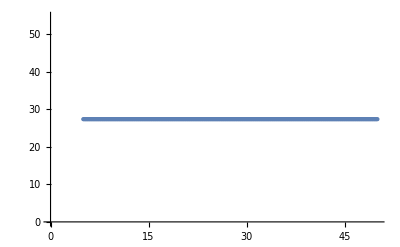

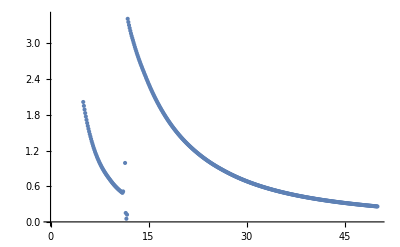

```mathematica
{hnow,know,lnow}={1,1,1};
mnow = 10;

tabnow=Table[{EkeV,
ffactor[EkeV,hnow,know,lnow,mnow]
	}
,{EkeV,5,50,0.1}];

tabre=tabnow;
tabre[[All,2]]=Re[tabnow[[All,2]]];
tabim=tabnow;
tabim[[All,2]]=Im[tabnow[[All,2]]];

{MatrixForm[tabre],MatrixForm[tabim]}

ListPlot[tabre]
ListPlot[tabim]
```